## Log

07/27/2016 TM-- Updated the following features
			File format for saving all parameters was changed to mathematica file from excel file.
			Reading in Parameters section was added.
			PairConnect3 was added. This function connects the nearest spot instead of the first encountered near enough spot.
				Slower than PairConnect2, about a double the speed, but there should not be error.
			PairConnect4 was added. This fucntion gets rid of diversion of tracks.
			LinkTrack2 was added. This function gets rid of tracks which last shorter than threshold. And asign new track numbers.
				This avoids very big track numbers.

07/23/2016 TS -- Updated to match ParticleTracking_for_puro_2Colors.nb, which is what TM used in the Science translation paper. 

9/25/2015 TS -- Updated 3-color Find Red/Green/Blue Particles so that it shows the first “10” (endtest-starttest) and last “10” frames of movies to see if the threshhold works well for the entire movie. 

10/01/18 CC -- merged myROI with particle track code so I can shift mask throughout the movie---it works!!! holy shittt

## Initialize

```mathematica
$HistoryLength=1;
ClearAll["Global`*"];
Off[General::spell, General::spell1]
```

```mathematica
Needs["ErrorBarPlots`"];
```

## Functions and PSF

### MyROI[{img, img, ...},outfile]

```mathematica
MyROI[allimage:{_?ImageQ..},outfile_?StringQ]:=Module[{allimg=allimage},
DynamicModule[{Nimg=Length[allimg],thold,myt=1,y=1,myflag="  Ready.",Colors={Black,Red,Green,Blue,Purple,Orange,Brown,Gray,Pink,Cyan},w,h,mymask,mymaska,mymaskb,mynewmask,zoom,mymaskc,mytable,mytemptable,myCentroid,myroi,chN,mycurpoints,mysavepoints,mytemppoints,r={0,0},cury,numy,roin=30,roit,myshape,p1,p2,Size,Ns,roic,mydata,bd, tholdch,tholdsize,myflag2=" ",sizemean=1,mycc},
mynewmask=0;
thold=0.8;
tholdsize=9;
tholdch=1;
{w,h}=allimg⟦1⟧//ImageDimensions;
mytable=Table[0.,{i,1,h,1},{j,1,w,1}];
bd=allimg⟦1⟧//ImageType;
chN=allimg⟦1⟧//ImageChannels;
mysavepoints=Table[{{{1.,1.}},1.,If[chN>1,Table[1.,{i,1,chN,1}],1],1.},{i,1,30,1},{j,1,Nimg,1}];
mycurpoints=Table[{{{1.,1.}},1.,If[chN>1,Table[1.,{i,1,chN,1}],1],1.},{i,1,30,1}];

(*CHECK FOR PREVIOUS ROI FILES*)
If[FileNames[outfile]≠{},
mytemppoints=(<<(outfile));
Ns=Length[mytemppoints⟦1⟧];
If[Ns≤Nimg,
mysavepoints⟦1;;All,1;;Ns⟧=mytemppoints⟦1;;All,1;;Ns⟧;,mysavepoints⟦1;;All,1;;Nimg⟧=mytemppoints⟦1;;All,1;;Nimg⟧;
];
Clear[mytemppoints];
];

(*CONTROLS............................*)
Column[{
Row[{"ROI:" PopupMenu[Dynamic[y],Join[{1->"Background",2->"Cytoplasm",3->"Nucleus",4->"Nucleoli",5->"Array",6->"ROI6"},Table[i->"ROI"<>ToString[i],{i,7,roin,1}]]],
"  Type:" PopupMenu[Dynamic[roit],{1->"Polygon",2->"Rectangle",3->"Circle"}],Spacer[10],
Button["EXPORT ROI CALC FILE",
If[FileNames[outfile]=={},
mysavepoints>>(outfile); myflag=outfile<>"  File saved.",myflag="   ROIs file already exists."
]],
Button["DELETE ROI CALC FILE",
If[FileNames[outfile]≠{},
DeleteFile[outfile];myflag="  File deleted.",myflag="   No ROIs file found.";
]],
Button["CALCULATE AUTO ROI",
mymaska=Binarize@Image[Graphics[{White,myshape},Background->Black,ImageSize->{w,h},PlotRange->{{0,w},{0,h}}],ColorSpace->"Grayscale"];
mynewmask=mymaska;
mymaskb=Binarize[ImageMultiply[mymaska,ColorSeparate[allimg⟦myt⟧]⟦tholdch⟧//ImageAdjust],thold];
myCentroid=Round[#,1]&/@(Position[mymaskb//ImageData,1]//Mean);
roit=3;
mymaskc=Binarize@Image[Graphics[{White,Disk[{myCentroid⟦2⟧,h-myCentroid⟦1⟧+1},tholdsize]},Background->Black,ImageSize->{w,h},PlotRange->{{0,w},{0,h}}],ColorSpace->"Grayscale"];
mymask=ImageSubtract[mymaskc,mymaskb];
mycurpoints⟦y,1⟧={{myCentroid⟦2⟧,h-myCentroid⟦1⟧+1},{myCentroid⟦2⟧,h-myCentroid⟦1⟧+1}+{tholdsize,0}};
mycurpoints⟦y,2⟧=Count[mymaskc//ImageData//Chop//Flatten,x_/;x≠ 0.]//N;
mysavepoints⟦y,myt,1;;2⟧=mycurpoints⟦y,1;;2⟧;
mysavepoints⟦y,myt,3⟧=Plus@@(ImageData[ImageMultiply[mymaskc,allimg⟦myt⟧],bd]//Flatten[#,1]&)/If[mycurpoints⟦y,2⟧==0,100000000.,mycurpoints⟦y,2⟧];
mysavepoints⟦y,myt,4⟧=3;
],
" Threshhold: ",InputField[Dynamic[thold],FieldSize->3],"  Channel:" PopupMenu[Dynamic[tholdch],{1->"1, red",2->"2, green",3->"3, blue"}],"  ROI Size: ",InputField[Dynamic[tholdsize],FieldSize->3],
Button["CACULATE AUTO ROI FORWARD",
mymaska=Binarize@Image[Graphics[{White,myshape},Background->Black,ImageSize->{w,h},PlotRange->{{0,w},{0,h}}],ColorSpace->"Grayscale"];
Table[
mymaskb=Binarize[ImageMultiply[mymaska,ColorSeparate[allimg⟦tt⟧]⟦tholdch⟧//ImageAdjust],thold];
myCentroid=Round[#,1]&/@(Position[mymaskb//ImageData,1]//Mean);
roit=3;
mymaskc=Binarize@Image[Graphics[{White,Disk[{myCentroid⟦2⟧,h-myCentroid⟦1⟧+1},tholdsize]},Background->Black,ImageSize->{w,h},PlotRange->{{0,w},{0,h}}],ColorSpace->"Grayscale"];
mymask=ImageSubtract[mymaskc,mymaskb];
mycurpoints⟦y,1⟧={{myCentroid⟦2⟧,h-myCentroid⟦1⟧+1},{myCentroid⟦2⟧,h-myCentroid⟦1⟧+1}+{tholdsize,0}};
mycurpoints⟦y,2⟧=Count[mymaskc//ImageData//Chop//Flatten,x_/;x≠ 0.]//N;
mysavepoints⟦y,tt,1;;2⟧=mycurpoints⟦y,1;;2⟧;
mysavepoints⟦y,tt,3⟧=Plus@@(ImageData[ImageMultiply[mymaskc,allimg⟦tt⟧],bd]//Flatten[#,1]&)/If[mycurpoints⟦y,2⟧==0,100000000.,mycurpoints⟦y,2⟧];
mysavepoints⟦y,tt,4⟧=roit;
,{tt,myt,Nimg,1}];
],
Dynamic[myflag],Dynamic[myflag2],
}],
Row[{
Button["CALCULATE ROI BACK",
mymask=Binarize@Image[Graphics[{White,myshape},Background->Black,ImageSize->{w,h},PlotRange->{{0,w},{0,h}}],ColorSpace->"Grayscale"];
mycurpoints⟦y,2⟧=Count[mymask//ImageData//Flatten,x_/;x≠0]//N;
Table[mysavepoints⟦y,tt,1;;2⟧=mycurpoints⟦y,1;;2⟧;
mysavepoints⟦y,tt,3⟧=Plus@@(ImageData[ImageMultiply[mymask,allimg⟦tt⟧],bd]//Flatten[#,1]&)/If[mycurpoints⟦y,2⟧==0,100000000.,mycurpoints⟦y,2⟧];
mysavepoints⟦y,tt,4⟧=roit;
,{tt,myt,1,-1}];
],
Button["CALCULATE ROI",
mymask=Binarize@Image[Graphics[{White,myshape},Background->Black,ImageSize->{w,h},PlotRange->{{0,w},{0,h}}],ColorSpace->"Grayscale"];
mycurpoints⟦y,2⟧=Count[mymask//ImageData//Flatten,x_/;x≠0]//N;
mysavepoints⟦y,myt,1;;2⟧=mycurpoints⟦y,1;;2⟧;
mysavepoints⟦y,myt,3⟧=Plus@@(ImageData[ImageMultiply[mymask,allimg⟦myt⟧],bd]//Flatten[#,1]&)/If[mycurpoints⟦y,2⟧==0,100000000.,mycurpoints⟦y,2⟧];
mysavepoints⟦y,myt,4⟧=roit;
],
Button["CALCULATE ROI FORWARD",
mymask=Binarize@Image[Graphics[{White,myshape},Background->Black,ImageSize->{w,h},PlotRange->{{0,w},{0,h}}],ColorSpace->"Grayscale"];
mycurpoints⟦y,2⟧=Count[mymask//ImageData//Flatten,x_/;x≠0]//N;
Table[mysavepoints⟦y,tt,1;;2⟧=mycurpoints⟦y,1;;2⟧;
mysavepoints⟦y,tt,3⟧=Plus@@(ImageData[ImageMultiply[mymask,allimg⟦tt⟧],bd]//Flatten[#,1]&)/If[mycurpoints⟦y,2⟧==0,100000000.,mycurpoints⟦y,2⟧];
mysavepoints⟦y,tt,4⟧=roit;
,{tt,myt,Nimg,1}];
],
Button["CLEAR ROI",Dynamic[mycurpoints⟦y⟧={{{1,1}},1,0}]],
Button["SHOW ROI",
If[FileNames[outfile]≠{},
mytemppoints=(<<(outfile));
Ns=Length[mytemppoints⟦1⟧];
If[myt≤Ns,
mycurpoints⟦y⟧=mytemppoints⟦y,myt⟧;
roit=mysavepoints⟦y,myt,4⟧;
myflag="  Imported ROI.",
myflag="  No ROI saved.";
];,myflag="  No ROI file found."
]
],
Spacer[10],
{Button["<",mycurpoints⟦y,1⟧=(#-{1,0})&/@mycurpoints⟦y,1⟧,ImageSize->{17,17},BaselinePosition->Center],
Column[
{
Button["^",mycurpoints⟦y,1⟧=(#+{0,1})&/@mycurpoints⟦y,1⟧,ImageSize->{17,17}],
Button["⋁",mycurpoints⟦y,1⟧=(#-{0,1})&/@mycurpoints⟦y,1⟧,ImageSize->{17,17}]
},
BaselinePosition->Center],
Button[">",mycurpoints⟦y,1⟧=(#+{1,0})&/@mycurpoints⟦y,1⟧,ImageSize->{17,17},BaselinePosition->Center]}//Row[#,BaselinePosition->Bottom]&,
Spacer[10],
{Button["⇐",mycurpoints⟦y,1⟧=(#-{30,0})&/@mycurpoints⟦y,1⟧,ImageSize->{17,17},BaselinePosition->Center],
Column[
{
Button["⇑",mycurpoints⟦y,1⟧=(#+{0,30})&/@mycurpoints⟦y,1⟧,ImageSize->{17,17}],
Button["⇓",mycurpoints⟦y,1⟧=(#-{0,30})&/@mycurpoints⟦y,1⟧,ImageSize->{17,17}]
},
BaselinePosition->Center],
Button["⇒",mycurpoints⟦y,1⟧=(#+{30,0})&/@mycurpoints⟦y,1⟧,ImageSize->{17,17},BaselinePosition->Center]}//Row[#,BaselinePosition->Bottom]&
}],

(*Dynamically updated content........................*)
Row[{Slider[Dynamic[myt],{1,Nimg,1},ImageSize->{600,20}] ,Button["-",If[myt>1,myt=myt-1]],Button["+",If[myt<Nimg,myt=myt+1]],Spacer[10],Dynamic[myt]}],
Row[{Slider[Dynamic[zoom],{300,1500,10},ImageSize->{600,20}] }],
Row[{"Choose Channel: "PopupMenu[Dynamic[mycc],Table[i->"Channel "<>ToString[i],{i,0,chN,1}]]}],
Row[{

Manipulate[LocatorPane[Dynamic[mycurpoints⟦y,1⟧],
Show[If[mycc>0,ImageAdjust[ColorSeparate[allimg⟦myt⟧]⟦mycc⟧],
ImageAdjust[allimg⟦myt⟧]],ImageSize->{zoom}],LocatorAutoCreate->True,Appearance->"+"],{{br,30},0.1,100,0.01},ControlType->{VerticalSlider},ControlPlacement->Left],
Spacer[10],Dynamic[
GraphicsColumn[
(#//ImageAdjust//Show[{#,Graphics[{EdgeForm[Directive[Yellow]],Opacity[0.],
myshape=If[roit==1,Polygon[mycurpoints⟦y,1⟧],
If[roit==2,
p1={Min[mycurpoints⟦y,1,1;;All,1⟧],Min[mycurpoints⟦y,1,1;;All,2⟧]};
p2={Max[mycurpoints⟦y,1,1;;All,1⟧],Max[mycurpoints⟦y,1,1;;All,2⟧]};
myflag="  dim="<>ToString[Round[Abs[p1-p2],1]];
Rectangle[p1,p2],
If[roit==3,
p1={Max[mycurpoints⟦y,1,1;;All,1⟧],Max[mycurpoints⟦y,1,1;;All,2⟧]};p2={Min[mycurpoints⟦y,1,1;;All,1⟧],Min[mycurpoints⟦y,1,1;;All,2⟧]};
Size=√((p1-p2).(p1-p2));
myflag="  radius="<>ToString[Round[Size,1]];
Disk[mycurpoints⟦y,1,1⟧,Size]]]]}]}]&)&/@ColorSeparate[allimg⟦myt⟧],
Background->{Red,Green,Blue,Orange,Purple,Pink,Black,Gray,Brown},ImageSize->{500}]],
Dynamic[
mydata=If[sizemean==1,If[chN==1,mysavepoints⟦y,1;;All,3⟧/If[cury==0,1,mysavepoints⟦cury,1;;All,3⟧],mysavepoints⟦y,1;;All,3⟧/If[cury==0,1,mysavepoints⟦cury,1;;All,3⟧]//Transpose],mysavepoints⟦y,1;;All,2⟧];
Column[{
Row[{Spacer[130],
"ROI /"PopupMenu[Dynamic[cury],Join[{0->"Choose Divider",1->"Background",2->"Cytoplasm",3->"Nucleus",4->"Nucleoli",5->"Array",6->"ROI6"},Table[i->"ROI"<>ToString[i],{i,7,30,1}]]]
}],
Row[{Spacer[130],
"Measure:"PopupMenu[Dynamic[sizemean],{0->"ROI Size",1->"ROI Mean Int."}]
}],
ListPlot[mydata,Joined->True,Frame->True,FrameTicks->{{All,All},{All,All}},FrameLabel->{"Image #", If[sizemean==1,"Mean Int.","ROI Size (pixels)"]},PlotMarkers->{Automatic,8} ,PlotStyle->Colors⟦2;;All⟧,AxesOrigin->{0,Automatic},ImageSize->300,AspectRatio->1,PlotRange->{{0,Nimg+1},All}]//Show[{#,Graphics[{Purple,Dashed,Line[{{myt,-1000},{myt,1000}}]}]}]&

},Dynamic[mymask]]]
}]
}]//Panel
]]
```

### MyNumString

```mathematica
MyNumString[myn_,L_]:=If[myn>10^L-1,IntegerString[myn,10,L+1],IntegerString[myn,10,L]];
```

```mathematica
MyNumString[30,3]
```

030

### BandPass

```mathematica
BandPass[img_,{lo_,hi_}]:=Module[{imgb,imgc},
imgb=ImageConvolve[img,GaussianMatrix[{hi,lo}]];
(*imgc=ImageConvolve[img,BoxMatrix[hi]/(2 hi+1)^2];*)
imgc=ImageConvolve[img,DiskMatrix[hi]/(Plus@@Plus@@DiskMatrix[hi])];
ImageSubtract[imgb,imgc]
]
```

```mathematica
(*BandPass[-Graphics-,{1,12}]//ImageAdjust*)
```

### FindParticles (updated to remove adjacentbordercounts)

```mathematica
FindParticlesWeighted[img_,{lo_,hi_},max_,th_,imgmask_,{small_,large_}]:=Module[{imgb,imgc,pos},
imgb=BandPass[img,{lo,hi}];
imgc=SelectComponents[ImageMultiply[imgb//Binarize[#, max th]&,imgmask],{"Count","AdjacentBorderCount"},small<#1<large&&#2==0&];
ComponentMeasurements[ImageMultiply[img,imgc],{"IntensityCentroid"}]⟦All,2,1⟧
(*{Show[img,Graphics[{Color,Circle[#,hi 1.5]&/@(pos=ComponentMeasurements[imgc,{"Centroid"}][[All,2,1]])}]],pos}*)
]
```

```mathematica
FindParticlesWeightedMask[img_,{lo_,hi_},max_,th_,imgmask_,{small_,large_}]:=Module[{imgb,imgc,pos},
imgb=BandPass[img,{lo,hi}];
imgc=SelectComponents[ImageMultiply[imgb//Binarize[#, max th]&,imgmask],{"Count","AdjacentBorderCount"},small<#1<large&&#2==0&]
]
```

### PairConnect2 (still one small error, but doesn’t seem to mess up stuff)

```mathematica
PairConnect2[{ticker_,anolist1t_},list2t_,dist_]:=Module[{newticker,finalticker,list1,list2,flag,out,newTracks,mypos,myind,myl,out2,out3},
newticker=ticker;
list1=Sort[anolist1t,#1⟦2,1⟧<#2⟦2,1⟧&];
list2=Sort@list2t;
flag=0;
out=Table[
myind=1;
mypos=list2⟦myind,1⟧;
Reap[
While[(*list1⟦m,2,1⟧-dist≤ *)mypos≤list1⟦m,2,1⟧+dist &&myind≤ Length@list2,
If[EuclideanDistance[list2⟦myind⟧,list1⟦m,2⟧]≤dist,
Sow[{list1⟦m,1⟧,list2⟦myind⟧}];
list2=Delete[list2,myind];
myind=myind-1;
flag=flag+1;
];
myind=myind+1;
If[Length@list2>0&&myind≤Length@list2,mypos=list2⟦myind,1⟧,m=Length@list1];
];
],
{m,1,Length@list1,1}];
out2=DeleteCases[out⟦All,2⟧//Flatten[#,2]&,Null];
If[Length@list2>0,
finalticker=newticker+Length[list2];
newTracks={Range[newticker+1,finalticker],list2}//Transpose;
out3=Join[out2,newTracks];,
finalticker=newticker;
out3=out2;
];
{finalticker,out3}
]
```

### PairConnect3 (Connect a dot in frame(n) to the nearest dot in frame(n-1) which is less than the determined jumping distance > there is no conversion, but diversion)

```mathematica
(* This function is used with LinkTracks or LinkTracks2

	A cordinate of each dots at frame# N+1 is compared with dots at frame# N by Table function
	Those dots located +/- "dist_" are listed as "potentialDots"
	If the nearest dots in "potentialDots" is actually less than "dist_"
	the track number of the dot is given to the current dot at frame# N+1
	This will ensure there is no conversion in tracks
	If there is no dots closeby in frame #N, the current dot gets the new track number

		list1⟦1⟧: the latest (biggest) track number being used (newticker)
		list1⟦2⟧: the list of cordinate of points with a track number at frame# N 
		list2:    the list of cordinate of points at frame# N+1

	 out:      the list of cordinate of points with a track number at frame# N+1
 *)
```

```mathematica
PairConnect3[{ticker_,anolist1t_},list2t_,dist_]:=Module[{newticker,list1,list2,out,mypos},
newticker=ticker;
list1=Sort[anolist1t,#1⟦2,1⟧<#2⟦2,1⟧&];
list2=Sort@list2t;
out=Table[mypos=list2⟦myi⟧;
potentialDots=Cases[list1,x_/;mypos⟦1⟧-dist<x⟦2,1⟧<mypos⟦1⟧+dist&&mypos⟦2⟧-dist<x⟦2,2⟧<mypos⟦2⟧+dist];
If[potentialDots=={},
newticker+=1;out={newticker,mypos};,
potentialDot=Flatten[Cases[potentialDots,x_/;x⟦2⟧==Flatten@Nearest[potentialDots⟦All,2⟧,mypos]],1];
	If[EuclideanDistance[mypos,potentialDot⟦2⟧]>dist,
	newticker+=1;out={newticker,mypos};,out={potentialDot⟦1⟧,mypos};]];out,{myi,1,Length@list2,1}];
{newticker,out}
]
```

### PairConnect4 (PairConnect3 + removing diversion)

```mathematica
(* This function is used with LinkTracks or LinkTracks2

	After connecting all dots at frame# N+1 to dots at frame# N
	finding redundant track numbers by using RedundantTrack function

	RedundantTrack[{1,2,5,1,6,7,2,2,5}]
	{{1,2,5,6,7},{1,2,5},{{{1},{4}},{{2},{7},{8}},{{3},{9}}}}

	redundant track numbers means track gets split at frame# N+1
	in order to avoid this, choosing the nearest point and assign a new track number to the other points
*)
```

```mathematica
RedundantTrack[list_,test_: Identity]:=Composition[{#⟦1⟧,#⟦2⟧,Position[list,#]&/@#⟦2⟧}&,{#⟦All,1⟧,DeleteCases[#,{_}]⟦All,1⟧}&,GatherBy[#,test]&][list]
```

```mathematica
PairConnect4[{ticker_,anolist1t_},list2t_,dist_]:=Module[{newticker,list1,list2,out,mypos,myRedundant,null,tempOriginalPoint,tempNewPoints,tempTruePoint,tempOutlierPointPosi},
newticker=ticker;
list1=Sort[anolist1t,#1⟦2,1⟧<#2⟦2,1⟧&];
list2=Sort@list2t;
out=Table[mypos=list2⟦myi⟧;
potentialDots=Cases[list1,x_/;mypos⟦1⟧-dist<x⟦2,1⟧<mypos⟦1⟧+dist&&mypos⟦2⟧-dist<x⟦2,2⟧<mypos⟦2⟧+dist];
If[potentialDots=={},
newticker+=1;out={newticker,mypos};,
potentialDot=Flatten[Cases[potentialDots,x_/;x⟦2⟧==Flatten@Nearest[potentialDots⟦All,2⟧,mypos]],1];
	If[EuclideanDistance[mypos,potentialDot⟦2⟧]>dist,
	newticker+=1;out={newticker,mypos};,out={potentialDot⟦1⟧,mypos};]];out,{myi,1,Length@list2,1}];
myRedundant=RedundantTrack[out⟦All,1⟧];
null=Table[
tempOriginalPoint=Extract[list1,Position[list1⟦All,1⟧,myRedundant⟦2,myj⟧]];
tempNewPoints=out⟦Flatten@myRedundant⟦3,myj⟧⟧;
tempTruePoint=Position[tempNewPoints,Flatten@Nearest[tempNewPoints⟦All,2⟧,tempOriginalPoint⟦1,2⟧]]⟦1,1⟧;
tempOutlierPointPosi=Delete[myRedundant⟦3,myj⟧,tempTruePoint]//Flatten;
Range[newticker+1,newticker+Length@tempOutlierPointPosi];
out⟦tempOutlierPointPosi,1⟧=Range[newticker+1,newticker+Length@tempOutlierPointPosi];
newticker=newticker+Length@tempOutlierPointPosi;
,{myj,1,Length@myRedundant⟦2⟧,1}];
{newticker,out}
]
```

### LinkTracks

```mathematica
LinkTracks[testgreenP_,dist_]:=Module[{list1,list2,listResult,listResultFrame,listResultTrack},
list1=Thread@{Range@Length@testgreenP⟦1⟧,Sort@testgreenP⟦1⟧};
list1={Length@list1,list1};
list2=testgreenP⟦2;;⟧;
listResult=FoldList[PairConnect4[#1,#2,dist]&,list1,list2];
listResultFrame=Table[Insert[listResult⟦i⟧,i,Table[{2,j,2,1},{j,1,Length@listResult⟦i,2⟧,1}]],{i,1,Length@listResult,1}];
listResultTrack=SplitBy[listResultFrame⟦All,2⟧//Flatten[#,1]&//Sort,First];
{listResultFrame,listResultTrack}
]
```

### LinkTracks2

```mathematica
(* get rid of tracks which last only 1 or 2 frame(s) and re-assign consecutive track numbers *)
```

```mathematica
LinkTracks2[testgreenP_,dist_]:=Module[{list1,list2,listResult,listResultFrame,listResultTrack,listResultTrackL},
list1=Thread@{Range@Length@testgreenP⟦1⟧,Sort@testgreenP⟦1⟧};
list1={Length@list1,list1};
list2=testgreenP⟦2;;⟧;
listResult=FoldList[PairConnect4[#1,#2,dist]&,list1,list2];
listResultFrame=Table[Insert[listResult⟦i⟧,i,Table[{2,j,2,1},{j,1,Length@listResult⟦i,2⟧,1}]],{i,1,Length@listResult,1}];
listResultTrack=SplitBy[listResultFrame⟦All,2⟧//Flatten[#,1]&//Sort,First];
listResultTrackL=Extract[listResultTrack,Position[Length/@listResultTrack,x_/;x>2]];
listResultTrackL⟦All,All,1⟧=Range@Length@listResultTrackL;
listResultTrackL
]
```

### Relinking

```mathematica
(* Only the longest path will be taken for the last frame if the track split in the middle *)
```

```mathematica
Relinking[sortedbyframe_,sortedbytrack_,gap_,distance_]:=Module[{ftrackList,ltrackList,linkinglist,mytrack,mytrackN,myt,mypos,newrange,flag,targetFrame,targetTracks,candidateTracks,closestTrack,out,newlinkinglist,newsortedbytrack,oldtrackN,newtrackN,newsortedbyframe,oldtrackPos},

(* extracting the begining and the ending of all tracks *)
ftrackList=SortBy[(First/@sortedbytrack⟦All⟧),{#⟦2,1⟧,#⟦1⟧}&];
ftrackList=DeleteCases[ftrackList,x_/;x⟦2,1⟧≤2];
ltrackList=SortBy[Last/@sortedbytrack⟦All⟧,{#⟦2,1⟧,#⟦1⟧}&];

(* relinking tracks and making a list*)
linkinglist={};
Table[
mytrack=ftrackList⟦i⟧;
mytrackN=mytrack⟦1⟧;
myt=mytrack⟦2,1⟧;
mypos=mytrack⟦2,2;;3⟧;
newrange=Range[myt-gap-1,myt-2,1]//Reverse;
flag=0;
Table[
targetFrame=newrange⟦j⟧;
If[flag==0,
targetTracks=Extract[ltrackList,Position[ltrackList⟦All,2,1⟧,targetFrame]];
candidateTracks=Select[targetTracks,EuclideanDistance[#⟦2,2;;3⟧,mypos]<distance&];
If[Length[candidateTracks]>0,
If[Length[candidateTracks]==1,out={mytrackN,candidateTracks⟦1,1⟧};ltrackList⟦mytrackN,1⟧=candidateTracks⟦1,1⟧;flag=1;,
closestTrack=Extract[candidateTracks,Position[x=EuclideanDistance[#,mypos]&/@candidateTracks⟦All,2,2;;3⟧,Min[x]]];
out={mytrackN,closestTrack⟦1,1⟧};ltrackList⟦mytrackN,1⟧=closestTrack⟦1,1⟧;flag=1;],out={};flag=0]];
,{j,1,Length[newrange],1}];
linkinglist=Append[linkinglist,out];
,{i,1,Length[ftrackList],1}];

(* convert old track numbers to new track numbers in "sortedbytrack" and "sortedbyframe" *)
newlinkinglist=DeleteCases[linkinglist,{}];
newsortedbytrack=sortedbytrack;
newsortedbyframe=sortedbyframe;
Table[
oldtrackN=newlinkinglist⟦i,1⟧;
newtrackN=newlinkinglist⟦i,2⟧;
newsortedbytrack⟦oldtrackN,All,1⟧=newtrackN;
oldtrackPos=Position[newsortedbyframe⟦All,2,All,1⟧,oldtrackN]//Flatten//Riffle[#,{2,1}]&//Append[#,1]&//Partition[#,4]&;
newsortedbyframe=ReplacePart[newsortedbyframe,oldtrackPos -> newtrackN];,
{i,1,Length[newlinkinglist],1}];
newsortedbytrack=newsortedbytrack//Flatten[#,1]&//Sort//SplitBy[#,First]&;

{newsortedbyframe,newsortedbytrack,newlinkinglist}
]
```

```mathematica
(*{sortedbyframe,sortedbytrack}=LinkTracks[testgreenP,1];*)
```

### ParticleFitting

When raw images are used for fitting, avgFrameN_ is used to shift frames such that the middle frame of running average is used for fitting.
For example when avgFrameN is 3, the centroid at the first time point in mylongtrack is determined from the average image of frame 1, 2 and 3. So frame 2 should be fitted with this initial guess.
When running averaged images are used for fitting, enter “1” at the last input instead of avgFrameN.

```mathematica
ParticleFittingSee[myColMovie_,channel_,mylongtrack_,pad_,myTrimSize_,avgFrameN_]:=Module[{tempTime,tempCenter,frameShift},
Table[
tempTime=mylongtrack⟦t,2,1⟧;
tempCenter=Ceiling[mylongtrack⟦t,2,2;;⟧];
frameShift=Ceiling[avgFrameN/2];
ImageTrim[myColMovie⟦channel,tempTime+frameShift-1⟧,{tempCenter-pad,tempCenter+pad-0.1}]
,{t,1,Length[mylongtrack],1}]
]
```

```mathematica
ParticleFitting[myColMovie_,channel_,mylongtracks_,pad_,myTrimSize_,avgFrameN_]:=Module[{myAllParametersEach,myTrimImgs,myOrigins,tempTime,tempCenter,frameShift,myImgs,myData,myFits,tempData3D,myFit,myPos,myPosImgCoordn,myAbsPos,myIntBGSigma,myPos90Conf,myPos90ConfImgCoordn,myAbsPos90Conf,myIntBGSigma90Conf,myFitData,CC,A,x0,a,y0,b,x,y},
{myAllParametersEach,myPos,myFitData}=Table[
{myTrimImgs,myOrigins}=Table[
tempTime=mylongtracks⟦j,t,2,1⟧;
tempCenter=Ceiling[mylongtracks⟦j,t,2,2;;⟧];
frameShift=Ceiling[avgFrameN/2];
{myImgs=ImageTrim[myColMovie⟦channel,tempTime+frameShift-1⟧,{tempCenter-pad,tempCenter+pad-0.1}],
myOrigins=tempCenter-pad-1}
,{t,1,Length[mylongtracks⟦j⟧],1}]//Transpose;
myData=ImageData/@myTrimImgs;
myFits=Table[
tempData3D=Flatten[MapIndexed[{#2⟦1⟧,#2⟦2⟧,#1}&,myData⟦i⟧,{2}],1];
Clear[CC,A,x0,a,y0,b,x,y];
myFit=NonlinearModelFit[tempData3D,CC+A E^(-(x-x0)^2/(2 a^2)-(y-y0)^2/(2 b^2)),
{{CC,0.01},{A,tempData3D⟦(2*pad*(pad+1)+1),3⟧},{x0,pad+1},{a,1},{y0,pad+1},{b,1}},{x,y}];
myFit[{"ParameterTable","ANOVATable","ParameterConfidenceIntervals"}]
,{i,1,Length[myData],1}];
(* Rearrange the parameters *)
myPos=myFits⟦All,1,1,1,{4,6},2⟧;
myPosImgCoordn={myPos⟦All,2⟧-0.5,myTrimSize-myPos⟦All,1⟧+0.5}//Thread;
myAbsPos=myPosImgCoordn+myOrigins;
myIntBGSigma=myFits⟦All,1,1,1,{3,2,5,7},2⟧;
myPos90Conf=myFits⟦All,3,{3,5}⟧;
myPos90ConfImgCoordn={myPos90Conf⟦All,2⟧-0.5,myTrimSize-myPos90Conf⟦All,1⟧+0.5}//Thread;
myPos90ConfImgCoordn⟦All,2,{1,2}⟧=myPos90ConfImgCoordn⟦All,2,{2,1}⟧;
myAbsPos90Conf=myPos90ConfImgCoordn+myOrigins;
myIntBGSigma90Conf=myFits⟦All,3,{2,1,4,6}⟧;
(* Output the paramters *)
{myAllParametersEach=Flatten/@Thread@{mylongtracks⟦j,All,1⟧,mylongtracks⟦j,All,2,1⟧,myAbsPos,myIntBGSigma,myAbsPos90Conf,myIntBGSigma90Conf,mylongtracks⟦j,All,3⟧},myPos,myData}
,{j,1,Length[mylongtracks],1}]//Transpose;
{myAllParametersEach//Flatten[#,1]&,myPos,myFitData}
]
```

```mathematica
ParticleFittingFixedSigma[myColMovie_,channel_,mylongtracks_,pad_,myTrimSize_,sigma_,avgFrameN_]:=Module[{myAllParametersEach,myTrimImgs,myOrigins,tempTime,tempCenter,frameShift,myImgs,myData,myFits,tempData3D,myFit,myPos,myPosImgCoordn,myAbsPos,myIntBG,myPos90Conf,myPos90ConfImgCoordn,myAbsPos90Conf,myIntBG90Conf,myFitData,CC,A,x0,y0,x,y},
{myAllParametersEach,myPos,myFitData}=Table[
{myTrimImgs,myOrigins}=Table[
tempTime=mylongtracks⟦j,t,2,1⟧;
tempCenter=Ceiling[mylongtracks⟦j,t,2,2;;⟧];
frameShift=Ceiling[avgFrameN/2];
{myImgs=ImageTrim[myColMovie⟦channel,tempTime+frameShift-1⟧,{tempCenter-pad,tempCenter+pad-0.1}],
myOrigins=tempCenter-pad-1}
,{t,1,Length[mylongtracks⟦j⟧],1}]//Transpose;
myData=ImageData/@myTrimImgs;
myFits=Table[
tempData3D=Flatten[MapIndexed[{#2⟦1⟧,#2⟦2⟧,#1}&,myData⟦i⟧,{2}],1];
Clear[CC,A,x0,y0,x,y];
myFit=NonlinearModelFit[tempData3D,CC+A E^(-(x-x0)^2/(2 sigma^2)-(y-y0)^2/(2 sigma^2)),
{{CC,0.01},{A,tempData3D⟦(2*pad*(pad+1)+1),3⟧},{x0,pad+1},{y0,pad+1}},{x,y}];
myFit[{"ParameterTable","ANOVATable","ParameterConfidenceIntervals"}]
,{i,1,Length[myData],1}];
(* Rearrange the parameters *)
myPos=myFits⟦All,1,1,1,{4,5},2⟧;
myPosImgCoordn={myPos⟦All,2⟧-0.5,myTrimSize-myPos⟦All,1⟧+0.5}//Thread;
myAbsPos=myPosImgCoordn+myOrigins;
myIntBG=myFits⟦All,1,1,1,{3,2},2⟧;
myPos90Conf=myFits⟦All,3,{3,4}⟧;
myPos90ConfImgCoordn={myPos90Conf⟦All,2⟧-0.5,myTrimSize-myPos90Conf⟦All,1⟧+0.5}//Thread;
myPos90ConfImgCoordn⟦All,2,{1,2}⟧=myPos90ConfImgCoordn⟦All,2,{2,1}⟧;
myAbsPos90Conf=myPos90ConfImgCoordn+myOrigins;
myIntBG90Conf=myFits⟦All,3,{2,1}⟧;
(* Output the paramters *)
{myAllParametersEach=Flatten/@Thread@{mylongtracks⟦j,All,1⟧,mylongtracks⟦j,All,2,1⟧,myAbsPos,myIntBG,ConstantArray[sigma,{Length[myFits],2}],myAbsPos90Conf,myIntBG90Conf,ConstantArray[0,{Length[myFits],4}],mylongtracks⟦j,All,3⟧},myPos,myData}
,{j,1,Length[mylongtracks],1}]//Transpose;
{myAllParametersEach//Flatten[#,1]&,myPos,myFitData}
]
```

```mathematica
ParticleFittingFixedSigmaInclinedBG[myColMovie_,channel_,mylongtracks_,pad_,myTrimSize_,sigma_,avgFrameN_]:=Module[{myAllParametersEach,myTrimImgs,myOrigins,tempTime,tempCenter,frameShift,myImgs,myData,myFits,tempData3D,myFit,myPos,myPosImgCoordn,myAbsPos,myIntBG,myInclinedBG,myPos90Conf,myPos90ConfImgCoordn,myAbsPos90Conf,myIntBG90Conf,myInclinedBG90conf,myFitData,CC,BGa,BGb,A,x0,y0,x,y},
{myAllParametersEach,myPos,myFitData}=Table[
{myTrimImgs,myOrigins}=Table[
tempTime=mylongtracks⟦j,t,2,1⟧;
tempCenter=Ceiling[mylongtracks⟦j,t,2,2;;⟧];
frameShift=Ceiling[avgFrameN/2];
{myImgs=ImageTrim[myColMovie⟦channel,tempTime+frameShift-1⟧,{tempCenter-pad,tempCenter+pad-0.1}],
myOrigins=tempCenter-pad-1}
,{t,1,Length[mylongtracks⟦j⟧],1}]//Transpose;
myData=ImageData/@myTrimImgs;
myFits=Table[
tempData3D=Flatten[MapIndexed[{#2⟦1⟧,#2⟦2⟧,#1}&,myData⟦i⟧,{2}],1];
Clear[CC,BGa,BGb,A,x0,y0,x,y];
myFit=NonlinearModelFit[tempData3D,CC + BGa x + BGb y+A E^(-(x-x0)^2/(2 sigma^2)-(y-y0)^2/(2 sigma^2)),
{{CC,0.01},{A,tempData3D⟦(2*pad*(pad+1)+1),3⟧},{x0,pad+1},{y0,pad+1},{BGa,0.01},{BGb,0.01}},{x,y}];
myFit[{"ParameterTable","ANOVATable","ParameterConfidenceIntervals"}]
,{i,1,Length[myData],1}];
(* Rearrange the parameters *)
myPos=myFits⟦All,1,1,1,{4,5},2⟧;
myPosImgCoordn={myPos⟦All,2⟧-0.5,myTrimSize-myPos⟦All,1⟧+0.5}//Thread;
myAbsPos=myPosImgCoordn+myOrigins;
myIntBG=myFits⟦All,1,1,1,{3,2},2⟧;
myInclinedBG=myFits⟦All,1,1,1,{6,7},2⟧;
myPos90Conf=myFits⟦All,3,{3,4}⟧;
myPos90ConfImgCoordn={myPos90Conf⟦All,2⟧-0.5,myTrimSize-myPos90Conf⟦All,1⟧+0.5}//Thread;
myPos90ConfImgCoordn⟦All,2,{1,2}⟧=myPos90ConfImgCoordn⟦All,2,{2,1}⟧;
myAbsPos90Conf=myPos90ConfImgCoordn+myOrigins;
myIntBG90Conf=myFits⟦All,3,{2,1}⟧;
myInclinedBG90conf=myFits⟦All,3,{5,6}⟧;
(* Output the paramters *)
{myAllParametersEach=Flatten/@Thread@{mylongtracks⟦j,All,1⟧,mylongtracks⟦j,All,2,1⟧,myAbsPos,myIntBG,ConstantArray[sigma,{Length[myFits],2}],myAbsPos90Conf,myIntBG90Conf,ConstantArray[0,{Length[myFits],4}],mylongtracks⟦j,All,3⟧,myInclinedBG,myInclinedBG90conf},myPos,myData}
,{j,1,Length[mylongtracks],1}]//Transpose;
{myAllParametersEach//Flatten[#,1]&,myPos,myFitData}
]
```

### BeadsFitting

```mathematica
BeadsFitting[myRefBeadsImg_,myPosGuess_,pad_]:=
Module[{myTrimSize,myTrimImgs,myOrigins,tempCenter,myImgs,myData,myFits,tempData3D,myFit,CC,A,x,x0,a,y,y0,b,myPos,myPosImgCoordn,myAbsPos},

myTrimSize=2*pad+1;
{myTrimImgs,myOrigins}=Table[
tempCenter=Ceiling[myPosGuess⟦i⟧];
{myImgs=ImageTrim[myRefBeadsImg,{tempCenter-pad,tempCenter+pad-0.1}],
myOrigins=tempCenter-pad-1}
,{i,1,Length[myPosGuess],1}]//Transpose;
myData=ImageData/@myTrimImgs;
myFits=Table[
tempData3D=Flatten[MapIndexed[{#2⟦1⟧,#2⟦2⟧,#1}&,myData⟦i⟧,{2}],1];
Clear[CC,A,x0,a,y0,b,x,y];
myFit=NonlinearModelFit[tempData3D,CC+A E^(-(x-x0)^2/(2 a^2)-(y-y0)^2/(2 b^2)),
{{CC,0},{A,tempData3D⟦(2*pad*(pad+1)+1),3⟧},{x0,pad+1},{a,1},{y0,pad+1},{b,1}},{x,y}];
myFit[{"ParameterTable","ANOVATable","ParameterConfidenceIntervals"}]
,{i,1,Length[myData],1}];
myPos=myFits⟦All,1,1,1,{4,6},2⟧;
myPosImgCoordn={myPos⟦All,2⟧-0.5,myTrimSize-myPos⟦All,1⟧+0.5}//Thread;
myAbsPos=myPosImgCoordn+myOrigins
]
```

```mathematica
BeadsSorting[myRedAbsPos_,myGreenAbsPos_,dist_]:=
Module[{myRedAbsPosSort,distanceOriginal,idx,myRedAbsPos4Calc,myGreenAbsPos4Calc,distanceRaw},

myRedAbsPosSort=Nearest[myRedAbsPos,myGreenAbsPos]//Flatten[#,1]&;
distanceOriginal=EuclideanDistance@@@Thread@{myGreenAbsPos,myRedAbsPosSort};
idx=Position[distanceOriginal,x_/;x>dist];
{myRedAbsPos4Calc,myGreenAbsPos4Calc,distanceRaw}=Delete[#,idx]&/@{myRedAbsPosSort,myGreenAbsPos,distanceOriginal}
]
```

```mathematica
BeadsTransform[myRedAbsPos_,myGreenAbsPos_,dist_]:=
Module[{myRedAbsPos4Calc,myGreenAbsPos4Calc,distanceRaw,myTfFuncError,myTfFunc,myRedCorrPos,distanceCorrected},

{myRedAbsPos4Calc,myGreenAbsPos4Calc,distanceRaw}=BeadsSorting[myRedAbsPos,myGreenAbsPos,dist];
{myTfFuncError,myTfFunc}=FindGeometricTransform[myGreenAbsPos4Calc,myRedAbsPos4Calc];
myRedCorrPos=myTfFunc[myRedAbsPos4Calc];
distanceCorrected=EuclideanDistance@@@Thread@{myGreenAbsPos4Calc,myRedCorrPos};
{myTfFuncError,myTfFunc,distanceRaw,distanceCorrected}

]
```

```mathematica
BeadsCheck[myRedAbsPos_,myGreenAbsPos_,dist_]:=
Module[{myRedAbsPos4Calc,myGreenAbsPos4Calc,distanceRaw,myRedCorrPos,distanceCorrected},

{myRedAbsPos4Calc,myGreenAbsPos4Calc,distanceRaw}=BeadsSorting[myRedAbsPos,myGreenAbsPos,dist];
myRedCorrPos=myTfFunc[myRedAbsPos4Calc];
distanceCorrected=EuclideanDistance@@@Thread@{myGreenAbsPos4Calc,myRedCorrPos};
Insert[{distanceRaw,distanceCorrected}//Transpose,{"Distance Before Correction","Distance After Correction"},1]//TableForm
]
```

### FindOverlapDistance[track1,track2,τ] (measures average distance between two tracks when they overlap in time for at least time τ, otherwise outputs -1)

```mathematica
FindOverlapDist[track1_,track2_,τ_]:=Module[{t1,t2,ol,avgpos1,avgpos2},
(*makes tracks have form: t1={{track#,time1,x1,y1},{track#,time2,x2,y2} ...}*)
t1=track1//Flatten//Partition[#,7]&; 
t2=track2//Flatten//Partition[#,7]&;
(* The following just sorts by time rather than track # and splits. If the two tracks have overlapping time, then the split will contain 2 elements. Thus, DeleteCases eliminates all parts of the track that do not overlap. Finally, the Transpose command gives back a list of overlapping segments of tracks: {segment from t1, segment from t2} so the mean can be computed for each.*)
ol={t1⟦All,{2,1,3,4,5,6,7}⟧,t2⟦All,{2,1,3,4,5,6,7}⟧}//Flatten[#,1]&//Sort//SplitBy[#,First]&//DeleteCases[#,x_/;Length[x]<2]&;
If[Length[ol]>τ,{avgpos1,avgpos2}=(Mean/@(Transpose[ol]))⟦All,3;;4⟧;EuclideanDistance[avgpos1,avgpos2],-1]
]
```

### ColorLinker[gbtrackpairs, greentracklist, blueflag] → bluetracklist connected to greentracklist

```mathematica
(*This returns all green (or blue, specified by colorN = 1 for green and 2 for blue) elements of gbpairs whose blue (or green) element is a member of colorList  *)
ColorLinker[pairs_,colorList_,colorN_]:=Module[{},
Cases[pairs,x_/;MemberQ[colorList,x⟦If[colorN==1,2,1]⟧]]⟦All,colorN⟧//Union
]
```

### CrossPairFinder[gbtrackpairs] → list of green tracks gi connected to list of blue tracks bi : {{g1,b1}, {g2, b2}, ...}

```mathematica
CrossPairFinder[myGBpairs_]:=Module[{b1,g1,seed,myFlag=0,i},
Table[
seed={myGBpairs⟦i,1⟧}; (*seed with ith green element from pair list*)
While[myFlag==0 , 
b1=ColorLinker[myGBpairs,seed,2]//Union; (*bluelist b1 connected to greenlist seed *)
g1=ColorLinker[myGBpairs,b1,1]//Union; (*greenlist g1 connected to bluelist b1*)
If[g1==seed,myFlag=1, seed=g1] (*exit if greenlist g1 is the same as seed; if not, g1 becomes new seed*)
];
myFlag=0; (*repeat loop for all possible green seeds*)
{g1,b1},{i,1,Length[myGBpairs],1}]//Union
]
```

### ConnectByColor

```mathematica
Connect2Colors[track1_,track2_,minOverlapTime_,maxOverlapDistance_]:=Module[{idxTrack1,idxTrack2,myAllLink,tempTrack1,tempTrack2,myLinkList,newTrack1,newTrack2,myMergedTrack,bigTrack1,bigTrack2},
	(*Getting color index assuming the tracks have never been connected with any other colors*)
idxTrack1=track1⟦1,1,3⟧;
idxTrack2=track2⟦1,1,3⟧;
	(*Creating linking pair list*)
myAllLink=Table[
tempTrack1=track1⟦i⟧;
tempTrack2=track2⟦j⟧;
FindOverlapDist[tempTrack1,tempTrack2,minOverlapTime],{i,1,Length@track1,1},{j,1,Length@track2,1}];
myLinkList=CrossPairFinder[Position[myAllLink,x_/;0≤x<maxOverlapDistance]];
	(*Preparing output track*)
newTrack1=track1;
newTrack2=track2;
	(*Connecting tracks*)
Table[
myMergedTrack={track1⟦myLinkList⟦i,1⟧⟧,track2⟦myLinkList⟦i,2⟧⟧}//Flatten[#,2]&//SortBy[#,#⟦2,1⟧&]&//SplitBy[#,#⟦2,1⟧&]&;

bigTrack1=(If[Length[#]==2, Cases[#,x_/;x⟦3⟧==idxTrack1],If[Length[#]==1, #,{}]]&/@myMergedTrack);  (*Note that this automatically deletes times where three or more points appears at once*)
bigTrack1=DeleteCases[bigTrack1,x_/;Length@x>1]//Flatten[#,1]&;(*Note that this automatically deletes times where there is overlap in multiple tracks in track1*)
bigTrack1⟦All,1⟧=myLinkList⟦i,1,1⟧; (*Choose to label big track as lowest #'d track1*)
bigTrack1⟦All,3⟧=idxTrack1+idxTrack2;(*Change color index to two colors from one color*)
newTrack1⟦myLinkList⟦i,1,1⟧⟧=bigTrack1; 
If[Length@myLinkList⟦i,1⟧>1,newTrack1⟦myLinkList⟦i,1,2;;⟧⟧={}];
(*lowest # track1 that should be linked is replaced with bigTrack1; others become {};*)

bigTrack2=(If[Length[#]==2, Cases[#,x_/;x⟦3⟧==idxTrack2],If[Length[#]==1, #,{}]]&/@myMergedTrack);
bigTrack2=DeleteCases[bigTrack2,x_/;Length@x>1]//Flatten[#,1]&;
bigTrack2⟦All,1⟧=myLinkList⟦i,1,1⟧; 
bigTrack2⟦All,3⟧=idxTrack1+idxTrack2;
newTrack2⟦myLinkList⟦i,2,1⟧⟧=bigTrack2; 
If[Length@myLinkList⟦i,2⟧>1,newTrack2⟦myLinkList⟦i,2,2;;⟧⟧={}];

,{i,1,Length@myLinkList,1}];

newTrack1=DeleteCases[newTrack1,{}]; (*Now get rid of the {}*)
newTrack1⟦All,All,1⟧=Range@Length@newTrack1;(*renumber*)
newTrack2=DeleteCases[newTrack2,{}]; 
newTrack2⟦All,All,1⟧=Range@Length@newTrack2;

{newTrack1,newTrack2}
]
```

```mathematica
Connect2ColorsFor3[track1_,track2_,minOverlapTime_,maxOverlapDistance_,track1Color_]:=Module[{idxTrack1,idxTrack2,myAllLink,tempTrack1,tempTrack2,myLinkList,newTrack1,newTrack2,myMergedTrack,bigTrack1,bigTrack2},
myAllLink=Table[
tempTrack1=track1⟦i⟧;
tempTrack2=track2⟦j⟧;
FindOverlapDist[tempTrack1,tempTrack2,minOverlapTime],{i,1,Length@track1,1},{j,1,Length@track2,1}];
myLinkList=CrossPairFinder[Position[myAllLink,x_/;0≤x<maxOverlapDistance]];
newTrack1=track1;
Table[
myMergedTrack={track1⟦myLinkList⟦i,1⟧⟧,track2⟦myLinkList⟦i,2⟧⟧}//Flatten[#,2]&//SortBy[#,#⟦2,1⟧&]&//SplitBy[#,#⟦2,1⟧&]&;
bigTrack1=(If[Length[#]==2, Cases[#,x_/;x⟦3,track1Color⟧==1],If[Length[#]==1, #,{}]]&/@myMergedTrack);
bigTrack1=DeleteCases[bigTrack1,x_/;Length@x>1]//Flatten[#,1]&;
bigTrack1⟦All,1⟧=myLinkList⟦i,1,1⟧; 
idxTrack1=Total@track1⟦myLinkList⟦i,1⟧,1,3⟧;
idxTrack2=Total@track2⟦myLinkList⟦i,2⟧,1,3⟧;
bigTrack1⟦All,3⟧=(idxTrack1+idxTrack2)/.x_/;x>0->1;
newTrack1⟦myLinkList⟦i,1,1⟧⟧=bigTrack1; 
If[Length@myLinkList⟦i,1⟧>1,newTrack1⟦myLinkList⟦i,1,2;;⟧⟧={}];
,{i,1,Length@myLinkList,1}];
newTrack1=DeleteCases[newTrack1,{}]; 
newTrack1⟦All,All,1⟧=Range@Length@newTrack1;
newTrack2=Delete[track2,{#}&/@(myLinkList⟦All,2⟧//Flatten//Sort)]; 
newTrack2⟦All,All,1⟧=Range@Length@newTrack2;
{newTrack1,newTrack2}
]
```

```mathematica
Connect3Colors[trackr_,trackg_,trackb_,minOverlapTime_,maxOverlapDistance_]:=
Module[{trackgb,trackbAlone,trackrgb,newTrackr,trackbr,trackrAlone1,trackgbr,newTrackg,trackgr,trackrAlone2,trackbgr,newTrackb,dum},

{trackgb,trackbAlone}=Connect2ColorsFor3[trackg,trackb,minOverlapTime,maxOverlapDistance,2];
{trackrgb,dum}=Connect2ColorsFor3[trackr,trackgb,minOverlapTime,maxOverlapDistance,1];
{newTrackr,dum}=Connect2ColorsFor3[trackrgb,trackbAlone,minOverlapTime,maxOverlapDistance,1];

{trackbr,trackrAlone1}=Connect2ColorsFor3[trackb,trackr,minOverlapTime,maxOverlapDistance,3];
{trackgbr,dum}=Connect2ColorsFor3[trackg,trackbr,minOverlapTime,maxOverlapDistance,2];
{newTrackg,dum}=Connect2ColorsFor3[trackgbr,trackrAlone1,minOverlapTime,maxOverlapDistance,2];

{trackgr,trackrAlone2}=Connect2ColorsFor3[trackg,trackr,minOverlapTime,maxOverlapDistance,2];
{trackbgr,dum}=Connect2ColorsFor3[trackb,trackgr,minOverlapTime,maxOverlapDistance,3];
{newTrackb,dum}=Connect2ColorsFor3[trackbgr,trackrAlone2,minOverlapTime,maxOverlapDistance,3];

{newTrackr,newTrackg,newTrackb}
]
```

### ConnectTracks[tracks_,listConnectTracks, (renumberQ)]

```mathematica
ConnectTracks[tracksList_,listConnectTracks_]:=Module[{newTracksList},
newTracksList=tracksList;
newTracksList⟦listConnectTracks⟦2;;⟧,All,1⟧=tracksList⟦listConnectTracks⟦1⟧,1,1⟧;
newTracksList=SplitBy[Sort@Flatten[newTracksList,1],First];
newTracksList⟦All,All,1⟧=Range@Length@newTracksList;
newTracksList
]
```

```mathematica
ConnectTracks[tracksList_,listConnectTracks_,renumberQ_]:=Module[{newTracksList},
newTracksList=tracksList;
newTracksList⟦listConnectTracks⟦2;;⟧,All,1⟧=tracksList⟦listConnectTracks⟦1⟧,1,1⟧;
If[renumberQ,newTracksList=SplitBy[Sort@Flatten[newTracksList,1],First];
newTracksList⟦All,All,1⟧=Range@Length@newTracksList,newTracksList];
newTracksList
]
```

```mathematica
ConnectTracksFilled[tracksList_,listConnectTracks_]:=Module[{newTracksList,spotEnd,spotStart,missingNum,fillingNum,fillingPos,fillingSpots},
newTracksList=tracksList;
Table[
spotEnd=(Last@newTracksList⟦listConnectTracks⟦i⟧⟧)⟦2⟧;
spotStart=newTracksList⟦listConnectTracks⟦i+1⟧,1,2⟧;
missingNum=spotStart⟦1⟧-spotEnd⟦1⟧-1;
If[missingNum>0,
fillingNum=Range[spotEnd⟦1⟧+1,spotStart⟦1⟧-1];
fillingPos=Plus[#,spotEnd⟦{2,3}⟧]&/@Outer[Times,Range@missingNum/(missingNum+1),spotStart⟦{2,3}⟧-spotEnd⟦{2,3}⟧];
fillingSpots=ConstantArray[Last@newTracksList⟦listConnectTracks⟦i⟧⟧,missingNum];
fillingSpots⟦All,2⟧=Thread@{fillingNum,fillingPos}//Flatten//Partition[#,3]&;
newTracksList⟦listConnectTracks⟦i⟧⟧=PadRight[newTracksList⟦listConnectTracks⟦i⟧⟧,Length@newTracksList⟦listConnectTracks⟦i⟧⟧+missingNum,fillingSpots]];
,{i,1,Length@listConnectTracks-1,1}];
newTracksList⟦listConnectTracks⟦2;;⟧,All,1⟧=tracksList⟦listConnectTracks⟦1⟧,1,1⟧;
newTracksList=SplitBy[Sort@Flatten[newTracksList,1],First];
newTracksList⟦All,All,1⟧=Range@Length@newTracksList;
newTracksList
]
```

### TrackFiller

```mathematica
(* This module fills any gaps in tracks by interpolating the position from the last postion before the gap and the first position after the gap *)
```

```mathematica
TrackFiller[tracksList_]:=Module[{filledTracksList,myIdx,missingStart,missingNum,missingStartShifted,spotEnd,spotStart,fillingNum,fillingPos,fillingSpots,},
filledTracksList=tracksList;
Table[
myIdx=filledTracksList⟦i,2;;,2,1⟧-filledTracksList⟦i,;;Length@filledTracksList⟦i⟧-1,2,1⟧;
missingStart=Position[myIdx,x_/;x>1]+1//Flatten;
missingNum=Cases[myIdx,x_/;x>1]-1;
If[missingStart≠{},
missingStartShifted=missingStart;
missingStartShifted⟦2;;⟧=missingStart⟦2;;⟧+(FoldList[Plus,missingNum])⟦;;Length@missingNum-1⟧;
Table[
spotEnd=(filledTracksList⟦i,missingStartShifted⟦j⟧-1⟧)⟦2⟧;
spotStart=filledTracksList⟦i,missingStartShifted⟦j⟧,2⟧;
fillingNum=Range[spotEnd⟦1⟧+1,spotStart⟦1⟧-1];
fillingPos=Plus[#,spotEnd⟦{2,3}⟧]&/@Outer[Times,Range@missingNum⟦j⟧/(missingNum⟦j⟧+1),spotStart⟦{2,3}⟧-spotEnd⟦{2,3}⟧];
fillingSpots=ConstantArray[filledTracksList⟦i,missingStartShifted⟦j⟧-1⟧,missingNum⟦j⟧];
fillingSpots⟦All,2⟧=Thread@{fillingNum,fillingPos}//Flatten//Partition[#,3]&;
Table[filledTracksList⟦i⟧=Insert[filledTracksList⟦i⟧,fillingSpots⟦k⟧,missingStartShifted⟦j⟧+k-1],{k,1,missingNum⟦j⟧,1}];
,{j,1,Length@missingStart,1}];];
,{i,1,Length@filledTracksList,1}];
filledTracksList]
```

### FindConnectableTracks

```mathematica
FindConnectableTracks2[tracksList_,myMaxN_,dist_,time_,trackNumber_]:=Module[{allTracksStart,timeEnd,posiEnd,afterTracks,listConnectTracks,tempConnectTracks,tempConnectTracks2,tempConnectTracks3,posiConnectTracks,tempTrack,tempFrame},
allTracksStart=tracksList⟦(trackNumber+1);;,1⟧;
timeEnd=(Last@tracksList⟦trackNumber⟧)⟦2,1⟧;
posiEnd=(Last@tracksList⟦trackNumber⟧)⟦2,{2,3}⟧;
afterTracks=Cases[allTracksStart,x_/;timeEnd<x⟦2,1⟧≤timeEnd+time&&posiEnd⟦1⟧-dist<x⟦2,2⟧<posiEnd⟦1⟧+dist&&posiEnd⟦2⟧-dist<x⟦2,3⟧<posiEnd⟦2⟧+dist];
listConnectTracks=Flatten@{trackNumber,If[afterTracks≠{},afterTracks⟦All,1⟧,{}]};
tempConnectTracks=tracksList⟦listConnectTracks⟧//Flatten//Partition[#,Length@Flatten@tracksList⟦1,1⟧]&;
tempConnectTracks⟦All,{1,2}⟧=tempConnectTracks⟦All,{2,1}⟧;
tempConnectTracks2=tempConnectTracks//Sort//SplitBy[#,First]&;
tempConnectTracks3=Thread@{tempConnectTracks2⟦All,1,1⟧,tempConnectTracks2⟦All,All,2;;⟧};
posiConnectTracks=Thread@{Range@myMaxN,ConstantArray[{{0,0,0},{0,0,0}},myMaxN]};
Table[tempFrame=tempConnectTracks3⟦i,1⟧;posiConnectTracks⟦tempFrame,2⟧=tempConnectTracks3⟦i,2⟧;,{i,1,Length@tempConnectTracks3,1}];
{listConnectTracks,posiConnectTracks}
]
```

### MyCrossCorrelatePlotter[myColorParameters_,listHead_,colN1_,colN2_,color_optional]

```mathematica
MyCrossCorrelatePlotter[myColorParameters_,listHead_,colN1_,colN2_]:=Module[{},
myColorParameters[[1;;All,All,colN1;;colN2;;(colN2-colN1)]]//ListPlot[#,Frame->True,BaseStyle->{FontFamily->"Arial",FontSize->12},FrameLabel->{listHead[[colN1]],listHead[[colN2]]},ImageSize->300,PlotStyle->PointSize[0.007]]&
]
```

```mathematica
MyCrossCorrelatePlotter[myColorParameters_,listHead_,colN1_,colN2_,color_]:=Module[{},
myColorParameters[[1;;All,All,colN1;;colN2;;(colN2-colN1)]]//ListPlot[#,Frame->True,BaseStyle->{FontFamily->"Arial",FontSize->12},PlotStyle->color,FrameLabel->{listHead[[colN1]],listHead[[colN2]]},ImageSize->300,PlotStyle->PointSize[0.007]]&
]
```

### TickFormat[xmin_,xmax_,digits_,divisions_]

```mathematica
TickFormat[xmin_,xmax_,digits_,divisions_: 10]:=Function[tickNumber,{tickNumber,PaddedForm[Round[tickNumber,0.01],{Max@(Length@IntegerDigits@IntegerPart[#]&/@(10^digits {xmin,xmax})),digits}]}]/@FindDivisions[{xmin,xmax},divisions];
```

### MyHistogramPlotter[myColorParameter_,listHead_,col_,color_,bins_optional]

```mathematica
MyHistogramPlotter[myColorParameter_,listHead_,col_,color_]:=Module[{myList,myMed,mybinsize},
If[myColorParameter≠{},
myList=(Flatten[myColorParameter,1])⟦All,col⟧;
If[myList⟦1⟧≠"",myMed=Median[myList//DeleteCases[#,x_/;x==""]&],myMed=0];
If[myMed≠0,
mybinsize=myMed/20;
myList//Histogram[#,{Table[mybinsize i,{i,1,60,1}]},"Probability",PlotTheme->"Detailed",FrameLabel->{listHead⟦col⟧,""},FrameTicks->{{(TickFormat[#1,#2,2,4]&),None},{Automatic,None}},BaseStyle->{FontFamily->"Arial",FontSize->12},ChartStyle->color,ImageSize->250]&]
]
]
```

```mathematica
MyHistogramPlotter[myColorParameter_,listHead_,col_,color_,bins_]:=Module[{myList,myMed,mybinsize},
If[myColorParameter≠{},
myList=(Flatten[myColorParameter,1])⟦All,col⟧;
If[myList⟦1⟧≠"",myMed=Median[myList//DeleteCases[#,x_/;x==""]&],myMed=0];
If[myMed≠0,
mybinsize=myMed/20;
myList//Histogram[#,{bins},"Probability",PlotTheme->"Detailed",Frame->True,FrameLabel->{listHead⟦col⟧,""},FrameTicks->{{(TickFormat[#1,#2,2,4]&),None},{Automatic,None}},BaseStyle->{FontFamily->"Arial",FontSize->12},ChartStyle->color,ImageSize->250]&]
]
]
```

### TXYDiffusionPlotter[txylsits,maxt,color,shapeN,size]

```mathematica
TXYDiffusionPlotter[txylists_,maxt_,color_,shapeN_,size_]:=Module[{msds,p1,p2,msds2},
msds=Table[{#⟦1⟧,(#⟦2⟧+#⟦3⟧)^2}&/@Differences[txylists⟦i⟧,1,j],{i,1,Length[txylists],1},{j,1,maxt,1}];
p1=Table[Mean/@msds[[i]],{i,1,Length[msds],1}]//ErrorListPlot[#,Joined->True,PlotTheme->"Detailed",PlotRange->All,FrameLabel->{"Frame #","MSD (pix^2)"},BaseStyle->{FontFamily->"Arial",FontSize->12}]&;
msds2=msds//Flatten//Partition[#,2]&//Union//SplitBy[#,First]&;
p2={(Mean/@msds2),ErrorBar/@(StandardDeviation[#]/(√Length[#])&/@msds2⟦All,All,2⟧)}//Transpose//ErrorListPlot[#,Joined->True,PlotTheme->"Detailed",PlotRange->{{0,maxt-1},All},PlotMarkers->{Graphics`PlotMarkers[]⟦shapeN,1⟧,size}
,FrameLabel->{"Frame #","MSD (pix^2)"},BaseStyle->{FontFamily->"Arial",FontSize->12},PlotStyle->color]&;
{p1,p2}
]
```

### InteractionAnalyzer[componentAnalysisList_,column_(3=red,4=green,5=blue),shapeN,size]

```mathematica
InteractionAnalyzer[ca_,column_,shapeN_,size_]:=Module[{goodi,redis,p1,greenis,p2,blueis,p3,myAvgBlueis,myAvgRedis,myAvgGreenis,mySizes,p4,p5,p6,p4d,p5d,p6d,p7},
(*We need to delete those cases when we cannot see, eg., blue in every track (assuming blue is the seed column for the track). In other words, sometimes we cannot match up the centroid to a specific track. In that case, we will not include in the analysis. *)
goodi=1+Position[Table[Count[MovingAverage[ca[[i,All,column]],2],x_/;NumericQ[x]==True&&x≠0]/(Length[ca⟦i⟧]-1),{i,2,Length[ca],1}],1]//Flatten;
redis=Table[Length/@((If[#>0,1,0]&/@MovingAverage[ca[[goodi⟦i⟧,All,3]],2])//SplitBy[#,1]&//DeleteCases[#,x_/;x[[1]]==0]&),{i,1,Length[goodi],1}];
p1=redis//Flatten//Histogram[#,{10},{"Log","Probability"},PlotRange->{{0,300},All},ChartStyle->If[column==5,Purple,If[column==4,Darker[Yellow,0.13],Red]],PlotTheme->"Detailed",FrameLabel->{"Interaction time (frames)","Percentage"},PlotLabel->"Red to "<>If[column==5,"Blue",If[column==4,"Green","Red"]]<>" Interactions"]&;
greenis=Table[Length/@((If[#>0,1,0]&/@MovingAverage[ca[[goodi⟦i⟧,All,4]],2])//SplitBy[#,1]&//DeleteCases[#,x_/;x[[1]]==0]&),{i,1,Length[goodi],1}];
p2=greenis//Flatten//Histogram[#,{10},{"Log","Probability"},PlotRange->{{0,300},All},ChartStyle->If[column==5,Cyan,If[column==4,Green,Darker[Yellow,0.13]]],PlotTheme->"Detailed",FrameLabel->{"Interaction time (frames)","Percentage"},PlotLabel->"Green to "<>If[column==5,"Blue",If[column==4,"Green","Red"]]<>" Interactions"]&;
blueis=Table[Length/@((If[#>0,1,0]&/@MovingAverage[ca[[goodi⟦i⟧,All,5]],2])//SplitBy[#,1]&//DeleteCases[#,x_/;x[[1]]==0]&),{i,1,Length[goodi],1}];
p3=blueis//Flatten//Histogram[#,{10},{"Log","Probability"},PlotRange->{{0,300},All},ChartStyle->If[column==5,Blue,If[column==4,Cyan,Purple]],PlotTheme->"Detailed",FrameLabel->{"Interaction time (frames)","Percentage"},PlotLabel->"Blue to "<>If[column==5,"Blue",If[column==4,"Green","Red"]]<>" Interactions"]&;
myAvgRedis=Mean/@redis;
myAvgGreenis=Mean/@greenis;
myAvgBlueis=Mean/@blueis;
mySizes=N[Mean/@ca⟦goodi,1;;All,If[column==5,8,If[column==4,7,6]]⟧];
p4d={myAvgRedis,mySizes}//Transpose;
p4=p4d//ListLogLogPlot[#,PlotTheme->"Detailed",PlotLabel->If[column==5,"Blue",If[column==4,"Green","Red"]]<>" Size vs. Red Int'n Time",FrameLabel->{"Avg. red int'n time (frames)", If[column==5,"Blue",If[column==4,"Green","Red"]]<>" size (pixels)"},PlotStyle->If[column==5,Purple,If[column==4,Darker[Yellow,0.13],Red]],PlotMarkers->{Graphics`PlotMarkers[]⟦shapeN,1⟧,size},PlotRange->All,ImageSize->300]&;
p5d={myAvgGreenis,mySizes}//Transpose;
p5=p5d//ListLogLogPlot[#,PlotTheme->"Detailed",PlotLabel->If[column==5,"Blue",If[column==4,"Green","Red"]]<>" Size vs. Green Int'n Time",FrameLabel->{"Avg. green int'n time (frames)", If[column==5,"Blue",If[column==4,"Green","Red"]]<>" size (pixels)"},PlotStyle->If[column==5,Cyan,If[column==4,Green,Darker[Yellow,0.13]]],PlotMarkers->{Graphics`PlotMarkers[]⟦shapeN,1⟧,size},PlotRange->All,ImageSize->300]&;
p6d={myAvgBlueis,mySizes}//Transpose;
p6=p6d//ListLogLogPlot[#,PlotTheme->"Detailed",PlotLabel->If[column==5,"Blue",If[column==4,"Green","Red"]]<>" Size vs. Blue Int'n Time",FrameLabel->{"Avg. blue int'n time (frames)", If[column==5,"Blue",If[column==4,"Green","Red"]]<>" size (pixels)"},PlotStyle->If[column==5,Blue,If[column==4,Cyan,Purple]],PlotMarkers->{Graphics`PlotMarkers[]⟦shapeN,1⟧,size},PlotRange->All,ImageSize->300]&;
p7=(MovingAverage[#,3]&/@ca[[goodi,All,If[column==5,8,If[column==4,7,6]]]])//ListPlot[#,Joined->True,PlotTheme->"Detailed",PlotLabel->"Size of Tracked "<>If[column==5,"Blue",If[column==4,"Green","Red"]]<>" Clusters",FrameLabel->{"Time (frames)","Size (pixels)"},PlotRange->All,PlotMarkers->{Graphics`PlotMarkers[]⟦shapeN,1⟧,size}]&;
If[column==5,p6=p7,If[column==4,p5=p7,p4=p7]];
{redis//Flatten//HistogramList[#,{10},{"Log","Probability"}]&,greenis//Flatten//HistogramList[#,{10},{"Log","Probability"}]&,blueis//Flatten//HistogramList[#,{10},{"Log","Probability"}]&,p4d,p5d,p6d,p1,p2,p3,p4,p5,p6}
]
```

### MyMSDPlotter[myColorParameter_,color_]

```mathematica
MyMSDPlotter[myColorParameter_,color_]:=Module[{msds,p1,p2,poz},
mycol=If[color=="Red"||color=="Darker[Yellow,0.2]"||color=="Purple"||color=="White",13,If[color=="Green"||color=="Cyan",15,17]];
If[myColorParameter≠{},
msds=Table[poz=myColorParameter[[j,1;;All,mycol;;mycol+1]];
Table[Mean[Total/@((Differences[#,1,i]&@poz)^2)],{i,1,Length[poz]-1}],{j,1,Length[myColorParameter],1}];
p1=msds[[1;;All]]//ListPlot[#,Joined->True,PlotTheme->"Detailed",PlotRange->All,FrameLabel->{"Frame #","MSD (pix^2)"},BaseStyle->{FontFamily->"Arial",FontSize->12}]&;
p2=Table[Mean[Cases[msds,x_/;Length[x]>i]⟦1;;All,i⟧],{i,1,Max@(Length/@msds)/2,1}]//ListPlot[#,Joined->True,PlotTheme->"Detailed",PlotRange->All,PlotMarkers->Automatic,FrameLabel->{"Frame #","MSD (pix^2)"},BaseStyle->{FontFamily->"Arial",FontSize->12},PlotStyle->ToExpression[color]]&;
{p2,p1}
]
]
```

### My3DImager[dir_, fileNameHead_, myt_, myx_, myy_, myc_, dimxy_, dz_, rangez_] dz in nanometers, assuming pixels are 130 nm

```mathematica
My3DImager[dir_,fileNameHead_,myt_,myx_,myy_,myc_,dimxy_,dz_,rangez_]:=Module[{myImg3D,myGrid},
myImg3D=Table[ImageTrim[Import[dir<>"\\"<>fileNameHead<>"_t"<>MyNumString[myt,3]<>"_z"<>MyNumString[myz,3]<>"_c"<>MyNumString[myc,3]<>".tif"],{{myx-dimxy,myy-dimxy},{myx+dimxy,myy+dimxy}}],{myz,rangez⟦1⟧,rangez⟦2⟧,1}]//Image3D[#,ColorFunction->"XRay",Background->Black,BoxRatios->{1.3*(2 dimxy+1),1.3*(2 dimxy+1),5*dimz}]&;
myGrid=Grid[{{myImg3D//Image3DProjection[#,"YZ"]&//ImageAdjust//ImageResize[#,{1.3(2 dimxy+1),5*dimz}]&//ImageRotate[#,-π/2]&,myImg3D//Image3DProjection[#,"XY"]&//ImageAdjust//ImageResize[#,{1.3(2 dimxy+1),1.3 (2 dimxy +1) }]&},{, myImg3D//Image3DProjection[#,"XZ"]&//ImageAdjust//ImageResize[#,{1.3(2 dimxy+1),5*dimz}]&//ImageReflect[#,Left->Right]&}}]
]
```

```mathematica
My3DImagerRaw[dir_,fileNameHead_,myt_,myx_,myy_,myc_,dimxy_,dz_,rangez_]:=Module[{myImg3D,myGrid},
myImg3D=Table[ImageTrim[Import[dir<>"\\"<>fileNameHead<>"_t"<>MyNumString[myt,3]<>"_z"<>MyNumString[myz,3]<>"_c"<>MyNumString[myc,3]<>".tif"],{{myx-dimxy,myy-dimxy},{myx+dimxy,myy+dimxy}}],{myz,rangez⟦1⟧,rangez⟦2⟧,1}]//Image3D[#,ColorFunction->"XRay",Background->Black,BoxRatios->{1.3*(2 dimxy+1),1.3*(2 dimxy+1),5*dimz}]&
]
```

### MyAutoCorrelate[list]

```mathematica
ml={a,b,c,d,e};ListCorrelate[ml,ml,{1,1},0]
```

{a^2+b^2+c^2+d^2+e^2,a b+b c+c d+d e,a c+b d+c e,a d+b e,a e}

```mathematica
MyAutoCorrelate[list_]:=Module[{},
1/(Mean[list])^2 ListCorrelate[list-Mean[list],list-Mean[list],{1,1},0] Reverse[1/Range[Length[list]]]
]
```

```mathematica
MyAutoCorrelate[ml];
```

## Analysis

### Reading in Images

```mathematica
{FileNameSetter[Dynamic[mymoviefile]],Dynamic[mymoviefile]}
```

{$CellContext`mymoviefileOpenAll,}

```mathematica
mymoviefile=If[StringTake[FileBaseName[mymoviefile],4]=="AVG_",StringReplace[mymoviefile,"AVG_"->""],mymoviefile];
```

```mathematica
(*
myColMovie=Import[mymoviefile]//Partition[#,3]&//Transpose;
analysisFolder=DirectoryName[mymoviefile]<>"Analysis/"<>StringDrop[StringDelete[mymoviefile,DirectoryName[mymoviefile]],-4]; 
Use this for a mac ;) *)
```

```mathematica
myColMovie=Import[mymoviefile]//Partition[#,3]&//Transpose;
analysisFolder=DirectoryName[mymoviefile]<>"Analysis/"<>StringDrop[StringDelete[mymoviefile,DirectoryName[mymoviefile]],-4];
```

### Determine ROI

```mathematica
mymovie = Import[mymoviefile];
```

```mathematica
ch1=ImageSubtract[#,500/2^16]&/@mymovie[[1;;All;;3]];
ch2=ImageSubtract[#,500/2^16]&/@mymovie[[2;;All;;3]];
ch3=ImageSubtract[#,500/2^16]&/@mymovie[[3;;All;;3]];
myColCombMov=Table[ColorCombine[{ch1[[i]],ch2[[i]],ch3[[i]]}],{i,1,Length[ch1],1}];
```

***If you have trouble with the myROI, a possible solution is that you already have a data file with the same name... 
***Try deleting the file manually in file explorer and shift+enter the myROI code again

```mathematica
MyROI[myColCombMov,analysisFolder<>"_myROI.dat"]
```

### Make Masks from myROI

***Import mask file:

```mathematica
mymaskfile = <<(analysisFolder<>"_myROI.dat");
```

***Specify bkgrd and length of movie:

```mathematica
lenMov = mymaskfile[[1,All,1,All]]//Length;
mybkgdcoords = mymaskfile[[1,All,1,All]];
myCytoCoords = mymaskfile[[2,All,1,All]];
myNucCoords = mymaskfile[[3,All,1,All]];
dummyMov=Table[Image[Table[0,512^2,1]//Partition[#,512]&],{j,1,lenMov,1}];
```

***Make masks for cyto and nuc and bkgrd:

```mathematica
bkgmask = Table[
Show[
dummyMov[[i]],
Graphics[{White,Polygon[mybkgdcoords[[i,1;;All]]]}]],
{i,1,lenMov,1}];
cytomask = Table[
Show[
dummyMov[[i]],
Graphics[{White,Polygon[myCytoCoords[[i,1;;All]]]}]],
{i,1,lenMov,1}];
nucmask = Table[
Show[
dummyMov[[i]],
Graphics[{White,Polygon[myNucCoords[[i,1;;All]]]}]],
{i,1,lenMov,1}];
```

```mathematica
cytomask//Dimensions
```

{26}

***Export as data files:

```mathematica
bkgmask>>(analysisFolder<>"_myBkgMask.dat")
cytomask>>(analysisFolder<>"_myCytMask.dat")
(*
nucmask>>(analysisFolder<>"_myNucMask.dat")
*)
```

***Adding these variable calls so that the analysis stuff at the end of the code work... you DONT need these to do particle tracking:

```mathematica
mymask=-Graphics-;
myNucMask = nucmask[[1]];
```

### Creating Transformation Function

```mathematica
DirectoryName[mymoviefile]
```

C:\Users\Charlotte\Desktop\121917\121917TA\

```mathematica
"C:\\Users\\Charlotte\\Desktop\\121917\\121917TL\\"
```

```mathematica
dirBeads=DirectoryName[mymoviefile]<>"Beads";
```

```mathematica
myFiles=FileNames["*.tif",dirBeads];
myBeadsImgs=Table[Import@myFiles⟦i⟧,{i,1,Length[myFiles],1}];
myDims=ImageDimensions@myBeadsImgs⟦1,1⟧;
Manipulate[ColorCombine[{myBeadsImgs⟦data,1⟧,myBeadsImgs⟦data,2⟧,ConstantImage[0,myDims]}]//ImageAdjust,
Button["Choose an image to calculate the transformation function and CLICK",nRefImg=data],
{data,1,Length[myFiles],1}]
```

Part::partd: Part specification myBeadsImgs⟦4,1⟧ is longer than depth of object.

Part::partd: Part specification myBeadsImgs⟦4,2⟧ is longer than depth of object.

ConstantImage::bddim: The specified dimensions myDims should be a positive integer or a list of positive integers for every spatial dimensions.

ColorCombine::ccbinput: {myBeadsImgs⟦4,1⟧,myBeadsImgs⟦4,2⟧,ConstantImage[0,myDims]} should be a list of images with the same image dimensions.

ImageAdjust::imginv: Expecting an image or graphics instead of ColorCombine[{myBeadsImgs⟦4,1⟧,myBeadsImgs⟦4,2⟧,ConstantImage[0,myDims]}].

```mathematica
myRefBeadsRedImg=myBeadsImgs⟦nRefImg,1⟧;
myRefBeadsGreenImg=myBeadsImgs⟦nRefImg,2⟧;
Manipulate[GraphicsRow[{myRefBeadsRedImg//Binarize[#,thresholdRed]&,myRefBeadsGreenImg//Binarize[#,thresholdGreen]&},ImageSize->500],
Button["Choose thresholds and CLICK",{thRed=thresholdRed,thGreen=thresholdGreen}],
{thresholdRed,0.01,0.5,0.005},{thresholdGreen,0.01,0.5,0.001}]
```

```mathematica
myRedPosGuess=ComponentMeasurements[ImageMultiply[myRefBeadsRedImg,Binarize[myRefBeadsRedImg,thRed]],{"IntensityCentroid"}]⟦All,2,1⟧;
myGreenPosGuess=ComponentMeasurements[ImageMultiply[myRefBeadsGreenImg,Binarize[myRefBeadsGreenImg,thGreen]],{"IntensityCentroid"}]⟦All,2,1⟧;
StringForm["   `` red particles and `` green particles were found.",Length@myRedPosGuess,Length@myGreenPosGuess]
```

21 red particles and 24 green particles were found.

```mathematica
myRedAbsPos=BeadsFitting[myRefBeadsRedImg,myRedPosGuess,7];
myGreenAbsPos=BeadsFitting[myRefBeadsGreenImg,myGreenPosGuess,7];
{myTfFuncError,myTfFunc,distanceRaw,distanceCorrected}=BeadsTransform[myRedAbsPos,myGreenAbsPos,5];
{myTfFuncError,myTfFunc,Insert[{distanceRaw,distanceCorrected}//Transpose,{"Distance Before Correction","Distance After Correction"},1]//TableForm}
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NonlinearModelFit::cvmit will be suppressed during this calculation.

{0.0818794,TransformationFunction[(0.999136 | -0.00795461 | 5.64984
0.0050785 | 0.999355 | -4.08232
-7.02985×10^-7 | -4.76277×10^-6 | 1.)],Distance Before Correction | Distance After Correction
2.78392 | 0.110412
2.97465 | 0.1706
3.59869 | 0.059571
3.30613 | 0.0866425
3.43785 | 0.056925
3.68431 | 0.0426033
4.17258 | 0.110475
4.8759 | 0.00779529
4.70945 | 0.0719881
4.55286 | 0.101782}

```mathematica
Export[DirectoryName[mymoviefile]<>"TransformationFunction.m",myTfFunc];
```

```mathematica
myTfFuncInv=InverseFunction@myTfFunc;
```

### Checking Transformation Function

```mathematica
Manipulate[ColorCombine[{myBeadsImgs⟦data,1⟧,myBeadsImgs⟦data,2⟧,ConstantImage[0,myDims]}]//ImageAdjust,
Button["Choose an image to check the transformation function and CLICK",nCheckImg=data],
{data,1,Length[myFiles],1}]
```

```mathematica
myCheckBeadsRedImg=myBeadsImgs⟦nCheckImg,1⟧;
myCheckBeadsGreenImg=myBeadsImgs⟦nCheckImg,2⟧;
Manipulate[GraphicsRow[{myCheckBeadsRedImg//Binarize[#,thresholdRed]&,myCheckBeadsGreenImg//Binarize[#,thresholdGreen]&},ImageSize->500],
Button["Choose thresholds and CLICK",{thcRed=thresholdRed,thcGreen=thresholdGreen}],
{thresholdRed,0.01,0.5,0.005},{thresholdGreen,0.01,0.5,0.005}]
```

```mathematica
myRedCheckPosGuess=ComponentMeasurements[ImageMultiply[myCheckBeadsRedImg,Binarize[myCheckBeadsRedImg,thcRed]],{"IntensityCentroid"}]⟦All,2,1⟧;
myGreenCheckPosGuess=ComponentMeasurements[ImageMultiply[myCheckBeadsGreenImg,Binarize[myCheckBeadsGreenImg,thcGreen]],{"IntensityCentroid"}]⟦All,2,1⟧;
StringForm["   `` red particles and `` green particles were found.",Length@myRedCheckPosGuess,Length@myGreenCheckPosGuess]
```

12 red particles and 11 green particles were found.

```mathematica
myRedCheckAbsPos=BeadsFitting[myCheckBeadsRedImg,myRedCheckPosGuess,7];
myGreenCheckAbsPos=BeadsFitting[myCheckBeadsGreenImg,myGreenCheckPosGuess,7];
BeadsCheck[myRedCheckAbsPos,myGreenCheckAbsPos,5]
```

Distance Before Correction | Distance After Correction
3.52268 | 0.237036
3.70134 | 0.24712
4.08483 | 0.257613
3.68448 | 0.334984
4.65206 | 0.0545464
4.57443 | 0.204799
4.32711 | 0.0882253
4.46865 | 0.123524

### Reading in Parameters (only if parameters exist)

```mathematica
myTfFunc=Import[DirectoryName[mymoviefile]<>"TransformationFunction.m"];
```

```mathematica
myTfFuncInv=InverseFunction@myTfFunc;
```

```mathematica
analysisFolder
```

/Volumes/MINI/_long_timeframe_transient_mini/20171203_14h/Analysis/MAX_TA08bottom

```mathematica
bkgmask=<<(analysisFolder<>"_myBkgMask.dat"); 
cytomask=<<(analysisFolder<>"_myCytMask.dat");
nucmask=<<(analysisFolder<>"_myNucMask.dat");
```

```mathematica
myParameters=<<(analysisFolder<>"_allParameters.dat");
{avgFrameN,thred,thred2,bandpassred,dotsizered,maxJumpDistRed,shortestTrackRed,thgreen,thgreen2,bandpassgreen,dotsizegreen,maxJumpDistGreen,shortestTrackGreen,thblue,thblue2,bandpassblue,dotsizeblue,maxJumpDistBlue,shortestTrackBlue,pad}=myParameters⟦{1,2,3,4,5,7,10,13,14,15,16,18,21,24,25,26,27,29,32,35},2⟧;
```

Get::noopen: Cannot open /Volumes/MINI/_long_timeframe_transient_mini/20171203_14h/Analysis/MAX_NT28_allParameters.dat.

Part::partd: Part specification $Failed⟦{1,2,3,4,5,7,10,13,14,15,16,18,21,24,25,26,27,29,32,35},2⟧ is longer than depth of object.

Set::shape: Lists {avgFrameN,thred,thred2,bandpassred,dotsizered,maxJumpDistRed,shortestTrackRed,thgreen,thgreen2,bandpassgreen,dotsizegreen,maxJumpDistGreen,shortestTrackGreen,thblue,thblue2,bandpassblue,dotsizeblue,maxJumpDistBlue,shortestTrackBlue,pad} and $Failed⟦{1,2,3,4,5,7,10,13,14,15,16,18,21,24,25,26,27,29,32,35},2⟧ are not the same shape.

```mathematica
myMaxN=Length[myColMovie⟦1⟧]-avgFrameN+1;
myColMovieRunAv=Table[ImageMultiply[ImageAdd[myColMovie⟦i,j;;j+avgFrameN-1⟧],1/avgFrameN],{i,1,3,1},{j,1,myMaxN,1}];
```

```mathematica
redRunAvp=<<(analysisFolder<>"_redspots.dat");
greenRunAvp=<<(analysisFolder<>"_greenspots.dat");
blueRunAvp=<<(analysisFolder<>"_bluespots.dat");
```

Get::noopen: Cannot open /Volumes/MINI/_long_timeframe_transient_mini/20171203_14h/Analysis/MAX_NT28_greenspots.dat.

Get::noopen: Cannot open /Volumes/MINI/_long_timeframe_transient_mini/20171203_14h/Analysis/MAX_NT28_bluespots.dat.

```mathematica
myredtracks=<<(analysisFolder<>"_redtracks.dat");
mygreentracks=<<(analysisFolder<>"_greentracks.dat");
mybluetracks=<<(analysisFolder<>"_bluetracks.dat");
```

Get::noopen: Cannot open /Volumes/MINI/_long_timeframe_transient_mini/20171203_14h/Analysis/MAX_NT28_redtracks.dat.

Get::noopen: Cannot open /Volumes/MINI/_long_timeframe_transient_mini/20171203_14h/Analysis/MAX_NT28_greentracks.dat.

Get::noopen: Cannot open /Volumes/MINI/_long_timeframe_transient_mini/20171203_14h/Analysis/MAX_NT28_bluetracks.dat.

```mathematica
newTracksr=<<(analysisFolder<>"_RedTracksColorLinked.dat");
newTracksg=<<(analysisFolder<>"_GreenTracksColorLinked.dat");
newTracksb=<<(analysisFolder<>"_BlueTracksColorLinked.dat");
```

Get::noopen: Cannot open /Volumes/MINI/_long_timeframe_transient_mini/20171203_14h/Analysis/MAX_NT28_RedTracksColorLinked.dat.

Get::noopen: Cannot open /Volumes/MINI/_long_timeframe_transient_mini/20171203_14h/Analysis/MAX_NT28_GreenTracksColorLinked.dat.

Get::noopen: Cannot open /Volumes/MINI/_long_timeframe_transient_mini/20171203_14h/Analysis/MAX_NT28_BlueTracksColorLinked.dat.

```mathematica
myHandCheckedTracksr=<<(analysisFolder<>"_RedTracksHandChecked.dat");
myHandCheckedTracksg=<<(analysisFolder<>"_GreenTracksHandChecked.dat");
myHandCheckedTracksb=<<(analysisFolder<>"_BlueTracksHandChecked.dat");
```

Get::noopen: Cannot open /Volumes/MINI/_long_timeframe_transient_mini/20171203_14h/Analysis/MAX_NT28_RedTracksHandChecked.dat.

Get::noopen: Cannot open /Volumes/MINI/_long_timeframe_transient_mini/20171203_14h/Analysis/MAX_NT28_GreenTracksHandChecked.dat.

Get::noopen: Cannot open /Volumes/MINI/_long_timeframe_transient_mini/20171203_14h/Analysis/MAX_NT28_BlueTracksHandChecked.dat.

```mathematica
{myBlueAllParameters,myBluePos,myBlueData}=<<(analysisFolder<>"_bluefits.dat");
```

Get::noopen: Cannot open /Volumes/MINI/_long_timeframe_transient_mini/20171203_14h/Analysis/MAX_NT28_bluefits.dat.

Set::shape: Lists {myBlueAllParameters,myBluePos,myBlueData} and $Failed are not the same shape.

```mathematica
{myRedAllParameters,myRedPos,myRedData}=<<(analysisFolder<>"_redfits.dat");
```

Get::noopen: Cannot open /Volumes/MINI/_long_timeframe_transient_mini/20171203_14h/Analysis/MAX_NT28_redfits.dat.

Set::shape: Lists {myRedAllParameters,myRedPos,myRedData} and $Failed are not the same shape.

```mathematica
{myGreenAllParameters,myGreenPos,myGreenData}=<<(analysisFolder<>"_greenfits.dat");
```

Get::noopen: Cannot open /Volumes/MINI/_long_timeframe_transient_mini/20171203_14h/Analysis/MAX_NT28_greenfits.dat.

Set::shape: Lists {myGreenAllParameters,myGreenPos,myGreenData} and $Failed are not the same shape.

```mathematica
myTfFunc=Import[DirectoryName[mymoviefile]<>"TransformationFunction.m"];
```

```mathematica
myTfFuncInv=InverseFunction@myTfFunc;
```

```mathematica
mylongredtracks=myredtracks//DeleteCases[#,x_/;Length[x]<shortestTrackRed]&;
StringForm["   `` red tracks are longer than ``, and the average length of the long tracks is ``",mylongredtracks//Length,shortestTrackRed,(Length/@mylongredtracks)//Mean//N]
mylongredtracksf=mylongredtracks⟦All,All,2⟧//Flatten[#,1]&//Sort//SplitBy[#,First]&;
```

0 red tracks are longer than shortestTrackRed, and the average length of the long tracks is Mean[$Failed]

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

```mathematica
mylonggreentracks=mygreentracks//DeleteCases[#,x_/;Length[x]<shortestTrackGreen]&;
StringForm["   `` green tracks are longer than ``, and the average length of the long tracks is ``",mylonggreentracks//Length,shortestTrackGreen,(Length/@mylonggreentracks)//Mean//N]
mylonggreentracksf=mylonggreentracks⟦All,All,2⟧//Flatten[#,1]&//Sort//SplitBy[#,First]&;
```

0 green tracks are longer than shortestTrackGreen, and the average length of the long tracks is Mean[$Failed]

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

```mathematica
mylongbluetracks=mybluetracks//DeleteCases[#,x_/;Length[x]<shortestTrackBlue]&;
StringForm["   `` green tracks are longer than ``, and the average length of the long tracks is ``",mylongbluetracks//Length,shortestTrackBlue,(Length/@mylongbluetracks)//Mean//N]
mylongbluetracksf=mylongbluetracks⟦All,All,2⟧//Flatten[#,1]&//Sort//SplitBy[#,First]&;
```

0 green tracks are longer than shortestTrackBlue, and the average length of the long tracks is Mean[$Failed]

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

```mathematica
mymask=<<(analysisFolder<>"_mymask.dat");
```

Get::noopen: Cannot open /Volumes/MINI/_long_timeframe_transient_mini/20171203_14h/Analysis/MAX_NT28_mymask.dat.

```mathematica
myNucMask=<<(analysisFolder<>"_myNucMask.dat");
```

Get::noopen: Cannot open /Volumes/MINI/_long_timeframe_transient_mini/20171203_14h/Analysis/MAX_NT28_myNucMask.dat.

```mathematica
myCytMask=<<(analysisFolder<>"_myCytMask.dat");
```

```mathematica
analysisFolder
```

/Volumes/MINI/_long_timeframe_transient_mini/20171203_14h/Analysis/MAX_NT28

```mathematica
(*mymask=Import[analysisFolder<>"_nucleus_mask.tif"];*)
```

```mathematica
myNucMask=<<(analysisFolder<>"_myNucMask.dat");
```

Get::noopen: Cannot open /Volumes/MINI/_long_timeframe_transient_mini/20171203_14h/Analysis/MAX_NT28_myNucMask.dat.

```mathematica
myCytMask=<<(analysisFolder<>"_myCytMask.dat");
```

```mathematica
myCytImg=myCytMask;
```

```mathematica
myNucImg=myNucMask;
```

```mathematica
redComponentMask=Import[analysisFolder<>"_redComponentMask.tif"];
```

```mathematica
analysisFolder<>"_greenComponentMask.tif"
```

/Volumes/MINI/_long_timeframe_transient_mini/20171203_14h/Analysis/MAX_NT28_greenComponentMask.tif

```mathematica
greenComponentMask=Import[analysisFolder<>"_greenComponentMask.tif"];
```

Import::nffil: File not found during Import.

```mathematica
blueComponentMask=Import[analysisFolder<>"_blueComponentMask.tif"];
```

Import::nffil: File not found during Import.

```mathematica
whitePlot=<<(analysisFolder<>"_whitePlot.dat");
purplePlot=<<(analysisFolder<>"_purplePlot.dat");
yellowPlot=<<(analysisFolder<>"_yellowPlot.dat");
cyanPlot=<<(analysisFolder<>"_cyanPlot.dat");
redPlot=<<(analysisFolder<>"_redPlot.dat");
greenPlot=<<(analysisFolder<>"_greenOnlyPlot.dat");
bluePlot=<<(analysisFolder<>"_blueOnlyPlot.dat");
```

Get::noopen: Cannot open /Volumes/MINI/_long_timeframe_transient_mini/20171203_14h/Analysis/MAX_NT28_whitePlot.dat.

Get::noopen: Cannot open /Volumes/MINI/_long_timeframe_transient_mini/20171203_14h/Analysis/MAX_NT28_purplePlot.dat.

Get::noopen: Cannot open /Volumes/MINI/_long_timeframe_transient_mini/20171203_14h/Analysis/MAX_NT28_yellowPlot.dat.

Get::noopen: Cannot open /Volumes/MINI/_long_timeframe_transient_mini/20171203_14h/Analysis/MAX_NT28_cyanPlot.dat.

Get::noopen: Cannot open /Volumes/MINI/_long_timeframe_transient_mini/20171203_14h/Analysis/MAX_NT28_redPlot.dat.

Get::noopen: Cannot open /Volumes/MINI/_long_timeframe_transient_mini/20171203_14h/Analysis/MAX_NT28_greenOnlyPlot.dat.

Get::noopen: Cannot open /Volumes/MINI/_long_timeframe_transient_mini/20171203_14h/Analysis/MAX_NT28_blueOnlyPlot.dat.

```mathematica
myWhiteColorParameters=<<(analysisFolder<>"_FixedSigmaWhiteColorParameters.dat");
```

Get::noopen: Cannot open /Volumes/MINI/_long_timeframe_transient_mini/20171203_14h/Analysis/MAX_NT28_FixedSigmaWhiteColorParameters.dat.

```mathematica
myYellowColorParameters=<<(analysisFolder<>"_FixedSigmaYellowColorParameters.dat");
```

Get::noopen: Cannot open /Volumes/MINI/_long_timeframe_transient_mini/20171203_14h/Analysis/MAX_NT28_FixedSigmaYellowColorParameters.dat.

```mathematica
myPurpleColorParameters=<<(analysisFolder<>"_FixedSigmaPurpleColorParameters.dat");
```

Get::noopen: Cannot open /Volumes/MINI/_long_timeframe_transient_mini/20171203_14h/Analysis/MAX_NT28_FixedSigmaPurpleColorParameters.dat.

```mathematica
myCyanColorParameters=<<(analysisFolder<>"_FixedSigmaCyanColorParameters.dat");
```

Get::noopen: Cannot open /Volumes/MINI/_long_timeframe_transient_mini/20171203_14h/Analysis/MAX_NT28_FixedSigmaCyanColorParameters.dat.

```mathematica
myRedOnlyColorParameters=<<(analysisFolder<>"_FixedSigmaRedOnlyColorParameters.dat");
```

Get::noopen: Cannot open /Volumes/MINI/_long_timeframe_transient_mini/20171203_14h/Analysis/MAX_NT28_FixedSigmaRedOnlyColorParameters.dat.

```mathematica
myGreenOnlyColorParameters=<<(analysisFolder<>"_FixedSigmaGreenOnlyColorParameters.dat");
```

Get::noopen: Cannot open /Volumes/MINI/_long_timeframe_transient_mini/20171203_14h/Analysis/MAX_NT28_FixedSigmaGreenOnlyColorParameters.dat.

```mathematica
myBlueOnlyColorParameters=<<(analysisFolder<>"_FixedSigmaBlueOnlyColorParameters.dat");
```

Get::noopen: Cannot open /Volumes/MINI/_long_timeframe_transient_mini/20171203_14h/Analysis/MAX_NT28_FixedSigmaBlueOnlyColorParameters.dat.

```mathematica
minOverlapTime=5; (*in frames*)
maxOverlapDistance=3;(*in pixels*)
```

```mathematica
listHead={"TrackN_Red","TrackN_Green","TrackN_Blue","FrameN","I_Red","I_Green","I_Blue","Dist_RG", "Dist_RB","Dist_GB","Step","MSD","X_Red","Y_Red","X_Green","Y_Green","X_Blue","Y_Blue","(dx_Red^2+dy_Red^2)^1/2","(dx_Green^2+dy_Green^2)^1/2","(dx_Blue^2+dy_Blue^2)^1/2"};
```

### Running z-average

```mathematica
avgFrameN=1;
myMaxN=Length[myColMovie[[1,All]]]-avgFrameN+1
```

26

```mathematica
(*
myCytoMovieRunAv = Transpose[Partition[cytomaskmov,3]];
*)
myColMovieRunAv=Table[ImageMultiply[ImageAdd[myColMovie⟦i,j;;j+avgFrameN-1⟧],1/avgFrameN],{i,1,3,1},{j,1,myMaxN,1}];
```

```mathematica
Dimensions/@myColMovie
```

{{26},{26},{26}}

```mathematica
(*
myCytoMovieRunAv=Table[ImageMultiply[ImageAdd[temp⟦i,j;;j+avgFrameN-1⟧],1/avgFrameN],{i,1,3,1},{j,1,myMaxN,1}];
*)
```

```mathematica
Manipulate[myColMovieRunAv⟦channel,frame⟧//ImageAdjust[#,{0,0,1},{0,threshold}]&,{channel,1,Length[myColMovieRunAv],1},{frame,1,myMaxN,1},{threshold,0,0.2,0.001}]
```

### Find Red Particles from Running z - averaged Movie (Red laser)

```mathematica
(* redRunAvp is list of {{x1,y1},{x2,y2}....{xn,yn}} in each frame *)
```

```mathematica
Manipulate[myColMovieRunAv⟦1,frame⟧//ImageAdjust[#,{0,0,1},{threshold1,threshold2}]&,
Button["Choose threshold such that the dots appear nicely and CLICK",thred={threshold1,threshold2}],
{frame,1,Length[myColMovieRunAv⟦1⟧],1},{{threshold1,0.001},0,0.6,0.001},{{threshold2,0.03},0,0.6,0.001}]
```

```mathematica
Manipulate[
max=BandPass[ImageMultiply[myColMovieRunAv⟦1, 1⟧ // ImageAdjust[#, {0, 0, 1}, thred] &,cytomask[[1]]],{lowpass,hipass}]//ImageData//Max;
imgb=BandPass[myColMovieRunAv⟦1, frame⟧ // ImageAdjust[#, {0, 0, 1}, thred] &,{lowpass,hipass}];
GraphicsRow[{myColMovieRunAv⟦1,frame⟧// ImageAdjust[#, {0, 0, 1}, thred]&,
SelectComponents[ImageMultiply[Binarize[imgb,max threshold],cytomask[[frame]]],"Count",lo<#<hi&]},ImageSize->900],
Button["Choose parameters and CLICK",{mymaxred=max,bandpassred={lowpass,hipass},thred2=threshold,dotsizered={lo,hi}}],
{frame,1,myMaxN,1},{{threshold,0.1},0,0.4,0.01},{{lowpass,1},0,10,1},{{hipass,7},0,30,1},{{lo,5},0,20,1},{{hi,100},50,500,1}]
```

```mathematica
redRunAvp=Table[FindParticlesWeighted[myColMovieRunAv⟦1,frame⟧//ImageAdjust[#,{0,0,1},thred]&,bandpassred,mymaxred,thred2,cytomask[[frame]],dotsizered],{frame,1,myMaxN,1}];
StringForm["   `` red particles were found.",redRunAvp//Flatten[#,1]&//Length]
```

2686 red particles were found.

```mathematica
redComponentMask=Table[ImageTransformation[FindParticlesWeightedMask[myColMovieRunAv⟦1,frame⟧//ImageAdjust[#,{0,0,1},thred]&,bandpassred,mymaxred,thred2,cytomask[[frame]],dotsizered],myTfFuncInv,DataRange->Full],{frame,1,myMaxN,1}];
```

```mathematica
Manipulate[Show[myColMovieRunAv⟦1,frame⟧//ImageAdjust[#,{0,0,1},thred]&,
Graphics[{Red,Circle[#,7]&/@(redRunAvp⟦frame⟧)}]],
Button["CLICK if you want to save this dataset",redRunAvp>>analysisFolder<>"_redspots.dat";Export[analysisFolder<>"_redComponentMask.tif",redComponentMask];],{frame,1,myMaxN,1}]
```

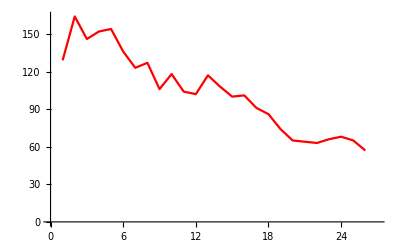

```mathematica
rSpotNPlot=Length/@redRunAvp//ListLinePlot[#,PlotStyle->Red, PlotRange->{{0,27},{0,All}}]&
```

### Linking red tracks

```mathematica
maxJumpDistRed=20;
```

```mathematica
myredtracks=LinkTracks2[redRunAvp,maxJumpDistRed];
StringForm["`` red tracks were found by allowing `` pixel jump, and the average length of the tracks is ``",myredtracks//Length,maxJumpDistRed,(Length/@myredtracks)//Mean//N]
```

371 red tracks were found by allowing 20 pixel jump, and the average length of the tracks is 4.43396

```mathematica
myredtracks>>analysisFolder<>"_redtracks.dat";
```

```mathematica
shortestTrackRed=10;
```

```mathematica
mylongredtracks=myredtracks//DeleteCases[#,x_/;Length[x]<shortestTrackRed]&;
StringForm["   `` red tracks are longer than ``, and the average length of the long tracks is ``",mylongredtracks//Length,shortestTrackRed,(Length/@mylongredtracks)//Mean//N]
```

9 red tracks are longer than 10, and the average length of the long tracks is 11.4444

```mathematica
mylongredtracksf=mylongredtracks⟦All,All,2⟧//Flatten[#,1]&//Sort//SplitBy[#,First]&;
```

```mathematica
Manipulate[Show[myColMovieRunAv⟦1,frame⟧//ImageAdjust[#,{0,0,1},thred]&,Graphics[{Red,Circle[#,7]&/@(mylongredtracksf⟦frame,All,2;;3⟧)}]],{frame,1,myMaxN,1}]
```

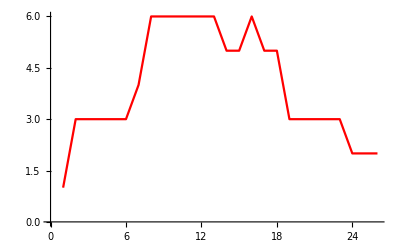

```mathematica
rSpotNPlot=Length/@mylongredtracksf//ListLinePlot[#,PlotStyle->Red]&
```

### Find Green Particles from Running z-averaged Movie (Green laser)

```mathematica
Manipulate[myColMovieRunAv⟦2,frame⟧//ImageAdjust[#,{0,0,1},{threshold1,threshold2}]&,
Button["Choose threshold such that the dots appear nicely and CLICK",thgreen={threshold1,threshold2}],
{frame,1,Length[myColMovieRunAv⟦2⟧],1},{{threshold1,0.001},0,0.4,0.001},{{threshold2,0.03},0,1,0.001}]
```

```mathematica
Manipulate[
max=BandPass[ImageMultiply[myColMovieRunAv⟦2, 1⟧ // ImageAdjust[#, {0, 0, 1}, thgreen] &,cytomask[[1]]],{lowpass,hipass}]//ImageData//Max;
imgb=BandPass[myColMovieRunAv⟦2, frame⟧ // ImageAdjust[#, {0, 0, 1}, thgreen] &,{lowpass,hipass}];
GraphicsRow[{myColMovieRunAv⟦2,frame⟧// ImageAdjust[#, {0, 0, 1}, thgreen]&,
SelectComponents[ImageMultiply[Binarize[imgb,max threshold],cytomask[[frame]]],"Count",lo<#<hi&]},ImageSize->900],
Button["Choose parameters and CLICK",{mymaxgreen=max,bandpassgreen={lowpass,hipass},thgreen2=threshold,dotsizegreen={lo,hi}}],
{frame,1,myMaxN,1},{{threshold,0.1},0,0.4,0.01},{{lowpass,1},0,10,1},{{hipass,7},0,30,1},{{lo,5},0,20,1},{{hi,100},10,500,1}]
```

```mathematica
greenRunAvp=Table[FindParticlesWeighted[myColMovieRunAv⟦2,frame⟧//ImageAdjust[#,{0,0,1},thgreen]&,bandpassgreen,mymaxgreen,thgreen2,cytomask[[frame]],dotsizegreen],{frame,1,myMaxN,1}];
StringForm["`` green particles were found.",greenRunAvp//Flatten[#,1]&//Length]
```

2274 green particles were found.

```mathematica
greenComponentMask=Table[FindParticlesWeightedMask[myColMovieRunAv⟦2,frame⟧//ImageAdjust[#,{0,0,1},thgreen]&,bandpassgreen,mymaxgreen,thgreen2,cytomask[[frame]],dotsizegreen],{frame,1,myMaxN,1}];
```

```mathematica
Manipulate[Show[myColMovieRunAv⟦2,frame⟧//ImageAdjust[#,{0,0,1},thgreen]&,Graphics[{Green,Circle[#,5]&/@(greenRunAvp⟦frame⟧)}],Graphics[{Red,Circle[#,7]&/@(redRunAvp⟦frame⟧)}]],
Button["CLICK if you want to save this dataset",greenRunAvp>>analysisFolder<>"_greenspots.dat";Export[analysisFolder<>"_greenComponentMask.tif",greenComponentMask];],
{frame,1,myMaxN,1}]
```

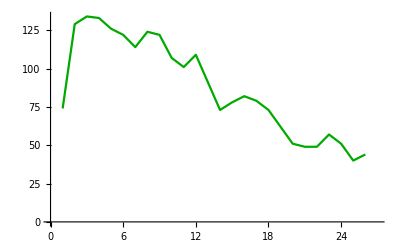

```mathematica
rSpotNPlot=Length/@greenRunAvp//ListLinePlot[#,PlotStyle->Darker[Green],PlotRange->{{0,27},{0,All}}]&
```

### Linking green tracks

```mathematica
maxJumpDistGreen=maxJumpDistRed;
```

```mathematica
mygreentracks=LinkTracks2[greenRunAvp,maxJumpDistGreen];
StringForm["   `` green tracks were found by allowing `` pixel jump, and the average length of the tracks is ``",mygreentracks//Length,maxJumpDistGreen,(Length/@mygreentracks)//Mean//N]
```

309 green tracks were found by allowing 20 pixel jump, and the average length of the tracks is 4.39482

```mathematica
mygreentracks>>analysisFolder<>"_greentracks.dat";
```

```mathematica
shortestTrackGreen=0;
```

```mathematica
mylonggreentracks=mygreentracks//DeleteCases[#,x_/;Length[x]<shortestTrackGreen]&;
StringForm["   `` green tracks are longer than ``, and the average length of the long tracks is ``",mylonggreentracks//Length,shortestTrackGreen,(Length/@mylonggreentracks)//Mean//N]
```

309 green tracks are longer than 0, and the average length of the long tracks is 4.39482

```mathematica
mylonggreentracksf=mylonggreentracks⟦All,All,2⟧//Flatten[#,1]&//Sort//SplitBy[#,First]&;
```

```mathematica
Manipulate[Show[myColMovieRunAv⟦2,frame⟧//ImageAdjust[#,{0,0,1},thgreen]&,Graphics[{Green,Circle[#,5]&/@(mylonggreentracksf⟦frame,All,2;;3⟧)}],Graphics[{Red,Circle[#,5]&/@(mylongredtracksf⟦frame,All,2;;3⟧)}]],{frame,1,myMaxN,1}]
```

```mathematica
mylonggreentracksf=mylonggreentracks⟦All,All,2⟧//Flatten[#,1]&//Sort//SplitBy[#,First]&;
```

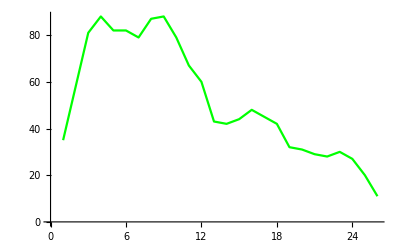

```mathematica
gSpotNPlot=Length/@mylonggreentracksf//ListLinePlot[#,PlotStyle->Green]&
```

```mathematica
(*Manipulate[Show[myColMovieRunAv⟦2,frame⟧//ImageAdjust[#,{0,0,1},thgreen]&,Graphics[{Green,PointSize[0.001],Point[#]&/@(mylonggreentracksf⟦1;;frame,All,2;;3⟧//Flatten[#,1]&)}],Graphics[{Red,Circle[#,7]&/@(mylonggreentracksf⟦frame,All,2;;3⟧)}]],{frame,1,myMaxN,1}]*)
```

### Find Blue Particles from Running z-averaged Movie (Blue laser)

```mathematica
Manipulate[myColMovieRunAv⟦3,frame⟧//ImageAdjust[#,{0,0,1},{threshold1,threshold2}]&,
Button["Choose threshold such that the dots appear nicely and CLICK",thblue={threshold1,threshold2}],
{frame,1,Length[myColMovieRunAv⟦3⟧],1},{{threshold1,0.001},0,0.4,0.001},{{threshold2,0.03},0,0.4,0.001}]
```

```mathematica
Manipulate[
max=BandPass[ImageMultiply[myColMovieRunAv⟦3, 1⟧ // ImageAdjust[#, {0, 0, 1}, thblue] &,cytomask[[1]]],{lowpass,hipass}]//ImageData//Max;
imgb=BandPass[myColMovieRunAv⟦3, frame⟧ // ImageAdjust[#, {0, 0, 1}, thblue] &,{lowpass,hipass}];
GraphicsRow[{myColMovieRunAv⟦3,frame⟧// ImageAdjust[#, {0, 0, 1}, thblue]&,
SelectComponents[ImageMultiply[Binarize[imgb,max threshold],cytomask[[frame]]],"Count",lo<#<hi&]},ImageSize->900],
Button["Choose parameters and CLICK",{mymaxblue=max,bandpassblue={lowpass,hipass},thblue2=threshold,dotsizeblue={lo,hi}}],
{frame,1,myMaxN,1},{{threshold,0.1},0,0.4,0.01},{{lowpass,1},0,10,1},{{hipass,6},0,10,1},{{lo,3},0,20,1},{{hi,200},50,500,1}]
```

```mathematica
blueRunAvp=Table[FindParticlesWeighted[myColMovieRunAv⟦3,frame⟧//ImageAdjust[#,{0,0,1},thblue]&,bandpassblue,mymaxblue,thblue2,cytomask[[frame]],
dotsizeblue],{frame,1,myMaxN,1}];
StringForm["`` blue particles were found.",blueRunAvp//Flatten[#,1]&//Length]
```

1765 blue particles were found.

```mathematica
blueComponentMask=Table[FindParticlesWeightedMask[myColMovieRunAv⟦3,frame⟧//ImageAdjust[#,{0,0,1},thblue]&,bandpassblue,mymaxblue,thblue2,cytomask[[frame]],dotsizeblue],{frame,1,myMaxN,1}];
```

```mathematica
Manipulate[Show[myColMovieRunAv⟦3,frame⟧//ImageAdjust[#,{0,0,1},thblue]&,Graphics[{Red,Circle[#,7]&/@(redRunAvp⟦frame⟧)}],Graphics[{Blue,Circle[#,7]&/@(blueRunAvp⟦frame⟧)}]],
Button["CLICK if you want to save this dataset",blueRunAvp>>analysisFolder<>"_bluespots.dat";Export[analysisFolder<>"_blueComponentMask.tif",blueComponentMask];],
{frame,1,myMaxN,1}]
```

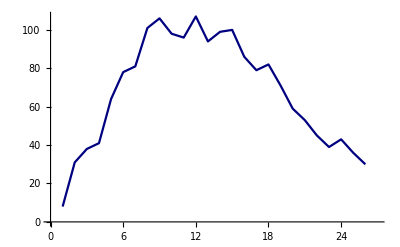

```mathematica
Length/@blueRunAvp//ListLinePlot[#,PlotStyle->Darker[Blue,0.5],PlotRange->{{0,27},{0,All}}]&
```

### Linking blue tracks

```mathematica
maxJumpDistBlue=maxJumpDistRed;
```

```mathematica
mybluetracks=LinkTracks2[blueRunAvp,maxJumpDistBlue];
StringForm["   `` blue tracks were found by allowing `` pixel jump, and the average length of the tracks is ``",mybluetracks//Length,maxJumpDistBlue,(Length/@mybluetracks)//Mean//N]
```

219 blue tracks were found by allowing 20 pixel jump, and the average length of the tracks is 4.46575

```mathematica
mybluetracks>>analysisFolder<>"_bluetracks.dat";
```

```mathematica
shortestTrackBlue=shortestTrackRed
```

10

```mathematica
mylongbluetracks=mybluetracks//DeleteCases[#,x_/;Length[x]<shortestTrackBlue]&;
StringForm["   `` blue tracks are longer than ``, and the average length of the long tracks is ``",mylongbluetracks//Length,shortestTrackBlue,(Length/@mylongbluetracks)//Mean//N]
```

6 blue tracks are longer than 10, and the average length of the long tracks is 11.3333

```mathematica
mylongbluetracksf=mylongbluetracks⟦All,All,2⟧//Flatten[#,1]&//Sort//SplitBy[#,First]&;
```

```mathematica
Manipulate[Show[myColMovieRunAv⟦3,frame⟧//ImageAdjust[#,{0,0,1},thblue]&,Graphics[{Red,Circle[#,5]&/@(mylongredtracksf⟦frame,All,2;;3⟧)}],
Graphics[{Green,Circle[#,5]&/@(mylonggreentracksf⟦frame,All,2;;3⟧)}],Graphics[{Blue,Circle[#,5]&/@(mylongbluetracksf⟦frame,All,2;;3⟧)}]],{frame,1,myMaxN,1}]
```

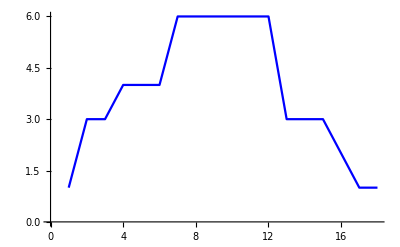

```mathematica
bSpotNPlot=Length/@mylongbluetracksf//ListLinePlot[#,PlotStyle->Blue]&
```

### Check all tracks (and double-check transformation function)

```mathematica
mylongredtracksColReg=mylongredtracks;
mylongredtracksColReg⟦All,All,2,2;;⟧=myTfFunc/@mylongredtracksColReg⟦All,All,2,2;;⟧;
```

```mathematica
Clear[mylongredtracksColRegf]
```

```mathematica
mylongredtracksColRegf=mylongredtracksColReg⟦All,All,2⟧//Flatten[#,1]&//Sort//SplitBy[#,First]&;
```

```mathematica
Manipulate[Show[
ColorCombine[{redComponentMask⟦frame⟧,greenComponentMask⟦frame⟧,blueComponentMask⟦frame⟧}],Graphics[{Red,Circle[#,5]&/@(mylongredtracksColRegf⟦frame,All,2;;3⟧)}],
Graphics[{Green,Circle[#,6]&/@(mylonggreentracksf⟦frame,All,2;;3⟧)}],Graphics[{Blue,Circle[#,7]&/@(mylongbluetracksf⟦frame,All,2;;3⟧)}]],{frame,1,myMaxN,1}];
```

```mathematica
thred=thblue
```

{0.001,0.117}

```mathematica
Manipulate[Show[{myColMovieRunAv⟦3,frame⟧//ImageAdjust[#,{0,0,1},thred*2]&,Graphics[{Blue,Circle[#,7]&/@(mylongbluetracksf⟦frame,All,2;;3⟧)}]}],{frame,1,myMaxN,1}];
```

```mathematica
Manipulate[Show[
ColorCombine[{myColMovieRunAv⟦1,frame⟧//ImageAdjust[#,{0,0,1},thred]&,myColMovieRunAv⟦2,frame⟧//ImageAdjust[#,{0,0,1},thgreen]&,myColMovieRunAv⟦3,frame⟧//ImageAdjust[#,{0,0,1},thblue]&}],Graphics[{Red,Circle[#,5]&/@(mylongredtracksColRegf⟦frame,All,2;;3⟧)}],
Graphics[{Green,Circle[#,6]&/@(mylonggreentracksf⟦frame,All,2;;3⟧)}],Graphics[{Blue,Circle[#,7]&/@(mylongbluetracksf⟦frame,All,2;;3⟧)}]],{frame,1,myMaxN,1}];
```

```mathematica
(*Manipulate[Show[myColMovieRunAv⟦3,frame⟧//ImageAdjust[#,{0,0,1},thblue]&,Graphics[{Blue,PointSize[0.001],Point[#]&/@(mylongbluetracksf⟦1;;frame,All,2;;3⟧//Flatten[#,1]&)}],Graphics[{Red,Circle[#,7]&/@(mylongbluetracksf⟦frame,All,2;;3⟧)}]],{frame,1,myMaxN,1}]*)
```

### Linking red, blue, and green tracks

```mathematica
tracksr=Map[Append[#,{1,0,0}]&,mylongredtracksColReg,{2}];
tracksr⟦All,All,1⟧=Range@Length@tracksr;
tracksg=Map[Append[#,{0,1,0}]&,mylonggreentracks,{2}];
tracksg⟦All,All,1⟧=Range@Length@tracksg;
tracksb=Map[Append[#,{0,0,1}]&,mylongbluetracks,{2}];
tracksb⟦All,All,1⟧=Range@Length@tracksb;
```

```mathematica
minOverlapTime=5;
maxOverlapDistance=3;(*in pixels*)
```

```mathematica
{newTracksr,newTracksg,newTracksb}=Connect3Colors[tracksr,tracksg,tracksb,minOverlapTime,maxOverlapDistance];
```

```mathematica
Prepend[Thread@{{"Red","Green","Blue"},Length/@{tracksr,tracksg,tracksb},Length/@{newTracksr,newTracksg,newTracksb}},{"The # of Tracks","Before Linking","After Linking"}]//MatrixForm
```

(The # of Tracks | Before Linking | After Linking
Red | 9 | 9
Green | 309 | 309
Blue | 6 | 6)

```mathematica
newTracksr>>analysisFolder<>"_RedTracksColorLinked.dat";
newTracksg>>analysisFolder<>"_GreenTracksColorLinked.dat";
newTracksb>>analysisFolder<>"_BlueTracksColorLinked.dat";
```

### Hand Checking

#### Setting Parameters and Creating Inverse Function of Transformation Function

```mathematica
dist=15;time=10;
```

```mathematica
myTfFuncInv=InverseFunction@myTfFunc;
```

#### Hand Checking Red

```mathematica
myHandCheckedTracksr=newTracksr;
myHandCheckedTracksr⟦All,All,2,2;;⟧=myTfFuncInv/@myHandCheckedTracksr⟦All,All,2,2;;⟧;
```

```mathematica
Manipulate[
{listConnectTracks,posiConnectTracks}=FindConnectableTracks2[myHandCheckedTracksr,myMaxN,dist,time,trackN];
Column@{Show[myColMovieRunAv⟦channel,frame⟧//ImageAdjust[#,{0,0,1},If[channel==1,thred,If[channel==2,thgreen,thblue]]]&,
Graphics[{Red,Circle[#,7]&/@(posiConnectTracks⟦frame,2,All,{2,3}⟧),Green,Inset[#⟦1⟧,#⟦2⟧-{10,10}]&/@(Thread@{posiConnectTracks⟦frame,2,All,1⟧,posiConnectTracks⟦frame,2,All,{2,3}⟧})}]],
"",
Prepend[Prepend[Thread@{"track "<>#&/@CharacterRange["A","F"]⟦;;Length@listConnectTracks-1⟧,
"track " <>#&/@ToString/@listConnectTracks⟦2;;⟧,myHandCheckedTracksr⟦listConnectTracks⟦2;;⟧,1,2,1⟧,(Last/@myHandCheckedTracksr⟦listConnectTracks⟦2;;⟧⟧)⟦All,2,1⟧},{"Current track","track " <>ToString@trackN,myHandCheckedTracksr⟦trackN,1,2,1⟧,(Last@myHandCheckedTracksr⟦trackN⟧)⟦2,1⟧}],{"track","track number","Start","End"}]//TableForm,
"",
"The number of all tracks is "<>ToString@Length@myHandCheckedTracksr},
Button["Click to Connect",
chosenTracks=Prepend[listConnectTracks⟦1+Position[{trackA,trackB,trackC,trackD,trackE,trackF},True]//Flatten⟧,trackN];
myHandCheckedTracksr=ConnectTracksFilled[myHandCheckedTracksr,chosenTracks];
(*Print@Position[Dynamic/@(ToExpression/@("track"<>#&/@CharacterRange["A","F"])),True]*)],
Button["Remove This Point"],
Button["Split Tracks from This Frame"],
Button["Delete This Track",myHandCheckedTracksr=Delete[myHandCheckedTracksr,trackN]],
{{channel,1},{1,2,3}},{trackN,1,Length@myHandCheckedTracksr,1},{frame,1,myMaxN,1},{trackA,{False,True}},{trackB,{False,True}},{trackC,{False,True}},{trackD,{False,True}},{trackE,{False,True}},{trackF,{False,True}}]
```

```mathematica
myHandCheckedTracksr>>analysisFolder<>"_RedTracksHandChecked.dat";
```

#### Hand Checking Green

```mathematica
myHandCheckedTracksg=newTracksg;
```

```mathematica
Manipulate[
{listConnectTracks,posiConnectTracks}=FindConnectableTracks2[myHandCheckedTracksg,myMaxN,dist,time,trackN];
Column@{Show[myColMovieRunAv⟦channel,frame⟧//ImageAdjust[#,{0,0,1},If[channel==1,thred,If[channel==2,thgreen,thblue]]]&,
Graphics[{Red,Circle[#,7]&/@(posiConnectTracks⟦frame,2,All,{2,3}⟧),Green,Inset[#⟦1⟧,#⟦2⟧-{10,10}]&/@(Thread@{posiConnectTracks⟦frame,2,All,1⟧,posiConnectTracks⟦frame,2,All,{2,3}⟧})}]],
"",
Prepend[Prepend[Thread@{"track "<>#&/@CharacterRange["A","F"]⟦;;Length@listConnectTracks-1⟧,
"track " <>#&/@ToString/@listConnectTracks⟦2;;⟧,myHandCheckedTracksg⟦listConnectTracks⟦2;;⟧,1,2,1⟧,(Last/@myHandCheckedTracksg⟦listConnectTracks⟦2;;⟧⟧)⟦All,2,1⟧},{"Current track","track " <>ToString@trackN,myHandCheckedTracksg⟦trackN,1,2,1⟧,(Last@myHandCheckedTracksg⟦trackN⟧)⟦2,1⟧}],{"track","track number","Start","End"}]//TableForm,
"",
"The number of all tracks is "<>ToString@Length@myHandCheckedTracksg},
Button["Click to Connect",
chosenTracks=Prepend[listConnectTracks⟦1+Position[{trackA,trackB,trackC,trackD,trackE,trackF},True]//Flatten⟧,trackN];
myHandCheckedTracksg=ConnectTracksFilled[myHandCheckedTracksg,chosenTracks];
(*Print@Position[Dynamic/@(ToExpression/@("track"<>#&/@CharacterRange["A","F"])),True]*)],
Button["Remove This Point"],
Button["Split Tracks from This Frame"],
Button["Delete This Track",myHandCheckedTracksg=Delete[myHandCheckedTracksg,trackN]],
{{channel,2},{1,2,3}},{trackN,1,Length@myHandCheckedTracksg,1},{frame,1,myMaxN,1},{trackA,{False,True}},{trackB,{False,True}},{trackC,{False,True}},{trackD,{False,True}},{trackE,{False,True}},{trackF,{False,True}}]
```

```mathematica
myHandCheckedTracksg>>analysisFolder<>"_GreenTracksHandChecked.dat";
```

#### Hand Checking Blue

```mathematica
myHandCheckedTracksb=newTracksb;
```

```mathematica
Manipulate[
{listConnectTracks,posiConnectTracks}=FindConnectableTracks2[myHandCheckedTracksb,myMaxN,dist,time,trackN];
Column@{Show[myColMovieRunAv⟦channel,frame⟧//ImageAdjust[#,{0,0,1},If[channel==1,thred,If[channel==2,thgreen,thblue]]]&,
Graphics[{Red,Circle[#,7]&/@(posiConnectTracks⟦frame,2,All,{2,3}⟧),Green,Inset[#⟦1⟧,#⟦2⟧-{10,10}]&/@(Thread@{posiConnectTracks⟦frame,2,All,1⟧,posiConnectTracks⟦frame,2,All,{2,3}⟧})}]],
"",
Prepend[Prepend[Thread@{"track "<>#&/@CharacterRange["A","F"]⟦;;Length@listConnectTracks-1⟧,
"track " <>#&/@ToString/@listConnectTracks⟦2;;⟧,myHandCheckedTracksb⟦listConnectTracks⟦2;;⟧,1,2,1⟧,(Last/@myHandCheckedTracksb⟦listConnectTracks⟦2;;⟧⟧)⟦All,2,1⟧},{"Current track","track " <>ToString@trackN,myHandCheckedTracksb⟦trackN,1,2,1⟧,(Last@myHandCheckedTracksb⟦trackN⟧)⟦2,1⟧}],{"track","track number","Start","End"}]//TableForm,
"",
"The number of all tracks is "<>ToString@Length@myHandCheckedTracksb},
Button["Click to Connect",
chosenTracks=Prepend[listConnectTracks⟦1+Position[{trackA,trackB,trackC,trackD,trackE,trackF},True]//Flatten⟧,trackN];
myHandCheckedTracksb=ConnectTracksFilled[myHandCheckedTracksb,chosenTracks];
(*Print@Position[Dynamic/@(ToExpression/@("track"<>#&/@CharacterRange["A","F"])),True]*)],
Button["Remove This Point"],
Button["Split Tracks from This Frame"],
Button["Delete This Track",myHandCheckedTracksb=Delete[myHandCheckedTracksb,trackN]],
{{channel,3},{1,2,3}},{trackN,1,Length@myHandCheckedTracksb,1},{frame,1,myMaxN,1},{trackA,{False,True}},{trackB,{False,True}},{trackC,{False,True}},{trackD,{False,True}},{trackE,{False,True}},{trackF,{False,True}}]
```

```mathematica
myHandCheckedTracksb>>analysisFolder<>"_BlueTracksHandChecked.dat";
```

### Fitting Tracks with Gaussian

#### Setting Parameters

```mathematica
pad=5;
myTrimSize=2*pad+1;
```

#### Fitting red tracks with Gaussian

```mathematica
{myRedAllParameters,myRedPos,myRedData}=ParticleFittingFixedSigma[myColMovie,1,myHandCheckedTracksr,pad,myTrimSize,1.5,avgFrameN];
```

```mathematica
{myRedAllParameters,myRedPos,myRedData}>>analysisFolder<>"_redfits.dat";
```

```mathematica
{myRedAllParameters,myRedPos,myRedData}=<<(analysisFolder<>"_redfits.dat");
```

```mathematica
myRedAllParametersColReg=myRedAllParameters;
myRedAllParametersColReg⟦All,3;;4⟧=myTfFunc/@myRedAllParameters⟦All,3;;4⟧;
```

```mathematica
mylabel={"TrackN","FrameN","X (130 nm pixels)","Y (130 nm pixels)","Peak intensity","Background intensity","SigmaX (130 nm pixels)", "SigmaY (130 nm pixels)","X min 90% confidence interval (130 nm pixels)","X max 90% confidence interval (130 nm pixels)","Y min 90% confidence interval (130 nm pixels)","Y max 90% confidence interval (130 nm pixels)","Peak intensity min 90% confidence interval","Peak intensity max 90% confidence interval","Background intensity min 90% confidence interval","Background max 90% confidence interval","SigmaX min 90% confidence interval (130 nm pixels)","SigmaX max 90% confidence interval (130 nm pixels)","SigmaY min 90% confidence interval (130 nm pixels)","SigmaY max 90% confidence interval (130 nm pixels)","R","G","B"};
myRedAllParametersColRegLabeled=Insert[myRedAllParametersColReg,mylabel,1];
```

```mathematica
Export[analysisFolder<>"_FixedSigmaRedAllParameters.xls",myRedAllParametersColRegLabeled];
```

#### Fitting green tracks with Gaussian

```mathematica
mylabel={"TrackN","FrameN","X (130 nm pixels)","Y (130 nm pixels)","Peak intensity","Background intensity","SigmaX (130 nm pixels)", "SigmaY (130 nm pixels)","X min 90% confidence interval (130 nm pixels)","X max 90% confidence interval (130 nm pixels)","Y min 90% confidence interval (130 nm pixels)","Y max 90% confidence interval (130 nm pixels)","Peak intensity min 90% confidence interval","Peak intensity max 90% confidence interval","Background intensity min 90% confidence interval","Background max 90% confidence interval","SigmaX min 90% confidence interval (130 nm pixels)","SigmaX max 90% confidence interval (130 nm pixels)","SigmaY min 90% confidence interval (130 nm pixels)","SigmaY max 90% confidence interval (130 nm pixels)","R","G","B"};
```

```mathematica
{myGreenAllParameters,myGreenPos,myGreenData}=ParticleFittingFixedSigma[myColMovie,2,myHandCheckedTracksg,pad,myTrimSize,1.5,avgFrameN];
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NonlinearModelFit::cvmit will be suppressed during this calculation.

```mathematica
{myGreenAllParameters,myGreenPos,myGreenData}>>analysisFolder<>"_greenfits.dat";
```

```mathematica
{myGreenAllParameters,myGreenPos,myGreenData}=<<(analysisFolder<>"_greenfits.dat");
```

```mathematica
myGreenAllParametersLabeled=Insert[myGreenAllParameters,mylabel,1];
```

```mathematica
Export[analysisFolder<>"_FixedSigmaGreenAllParameters.xls",myGreenAllParametersLabeled];
```

#### Fitting blue tracks with Gaussian

```mathematica
mylabel={"TrackN","FrameN","X (130 nm pixels)","Y (130 nm pixels)","Peak intensity","Background intensity","SigmaX (130 nm pixels)", "SigmaY (130 nm pixels)","X min 90% confidence interval (130 nm pixels)","X max 90% confidence interval (130 nm pixels)","Y min 90% confidence interval (130 nm pixels)","Y max 90% confidence interval (130 nm pixels)","Peak intensity min 90% confidence interval","Peak intensity max 90% confidence interval","Background intensity min 90% confidence interval","Background max 90% confidence interval","SigmaX min 90% confidence interval (130 nm pixels)","SigmaX max 90% confidence interval (130 nm pixels)","SigmaY min 90% confidence interval (130 nm pixels)","SigmaY max 90% confidence interval (130 nm pixels)","R","G","B"};
```

```mathematica
{myBlueAllParameters,myBluePos,myBlueData}=ParticleFittingFixedSigma[myColMovie,3,myHandCheckedTracksb,pad,myTrimSize,1.5,avgFrameN];
```

```mathematica
{myBlueAllParameters,myBluePos,myBlueData}>>analysisFolder<>"_bluefits.dat";
```

```mathematica
{myBlueAllParameters,myBluePos,myBlueData}=<<(analysisFolder<>"_bluefits.dat");
```

```mathematica
myBlueAllParametersLabeled=Insert[myBlueAllParameters,mylabel,1];
```

```mathematica
Export[analysisFolder<>"_FixedSigmaBlueAllParameters.xls",myBlueAllParametersLabeled];
```

### Saving parameters

```mathematica
mylabelParameters4xls={"Running Average Size","Lower Threshold Red #1","Higher Threshold Red #1","Threshold Red #2","Lower BandPass Red","Higher BandPass Red","Lower Excluded Particle Size Red","Higher Excluded Particle Size Red","Detected Red Particles","Maximum Jump Distance for Red","Detected Red Tracks","Average Length of Red Tracks","Shortest Length for Red Long Tracks","Detected Red Long Tracks","Average Length of Red Long Tracks","Lower Threshold Green #1","Higher Threshold Green #1","Threshold Green #2","Lower BandPass Green","Higher BandPass Green","Lower Excluded Particle Size Green","Higher Excluded Particle Size Green","Detected Green Particles","Maximum Jump Distance for Green","Detected Green Tracks","Average Length of Green Tracks","Shortest Length for Green Long Tracks","Detected Green Long Tracks","Average Length of Green Long Tracks","Lower Threshold Blue #1","Higher Threshold Blue #1","Threshold Blue #2","Lower BandPass Blue","Higher BandPass Blue","Lower Excluded Particle Size Blue","Higher Excluded Particle Size Blue","Detected Blue Particles","Maximum Jump Distance for Blue","Detected Blue Tracks","Average Length of Blue Tracks","Shortest Length for Blue Long Tracks","Detected Blue Long Tracks","Average Length of Blue Long Tracks","Pad Size for Fitting"
};
myParameters={avgFrameN,thred⟦1⟧,thred⟦2⟧,thred2,bandpassred⟦1⟧,bandpassred⟦2⟧,dotsizered⟦1⟧,dotsizered⟦2⟧,redRunAvp//Flatten[#,1]&//Length,maxJumpDistRed,myredtracks//Length,(Length/@myredtracks)//Mean//N,shortestTrackRed,mylongredtracks//Length,(Length/@mylongredtracks)//Mean//N,thgreen⟦1⟧,thgreen⟦2⟧,thgreen2,bandpassgreen⟦1⟧,bandpassgreen⟦2⟧,dotsizegreen⟦1⟧,dotsizegreen⟦2⟧,greenRunAvp//Flatten[#,1]&//Length,maxJumpDistGreen,mygreentracks//Length,(Length/@mygreentracks)//Mean//N,shortestTrackGreen,mylonggreentracks//Length,(Length/@mylonggreentracks)//Mean//N,thblue⟦1⟧,thblue⟦2⟧,thblue2,bandpassblue⟦1⟧,bandpassblue⟦2⟧,dotsizeblue⟦1⟧,dotsizeblue⟦2⟧,blueRunAvp//Flatten[#,1]&//Length,maxJumpDistBlue,mybluetracks//Length,(Length/@mybluetracks)//Mean//N,shortestTrackBlue,mylongbluetracks//Length,(Length/@mylongbluetracks)//Mean//N,pad};
Export[analysisFolder<>"_allParameters.xls",Thread@{mylabelParameters4xls,myParameters}];
```

```mathematica
mylabelParameters={"Running Average Size","Threshold Red #1","Threshold Red #2","BandPass Red","Excluded Particle Size Red","Detected Red Particles","Maximum Jump Distance for Red","Detected Red Tracks","Average Length of Red Tracks","Shortest Length for Red Long Tracks","Detected Red Long Tracks","Average Length of Red Long Tracks","Threshold Green #1","Threshold Green #2","BandPass Green","Excluded Particle Size Green","Detected Green Particles","Maximum Jump Distance for Green","Detected Green Tracks","Average Length of Green Tracks","Shortest Length for Green Long Tracks","Detected Green Long Tracks","Average Length of Green Long Tracks","Threshold Blue #1","Threshold Blue #2","BandPass Blue","Excluded Particle Size Blue","Detected Blue Particles","Maximum Jump Distance for Blue","Detected Blue Tracks","Average Length of Blue Tracks","Shortest Length for Blue Long Tracks","Detected Blue Long Tracks","Average Length of Blue Long Tracks","Pad Size for Fitting"};
myParameters={avgFrameN,thred,thred2,bandpassred,dotsizered,redRunAvp//Flatten[#,1]&//Length,maxJumpDistRed,myredtracks//Length,(Length/@myredtracks)//Mean//N,shortestTrackRed,mylongredtracks//Length,(Length/@mylongredtracks)//Mean//N,thgreen,thgreen2,bandpassgreen,dotsizegreen,greenRunAvp//Flatten[#,1]&//Length,maxJumpDistGreen,mygreentracks//Length,(Length/@mygreentracks)//Mean//N,shortestTrackGreen,mylonggreentracks//Length,(Length/@mylonggreentracks)//Mean//N,thblue,thblue2,bandpassblue,dotsizeblue,blueRunAvp//Flatten[#,1]&//Length,maxJumpDistBlue,mybluetracks//Length,(Length/@mybluetracks)//Mean//N,shortestTrackBlue,mylongbluetracks//Length,(Length/@mylongbluetracks)//Mean//N,pad};
Thread@{mylabelParameters,myParameters}>>analysisFolder<>"_allParameters.dat";
Export[DirectoryName[mymoviefile]<>"TransformationFunction.m",myTfFunc];
```

```mathematica
mylabelParameters={"Running Average Size","Threshold Red #1","Threshold Red #2","BandPass Red","Excluded Particle Size Red","Detected Red Particles","Maximum Jump Distance for Red","Detected Red Tracks","Average Length of Red Tracks","Shortest Length for Red Long Tracks","Detected Red Long Tracks","Average Length of Red Long Tracks","Threshold Green #1","Threshold Green #2","BandPass Green","Excluded Particle Size Green","Detected Green Particles","Maximum Jump Distance for Green","Detected Green Tracks","Average Length of Green Tracks","Shortest Length for Green Long Tracks","Detected Green Long Tracks","Average Length of Green Long Tracks","Threshold Blue #1","Threshold Blue #2","BandPass Blue","Excluded Particle Size Blue","Detected Blue Particles","Maximum Jump Distance for Blue","Detected Blue Tracks","Average Length of Blue Tracks","Shortest Length for Blue Long Tracks","Detected Blue Long Tracks","Average Length of Blue Long Tracks","Pad Size for Fitting"};
myParameters={avgFrameN,thred,thred2,bandpassred,dotsizered,redRunAvp//Flatten[#,1]&//Length,maxJumpDistRed,myredtracks//Length,(Length/@myredtracks)//Mean//N,shortestTrackRed,mylongredtracks//Length,(Length/@mylongredtracks)//Mean//N,thgreen,thgreen2,bandpassgreen,dotsizegreen,greenRunAvp//Flatten[#,1]&//Length,maxJumpDistGreen,mygreentracks//Length,(Length/@mygreentracks)//Mean//N,shortestTrackGreen,mylonggreentracks//Length,(Length/@mylonggreentracks)//Mean//N,thblue,thblue2,bandpassblue,dotsizeblue,blueRunAvp//Flatten[#,1]&//Length,maxJumpDistBlue,mybluetracks//Length,(Length/@mybluetracks)//Mean//N,shortestTrackBlue,mylongbluetracks//Length,(Length/@mylongbluetracks)//Mean//N,pad};
Thread@{mylabelParameters,myParameters}//TableForm
```

Running Average Size | 1
Threshold Red #1 | 0.001
0.117
Threshold Red #2 | 0.09
BandPass Red | 1
7
Excluded Particle Size Red | 3
100
Detected Red Particles | 2686
Maximum Jump Distance for Red | 20
Detected Red Tracks | 371
Average Length of Red Tracks | 4.43396
Shortest Length for Red Long Tracks | 10
Detected Red Long Tracks | 9
Average Length of Red Long Tracks | 11.4444
Threshold Green #1 | 0.005
0.173
Threshold Green #2 | 0.1
BandPass Green | 1
7
Excluded Particle Size Green | 5
100
Detected Green Particles | 2274
Maximum Jump Distance for Green | 20
Detected Green Tracks | 309
Average Length of Green Tracks | 4.39482
Shortest Length for Green Long Tracks | 0
Detected Green Long Tracks | 309
Average Length of Green Long Tracks | 4.39482
Threshold Blue #1 | 0.001
0.117
Threshold Blue #2 | 0.16
BandPass Blue | 1
3
Excluded Particle Size Blue | 8
200
Detected Blue Particles | 1765
Maximum Jump Distance for Blue | 20
Detected Blue Tracks | 219
Average Length of Blue Tracks | 4.46575
Shortest Length for Blue Long Tracks | 10
Detected Blue Long Tracks | 6
Average Length of Blue Long Tracks | 11.3333
Pad Size for Fitting | 5

```mathematica
tracksr111=Sort[Cases[newTracksr,x_/;x⟦1,3⟧=={1,1,1}&&Length@x>150],#1⟦1,2,2⟧<#2⟦1,2,2⟧&];tracksg111=Sort[Cases[newTracksg,x_/;x⟦1,3⟧=={1,1,1}&&Length@x>150],#1⟦1,2,2⟧<#2⟦1,2,2⟧&];
tracksb111=Sort[Cases[newTracksb,x_/;x⟦1,3⟧=={1,1,1}&&Length@x>150],#1⟦1,2,2⟧<#2⟦1,2,2⟧&];
```

```mathematica
Thread@{tracksg111⟦All,1,2,2;;⟧,tracksb111⟦All,1,2,2;;⟧,tracksr111⟦All,1,2,2;;⟧}//MatrixForm
```

{}

### Make Colors Files (uses Gaussian fit)

#### Parameters

```mathematica
minOverlapTime=5; (*in frames*)
maxOverlapDistance=3;(*in pixels*)
```

#### White File

```mathematica
redTracksWOff=myRedAllParameters//Cases[#,x_/;x[[21]]==1&&x[[22]]==1&&x[[23]]==1]&//SplitBy[#,First]&;
greenTracksW=myGreenAllParameters//Cases[#,x_/;x[[21]]==1&&x[[22]]==1&&x[[23]]==1]&//SplitBy[#,First]&;
blueTracksW=myBlueAllParameters//Cases[#,x_/;x[[21]]==1&&x[[22]]==1&&x[[23]]==1]&//SplitBy[#,First]&;
```

```mathematica
redTracksW=redTracksWOff;
redTracksW⟦All,All,3;;4⟧=myTfFunc/@redTracksW⟦All,All,3;;4⟧;
```

Find Green/Blue links:

```mathematica
myWGBLink=Table[
tempTrack1=greenTracksW⟦i,All,1;;7⟧;
tempTrack2=blueTracksW⟦j,All,1;;7⟧;
FindOverlapDist[tempTrack1,tempTrack2,minOverlapTime],{i,1,Length@greenTracksW,1},{j,1,Length@blueTracksW,1}];
myWGBLinkList=CrossPairFinder[Position[myWGBLink,x_/;0≤x<maxOverlapDistance]]
```

{}

Find Green/Red links:

```mathematica
myWGRLink=Table[
tempTrack1=greenTracksW⟦i,All,1;;7⟧;
tempTrack2=redTracksW⟦j,All,1;;7⟧;
FindOverlapDist[tempTrack1,tempTrack2,minOverlapTime],{i,1,Length@greenTracksW,1},{j,1,Length@redTracksW,1}];
myWGRLinkList=CrossPairFinder[Position[myWGRLink,x_/;0≤x<maxOverlapDistance]]
```

{}

```mathematica
myNewWGRLinkList=Intersection[myWGRLinkList,myWGBLinkList,SameTest->(#1⟦1⟧==#2⟦1⟧&)]
```

{}

```mathematica
(*RGBLinks=Table[{myWGRLinkList[[i,2,1]],myWGBLinkList[[i,1,1]],myWGBLinkList[[i,2,1]]},{i,1,Length[myWGBLinkList],1}] Old code fixed by Ken*)
(* If[Length@myWGBLinkList<Length@myWGRLinkList,myWGRLinkList=myWGRLinkList[[DeleteCases[myWGBLinkList[[All,1]],myWGRLinkList[[All,1]]]//Flatten]],myWGBLinkList=myWGBLinkList[[DeleteCases[myWGRLinkList[[All,1]],myWGBLinkList[[All,1]]]//Flatten]]];
RGBLinks=Table[{myWGRLinkList[[i,2,1]],myWGBLinkList[[i,1,1]],myWGBLinkList[[i,2,1]]},{i,1,Length[myWGBLinkList],1}](*Input an If statement that will delete the cases missing from either WGRLinkList or WGBLinkList, whichever one is longer*) Ken's fix to Tim's code*)
```

```mathematica
(*Tim's new code that hopefully will always work*)
myNewWGBLinkList=Intersection[myWGBLinkList,myWGRLinkList,SameTest->(#1⟦1⟧==#2⟦1⟧&)] (*this ensure lists have same length and refer to same green points*)
```

{}

Find Red/Green/Blue Links by linking Green/Red and Green/Blue:

```mathematica
RGBLinks=Table[{myNewWGRLinkList[[i,2,1]],myNewWGBLinkList[[i,1,1]],myNewWGBLinkList[[i,2,1]]},{i,1,Length[myNewWGBLinkList],1}]
```

{}

```mathematica
(*RGBLinks=Table[{myWGRLinkList[[i,2,1]],myWGBLinkList[[i,1,1]],myWGBLinkList[[i,2,1]]},{i,1,Length[myWGBLinkList],1}] Old code fixed by Ken*)
```

```mathematica
Clear[minTR,minTG,minTB,maxTR,maxTG,maxTB,myTRange,startRed,endRed,curRed,curGreen,curBlue];
listHead={"TrackN_Red","TrackN_Green","TrackN_Blue","FrameN","I_Red","I_Green","I_Blue","Dist_RG", "Dist_RB","Dist_GB","Step","MSD","X_Red","Y_Red","X_Green","Y_Green","X_Blue","Y_Blue","(dx_Red^2+dy_Red^2)^1/2","(dx_Green^2+dy_Green^2)^1/2","(dx_Blue^2+dy_Blue^2)^1/2"};
(*i is the White Track Number iterator*)
(*j is the Frame Number iterator, i.e. time*)
(*This is the range of frames that all tracks have*)
myWhiteColorParameters=Table[
minTR=Min[redTracksW⟦RGBLinks⟦i,1⟧,All,2⟧];
minTG=Min[greenTracksW⟦RGBLinks⟦i,2⟧,All,2⟧];
minTB=Min[blueTracksW⟦RGBLinks⟦i,3⟧,All,2⟧];
maxTR=Max[redTracksW⟦RGBLinks⟦i,1⟧,All,2⟧];
maxTG=Max[greenTracksW⟦RGBLinks⟦i,2⟧,All,2⟧];
maxTB=Max[blueTracksW⟦RGBLinks⟦i,3⟧,All,2⟧];
myTRange={Max[{minTR,minTG,minTB}],Min[{maxTR,maxTG,maxTB}]}; (*This is the range of frames that all tracks have*)
startRed=Cases[redTracksW⟦RGBLinks⟦i,1⟧⟧,x_/;x⟦2⟧==myTRange⟦1⟧];(*First frame*)
endRed=Cases[redTracksW⟦RGBLinks⟦i,1⟧⟧,x_/;x⟦2⟧==myTRange⟦2⟧]; (*Last frame*)
Table[
curRed=Cases[redTracksW⟦RGBLinks⟦i,1⟧⟧,x_/;j≤x⟦2⟧≤j+1]; (*current frame*)
curGreen=Cases[greenTracksW⟦RGBLinks⟦i,2⟧⟧,x_/;j≤x⟦2⟧≤j+1]; (*current frame*)
curBlue=Cases[blueTracksW⟦RGBLinks⟦i,3⟧⟧,x_/;j≤x⟦2⟧≤j+1]; (*current frame*)
(*Just in case red/green/blue couldn't be tracked or blinked in this frame*)
If[curRed≠{}&&curGreen≠{}&&curBlue≠{},  
(*OUTPUT COLUMNS FOR FILE*)
{curRed⟦1,1⟧,
curGreen⟦1,1⟧,
curBlue⟦1,1⟧,curRed⟦1,2⟧, curRed⟦1,5⟧,curGreen⟦1,5⟧,curBlue⟦1,5⟧, EuclideanDistance[curRed⟦1,3;;4⟧,curGreen⟦1,3;;4⟧],EuclideanDistance[curRed⟦1,3;;4⟧,curBlue⟦1,3;;4⟧],EuclideanDistance[curGreen⟦1,3;;4⟧,curBlue⟦1,3;;4⟧],If[Length[curRed]==2, EuclideanDistance[curRed⟦1,3;;4⟧,curRed⟦2,3;;4⟧],""],EuclideanDistance[curRed⟦1,3;;4⟧,startRed⟦1,3;;4⟧]^2,curRed⟦1,3⟧,curRed⟦1,4⟧,curGreen⟦1,3⟧,curGreen⟦1,4⟧,curBlue⟦1,3⟧,curBlue⟦1,4⟧,
√((curRed⟦1,10⟧-curRed⟦1,9⟧)^2+(curRed⟦1,12⟧-curRed⟦1,11⟧)^2)//N,
√((curGreen⟦1,10⟧-curGreen⟦1,9⟧)^2+(curGreen⟦1,12⟧-curGreen⟦1,11⟧)^2)//N,√((curBlue⟦1,10⟧-curBlue⟦1,9⟧)^2+(curBlue⟦1,12⟧-curBlue⟦1,11⟧)^2)//N
}],{j,myTRange⟦1⟧,myTRange⟦2⟧,1}]//DeleteCases[#,Null]&,{i,1,Length[RGBLinks],1}];
```

```mathematica
myWhiteColorParameters>>analysisFolder<>"_FixedSigmaWhiteColorParameters.dat";
```

```mathematica
Export[analysisFolder<>"_FixedSigmaWhiteColorParameters.xlsx",Prepend[myWhiteColorParameters//Flatten[#,1]&,listHead]]
```

/Volumes/MINI/_long_timeframe_transient_mini/20171203_14h/Analysis/MAX_TA32_FixedSigmaWhiteColorParameters.xlsx

```mathematica
ListPlot[Mean/@(DeleteCases[#,""]&/@Transpose[(PadRight[#,100,""]&/@myWhiteColorParameters[[All,All,12]])])]
```

Transpose::nmtx: The first two levels of {} cannot be transposed.

ListPlot::lpn: Transpose[Mean[{}]] is not a list of numbers or pairs of numbers.

ListPlot[Transpose[Mean[{}]]]

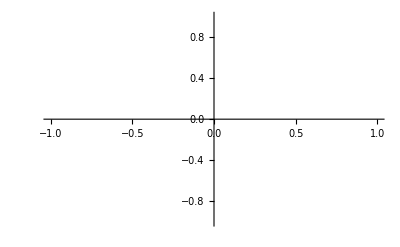

```mathematica
whitePlot=If[myWhiteColorParameters≠{},Show[Table[{myWhiteColorParameters[[myt,All,13;;14]],myWhiteColorParameters[[myt,All,15;;16]],myWhiteColorParameters[[myt,All,17;;18]]}//ListPlot[#,Joined->True,PlotStyle->{LightGray}]&,{myt,1,Length[myWhiteColorParameters],1}],PlotRange->{{0,512},{0,512}},Frame->True,AxesOrigin->{0,0},AspectRatio->{1,1}],
{{0,0}}//ListPlot[#,Joined->True,PlotStyle->{LightGray}]&
]
```

```mathematica
whitePlot>>analysisFolder<>"_whitePlot.dat";
```

#### Yellow File

```mathematica
redTracksWOff=myRedAllParameters//Cases[#,x_/;x[[21]]==1&&x[[22]]==1&&x[[23]]==0]&//SplitBy[#,First]&;
greenTracksW=myGreenAllParameters//Cases[#,x_/;x[[21]]==1&&x[[22]]==1&&x[[23]]==0]&//SplitBy[#,First]&;
```

```mathematica
redTracksW=redTracksWOff;
redTracksW⟦All,All,3;;4⟧=myTfFunc/@redTracksW⟦All,All,3;;4⟧;
```

Find Green/Red links:

```mathematica
myWGRLink=Table[
tempTrack1=greenTracksW⟦i,All,1;;7⟧;
tempTrack2=redTracksW⟦j,All,1;;7⟧;
FindOverlapDist[tempTrack1,tempTrack2,minOverlapTime],{i,1,Length@greenTracksW,1},{j,1,Length@redTracksW,1}];
myWGRLinkList=CrossPairFinder[Position[myWGRLink,x_/;0≤x<maxOverlapDistance]];
```

```mathematica
myWGRLinkList
```

{}

Find Red/Green/Blue Links by linking Green/Red and Green/Blue:

```mathematica
RGBLinks=Table[{myWGRLinkList[[i,2,1]],myWGRLinkList[[i,1,1]],""},{i,1,Length[myWGRLinkList],1}]
```

{}

```mathematica
Clear[minTR,minTG,minTB,maxTR,maxTG,maxTB,myTRange,startRed,endRed,curRed,curGreen,curBlue];
listHead={"TrackN_Red","TrackN_Green","TrackN_Blue","FrameN","I_Red","I_Green","I_Blue","Dist_RG", "Dist_RB","Dist_GB","Step","MSD","X_Red","Y_Red","X_Green","Y_Green","X_Blue","Y_Blue","(dx_Red^2+dy_Red^2)^1/2","(dx_Green^2+dy_Green^2)^1/2","(dx_Blue^2+dy_Blue^2)^1/2"};
(*i is the White Track Number iterator*)
(*j is the Frame Number iterator, i.e. time*)
(*This is the range of frames that all tracks have*)
myYellowColorParameters=Table[
minTR=Min[redTracksW⟦RGBLinks⟦i,1⟧,All,2⟧];
minTG=Min[greenTracksW⟦RGBLinks⟦i,2⟧,All,2⟧];
maxTR=Max[redTracksW⟦RGBLinks⟦i,1⟧,All,2⟧];
maxTG=Max[greenTracksW⟦RGBLinks⟦i,2⟧,All,2⟧];
myTRange={Max[{minTR,minTG}],Min[{maxTR,maxTG}]}; (*This is the range of frames that all tracks have*)
startRed=Cases[redTracksW⟦RGBLinks⟦i,1⟧⟧,x_/;x⟦2⟧==myTRange⟦1⟧];(*First frame*)
endRed=Cases[redTracksW⟦RGBLinks⟦i,1⟧⟧,x_/;x⟦2⟧==myTRange⟦2⟧]; (*Last frame*)
Table[
curRed=Cases[redTracksW⟦RGBLinks⟦i,1⟧⟧,x_/;j≤x⟦2⟧≤j+1]; (*current frame*)
curGreen=Cases[greenTracksW⟦RGBLinks⟦i,2⟧⟧,x_/;j≤x⟦2⟧≤j+1]; (*current frame*)
(*Just in case red/green/blue couldn't be tracked or blinked in this frame*)
If[curRed≠{}&&curGreen≠{},  
(*OUTPUT COLUMNS FOR FILE*)
{curRed⟦1,1⟧,
curGreen⟦1,1⟧,
"",curRed⟦1,2⟧, curRed⟦1,5⟧,curGreen⟦1,5⟧,0, EuclideanDistance[curRed⟦1,3;;4⟧,curGreen⟦1,3;;4⟧],"","",If[Length[curRed]==2, EuclideanDistance[curRed⟦1,3;;4⟧,curRed⟦2,3;;4⟧],""],EuclideanDistance[curRed⟦1,3;;4⟧,startRed⟦1,3;;4⟧]^2,curRed⟦1,3⟧,curRed⟦1,4⟧,curGreen⟦1,3⟧,curGreen⟦1,4⟧,"","",
√((curRed⟦1,10⟧-curRed⟦1,9⟧)^2+(curRed⟦1,12⟧-curRed⟦1,11⟧)^2)//N,
√((curGreen⟦1,10⟧-curGreen⟦1,9⟧)^2+(curGreen⟦1,12⟧-curGreen⟦1,11⟧)^2)//N,""
}],{j,myTRange⟦1⟧,myTRange⟦2⟧,1}]//DeleteCases[#,Null]&,{i,1,Length[RGBLinks],1}];
```

```mathematica
myYellowColorParameters>>analysisFolder<>"_FixedSigmaYellowColorParameters.dat";
```

```mathematica
Export[analysisFolder<>"_FixedSigmaYellowColorParameters.xlsx",Prepend[myYellowColorParameters//Flatten[#,1]&,listHead]]
```

/Volumes/MINI/_long_timeframe_transient_mini/20171203_14h/Analysis/MAX_TA32_FixedSigmaYellowColorParameters.xlsx

```mathematica
mycutoff=90;
(DeleteCases[myYellowColorParameters,x_/;Length[x]<mycutoff])[[1;;All,1;;mycutoff,12]]//ListLogPlot[#,Joined->True,PlotRange->{All,All}]&
```

ListLogPlot::argx: ListLogPlot called with 0 arguments; 1 argument is expected.

General::stop: Further output of ListLogPlot::argx will be suppressed during this calculation.

ListLogPlot[{},Joined→True,PlotRange→{All,All}]

```mathematica
yellowPlot=If[myYellowColorParameters≠{},Show[Table[{myYellowColorParameters[[myt,All,13;;14]],myYellowColorParameters[[myt,All,15;;16]]}//ListPlot[#,Joined->True,PlotStyle->{Darker[Yellow,0.2]}]&,{myt,1,Length[myYellowColorParameters],1}],PlotRange->{{0,512},{0,512}},Frame->True,AxesOrigin->{0,0},AspectRatio->{1,1}],
{{0,0}}//ListPlot[#,Joined->True,PlotStyle->{Yellow}]&
]
```

-Graphics-

```mathematica
yellowPlot>>analysisFolder<>"_yellowPlot.dat";
```

#### Purple File

```mathematica
redTracksWOff=myRedAllParameters//Cases[#,x_/;x[[21]]==1&&x[[22]]==0&&x[[23]]==1]&//SplitBy[#,First]&;
blueTracksW=myBlueAllParameters//Cases[#,x_/;x[[21]]==1&&x[[22]]==0&&x[[23]]==1]&//SplitBy[#,First]&;
```

```mathematica
redTracksW=redTracksWOff;
redTracksW⟦All,All,3;;4⟧=myTfFunc/@redTracksW⟦All,All,3;;4⟧;
```

Find Red/Blue links:

```mathematica
myWRBLink=Table[
tempTrack1=redTracksW⟦i,All,1;;7⟧;
tempTrack2=blueTracksW⟦j,All,1;;7⟧;
FindOverlapDist[tempTrack1,tempTrack2,minOverlapTime],{i,1,Length@redTracksW,1},{j,1,Length@blueTracksW,1}];
myWRBLinkList=CrossPairFinder[Position[myWRBLink,x_/;0≤x<maxOverlapDistance]];
```

```mathematica
RGBLinks=Table[{myWRBLinkList[[i,1,1]],"",myWRBLinkList[[i,2,1]]},{i,1,Length[myWRBLinkList],1}]
```

{}

```mathematica
Clear[minTR,minTG,minTB,maxTR,maxTG,maxTB,myTRange,startRed,endRed,curRed,curGreen,curBlue];
listHead={"TrackN_Red","TrackN_Green","TrackN_Blue","FrameN","I_Red","I_Green","I_Blue","Dist_RG", "Dist_RB","Dist_GB","Step","MSD","X_Red","Y_Red","X_Green","Y_Green","X_Blue","Y_Blue","(dx_Red^2+dy_Red^2)^1/2","(dx_Green^2+dy_Green^2)^1/2","(dx_Blue^2+dy_Blue^2)^1/2"};
(*i is the White Track Number iterator*)
(*j is the Frame Number iterator, i.e. time*)
(*This is the range of frames that all tracks have*)
myPurpleColorParameters=Table[
minTR=Min[redTracksW⟦RGBLinks⟦i,1⟧,All,2⟧];
minTB=Min[blueTracksW⟦RGBLinks⟦i,3⟧,All,2⟧];
maxTR=Max[redTracksW⟦RGBLinks⟦i,1⟧,All,2⟧];
maxTB=Max[blueTracksW⟦RGBLinks⟦i,3⟧,All,2⟧];
myTRange={Max[{minTR,minTB}],Min[{maxTR,maxTB}]}; (*This is the range of frames that all tracks have*)
startRed=Cases[redTracksW⟦RGBLinks⟦i,1⟧⟧,x_/;x⟦2⟧==myTRange⟦1⟧];(*First frame*)
endRed=Cases[redTracksW⟦RGBLinks⟦i,1⟧⟧,x_/;x⟦2⟧==myTRange⟦2⟧]; (*Last frame*)
Table[
curRed=Cases[redTracksW⟦RGBLinks⟦i,1⟧⟧,x_/;j≤x⟦2⟧≤j+1]; (*current frame*)
curBlue=Cases[blueTracksW⟦RGBLinks⟦i,3⟧⟧,x_/;j≤x⟦2⟧≤j+1]; (*current frame*)
(*Just in case red/green/blue couldn't be tracked or blinked in this frame*)
If[curRed≠{}&&curBlue≠{},  
(*OUTPUT COLUMNS FOR FILE*)
{curRed⟦1,1⟧,
"",
curBlue⟦1,1⟧,curRed⟦1,2⟧, curRed⟦1,5⟧,0,curBlue⟦1,5⟧,"",EuclideanDistance[curRed⟦1,3;;4⟧,curBlue⟦1,3;;4⟧],"",If[Length[curRed]==2, EuclideanDistance[curRed⟦1,3;;4⟧,curRed⟦2,3;;4⟧],""],EuclideanDistance[curRed⟦1,3;;4⟧,startRed⟦1,3;;4⟧]^2,curRed⟦1,3⟧,curRed⟦1,4⟧,"","",curBlue⟦1,3⟧,curBlue⟦1,4⟧,
√((curRed⟦1,10⟧-curRed⟦1,9⟧)^2+(curRed⟦1,12⟧-curRed⟦1,11⟧)^2)//N,
"",√((curBlue⟦1,10⟧-curBlue⟦1,9⟧)^2+(curBlue⟦1,12⟧-curBlue⟦1,11⟧)^2)//N
}],{j,myTRange⟦1⟧,myTRange⟦2⟧,1}]//DeleteCases[#,Null]&,{i,1,Length[RGBLinks],1}];
```

```mathematica
myPurpleColorParameters>>analysisFolder<>"_FixedSigmaPurpleColorParameters.dat";
```

```mathematica
Export[analysisFolder<>"_FixedSigmaPurpleColorParameters.xlsx",Prepend[myPurpleColorParameters//Flatten[#,1]&,listHead]]
```

/Volumes/MINI/_long_timeframe_transient_mini/20171203_14h/Analysis/MAX_TA32_FixedSigmaPurpleColorParameters.xlsx

```mathematica
(DeleteCases[myPurpleColorParameters,x_/;Length[x]<100])[[1;;All,1;;All,12]]//ListPlot[#,Joined->True,PlotRange->All]&
```

-Graphics-

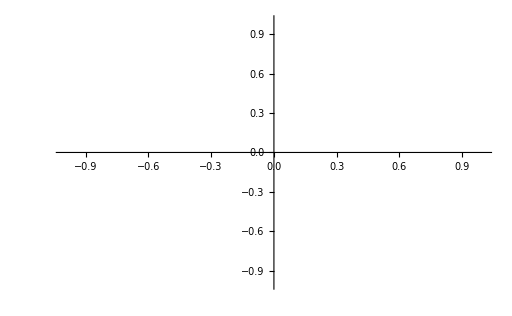

```mathematica
purplePlot=If[myPurpleColorParameters≠{},Show[Table[{myPurpleColorParameters[[myt,All,13;;14]],myPurpleColorParameters[[myt,All,17;;18]]}//ListPlot[#,Joined->True,PlotStyle->{Purple}]&,{myt,1,Length[myPurpleColorParameters],1}],PlotRange->{{0,512},{0,512}},Frame->True,AxesOrigin->{0,0},AspectRatio->{1,1}],
{{0,0}}//ListPlot[#,Joined->True,PlotStyle->{Purple}]&
]
```

```mathematica
purplePlot>>analysisFolder<>"_purplePlot.dat";
```

#### Cyan File

```mathematica
greenTracksW=myGreenAllParameters//Cases[#,x_/;x[[21]]==0&&x[[22]]==1&&x[[23]]==1]&//SplitBy[#,First]&;
blueTracksW=myBlueAllParameters//Cases[#,x_/;x[[21]]==0&&x[[22]]==1&&x[[23]]==1]&//SplitBy[#,First]&;
```

Find Green/Blue links:

```mathematica
myWGBLink=Table[
tempTrack1=greenTracksW⟦i,All,1;;7⟧;
tempTrack2=blueTracksW⟦j,All,1;;7⟧;
FindOverlapDist[tempTrack1,tempTrack2,minOverlapTime],{i,1,Length@greenTracksW,1},{j,1,Length@blueTracksW,1}];
myWGBLinkList=CrossPairFinder[Position[myWGBLink,x_/;0≤x<maxOverlapDistance]]
```

{}

```mathematica
RGBLinks=Table[{"",myWGBLinkList[[i,1,1]],myWGBLinkList[[i,2,1]]},{i,1,Length[myWGBLinkList],1}]
```

{}

```mathematica
Clear[minTR,minTG,minTB,maxTR,maxTG,maxTB,myTRange,startRed,endRed,curRed,curGreen,curBlue];
listHead={"TrackN_Red","TrackN_Green","TrackN_Blue","FrameN","I_Red","I_Green","I_Blue","Dist_RG", "Dist_RB","Dist_GB","Step","MSD","X_Red","Y_Red","X_Green","Y_Green","X_Blue","Y_Blue","(dx_Red^2+dy_Red^2)^1/2","(dx_Green^2+dy_Green^2)^1/2","(dx_Blue^2+dy_Blue^2)^1/2"};
(*i is the White Track Number iterator*)
(*j is the Frame Number iterator, i.e. time*)
(*This is the range of frames that all tracks have*)
myCyanColorParameters=Table[
minTG=Min[greenTracksW⟦RGBLinks⟦i,2⟧,All,2⟧];
minTB=Min[blueTracksW⟦RGBLinks⟦i,3⟧,All,2⟧];
maxTG=Max[greenTracksW⟦RGBLinks⟦i,2⟧,All,2⟧];
maxTB=Max[blueTracksW⟦RGBLinks⟦i,3⟧,All,2⟧];
myTRange={Max[{minTG,minTB}],Min[{maxTG,maxTB}]}; (*This is the range of frames that all tracks have*)
startBlue=Cases[blueTracksW⟦RGBLinks⟦i,3⟧⟧,x_/;x⟦2⟧==myTRange⟦1⟧];(*First frame*)
endBlue=Cases[blueTracksW⟦RGBLinks⟦i,3⟧⟧,x_/;x⟦2⟧==myTRange⟦2⟧]; (*Last frame*)
Table[
curGreen=Cases[greenTracksW⟦RGBLinks⟦i,2⟧⟧,x_/;j≤x⟦2⟧≤j+1]; (*current frame*)
curBlue=Cases[blueTracksW⟦RGBLinks⟦i,3⟧⟧,x_/;j≤x⟦2⟧≤j+1]; (*current frame*)
(*Just in case red/green/blue couldn't be tracked or blinked in this frame*)
If[curGreen≠{}&&curBlue≠{},  
(*OUTPUT COLUMNS FOR FILE*)
{"",
curGreen⟦1,1⟧,
curBlue⟦1,1⟧,curBlue⟦1,2⟧,0,curGreen⟦1,5⟧,curBlue⟦1,5⟧, "","",EuclideanDistance[curGreen⟦1,3;;4⟧,curBlue⟦1,3;;4⟧],If[Length[curBlue]==2, EuclideanDistance[curBlue⟦1,3;;4⟧,curBlue⟦2,3;;4⟧],""],EuclideanDistance[curBlue⟦1,3;;4⟧,startBlue⟦1,3;;4⟧]^2,"","",curGreen⟦1,3⟧,curGreen⟦1,4⟧,curBlue⟦1,3⟧,curBlue⟦1,4⟧,
"",
√((curGreen⟦1,10⟧-curGreen⟦1,9⟧)^2+(curGreen⟦1,12⟧-curGreen⟦1,11⟧)^2)//N,√((curBlue⟦1,10⟧-curBlue⟦1,9⟧)^2+(curBlue⟦1,12⟧-curBlue⟦1,11⟧)^2)//N
}],{j,myTRange⟦1⟧,myTRange⟦2⟧,1}]//DeleteCases[#,Null]&,{i,1,Length[RGBLinks],1}];
```

```mathematica
myCyanColorParameters>>analysisFolder<>"_FixedSigmaCyanColorParameters.dat";
```

```mathematica
Export[analysisFolder<>"_FixedSigmaCyanColorParameters.xlsx",Prepend[myCyanColorParameters//Flatten[#,1]&,listHead]]
```

/Volumes/MINI/_long_timeframe_transient_mini/20171203_14h/Analysis/MAX_TA32_FixedSigmaCyanColorParameters.xlsx

```mathematica
(DeleteCases[myCyanColorParameters,x_/;Length[x]<10])[[1;;All,1;;All,12]]//ListLogPlot[#,Joined->True,PlotRange->All]&
```

ListLogPlot::argx: ListLogPlot called with 0 arguments; 1 argument is expected.

General::stop: Further output of ListLogPlot::argx will be suppressed during this calculation.

ListLogPlot[{},Joined→True,PlotRange→All]

```mathematica
cyanPlot=If[myCyanColorParameters≠{},Show[Table[{myCyanColorParameters[[myt,All,15;;16]],myCyanColorParameters[[myt,All,17;;18]]}//ListPlot[#,Joined->True,PlotStyle->{Cyan}]&,{myt,1,Length[myCyanColorParameters],1}],PlotRange->{{0,512},{0,512}},Frame->True,AxesOrigin->{0,0},AspectRatio->{1,1}],
{{0,0}}//ListPlot[#,Joined->True,PlotStyle->{Cyan}]&
]
```

-Graphics-

```mathematica
cyanPlot>>analysisFolder<>"_cyanPlot.dat";
```

#### Red Only File

```mathematica
redTracksWOff=myRedAllParameters//Cases[#,x_/;x[[21]]==1&&x[[22]]==0&&x[[23]]==0]&//SplitBy[#,First]&;
```

```mathematica
redTracksW=redTracksWOff;
redTracksW⟦All,All,3;;4⟧=myTfFunc/@redTracksW⟦All,All,3;;4⟧;
```

```mathematica
Clear[minTR,minTG,minTB,maxTR,maxTG,maxTB,myTRange,startRed,endRed,curRed,curGreen,curBlue];
listHead={"TrackN_Red","TrackN_Green","TrackN_Blue","FrameN","I_Red","I_Green","I_Blue","Dist_RG", "Dist_RB","Dist_GB","Step","MSD","X_Red","Y_Red","X_Green","Y_Green","X_Blue","Y_Blue","(dx_Red^2+dy_Red^2)^1/2","(dx_Green^2+dy_Green^2)^1/2","(dx_Blue^2+dy_Blue^2)^1/2"};
(*i is the White Track Number iterator*)
(*j is the Frame Number iterator, i.e. time*)
(*This is the range of frames that all tracks have*)
myRedOnlyColorParameters=Table[
minTR=Min[redTracksW⟦i,All,2⟧];
maxTR=Max[redTracksW⟦i,All,2⟧];
myTRange={Max[{minTR}],Min[{maxTR}]}; (*This is the range of frames that all tracks have*)
startRed=Cases[redTracksW⟦i⟧,x_/;x⟦2⟧==myTRange⟦1⟧];(*First frame*)
endRed=Cases[redTracksW⟦i⟧,x_/;x⟦2⟧==myTRange⟦2⟧]; (*Last frame*)
Table[
curRed=Cases[redTracksW⟦i⟧,x_/;j≤x⟦2⟧≤j+1]; (*current frame*)
(*Just in case red/green/blue couldn't be tracked or blinked in this frame*)
If[curRed≠{},  
(*OUTPUT COLUMNS FOR FILE*)
{curRed⟦1,1⟧,
"",
"",curRed⟦1,2⟧, curRed⟦1,5⟧,0,0,"","","",If[Length[curRed]==2, EuclideanDistance[curRed⟦1,3;;4⟧,curRed⟦2,3;;4⟧],""],EuclideanDistance[curRed⟦1,3;;4⟧,startRed⟦1,3;;4⟧]^2,curRed⟦1,3⟧,curRed⟦1,4⟧,"","","","",
√((curRed⟦1,10⟧-curRed⟦1,9⟧)^2+(curRed⟦1,12⟧-curRed⟦1,11⟧)^2)//N,
"",""
}],{j,myTRange⟦1⟧,myTRange⟦2⟧,1}]//DeleteCases[#,Null]&,{i,1,Length[redTracksW],1}];
```

```mathematica
myRedOnlyColorParameters>>analysisFolder<>"_FixedSigmaRedOnlyColorParameters.dat";
```

```mathematica
Export[analysisFolder<>"_FixedRedOnlyColorParameters.xlsx",Prepend[myRedOnlyColorParameters//Flatten[#,1]&,listHead]]
```

/Volumes/MINI/_long_timeframe_transient_mini/20171203_14h/Analysis/MAX_TA32_FixedRedOnlyColorParameters.xlsx

```mathematica
(DeleteCases[myRedOnlyColorParameters,x_/;Length[x]<40])[[1;;All,1;;40,12]]//ListLogPlot[#,Joined->True,PlotRange->All]&
```

ListLogPlot::argx: ListLogPlot called with 0 arguments; 1 argument is expected.

General::stop: Further output of ListLogPlot::argx will be suppressed during this calculation.

ListLogPlot[{},Joined→True,PlotRange→All]

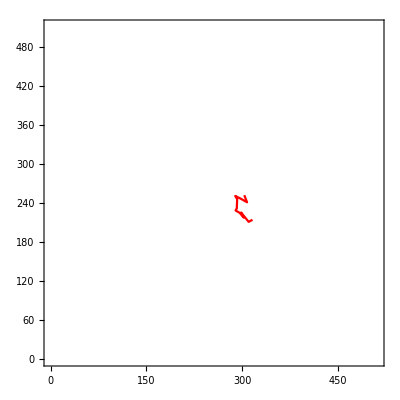

```mathematica
redPlot=If[myRedOnlyColorParameters≠{},Show[Table[{myRedOnlyColorParameters[[myt,All,13;;14]],myRedOnlyColorParameters[[myt,All,15;;16]],myRedOnlyColorParameters[[myt,All,17;;18]]}//ListPlot[#,Joined->True,PlotStyle->{Red}]&,{myt,1,Length[myRedOnlyColorParameters],1}],PlotRange->{{0,512},{0,512}},Frame->True,AxesOrigin->{0,0},AspectRatio->{1,1}],
{{0,0}}//ListPlot[#,Joined->True,PlotStyle->{Red}]&
]
```

```mathematica
redPlot>>analysisFolder<>"_redPlot.dat";
```

#### Green Only File

Using red as a dummy variable here, so a little confusing:

```mathematica
redTracksWOff=myGreenAllParameters//Cases[#,x_/;x[[21]]==0&&x[[22]]==1&&x[[23]]==0]&//SplitBy[#,First]&;
```

```mathematica
redTracksW=redTracksWOff;
redTracksW⟦All,All,3;;4⟧=redTracksW⟦All,All,3;;4⟧;
```

```mathematica
Clear[minTR,minTG,minTB,maxTR,maxTG,maxTB,myTRange,startRed,endRed,curRed,curGreen,curBlue];
listHead={"TrackN_Red","TrackN_Green","TrackN_Blue","FrameN","I_Red","I_Green","I_Blue","Dist_RG", "Dist_RB","Dist_GB","Step","MSD","X_Red","Y_Red","X_Green","Y_Green","X_Blue","Y_Blue","(dx_Red^2+dy_Red^2)^1/2","(dx_Green^2+dy_Green^2)^1/2","(dx_Blue^2+dy_Blue^2)^1/2"};
(*i is the White Track Number iterator*)
(*j is the Frame Number iterator, i.e. time*)
(*This is the range of frames that all tracks have*)
myGreenOnlyColorParameters=Table[
minTR=Min[redTracksW⟦i,All,2⟧];
maxTR=Max[redTracksW⟦i,All,2⟧];
myTRange={Max[{minTR}],Min[{maxTR}]}; (*This is the range of frames that all tracks have*)
startRed=Cases[redTracksW⟦i⟧,x_/;x⟦2⟧==myTRange⟦1⟧];(*First frame*)
endRed=Cases[redTracksW⟦i⟧,x_/;x⟦2⟧==myTRange⟦2⟧]; (*Last frame*)
Table[
curRed=Cases[redTracksW⟦i⟧,x_/;j≤x⟦2⟧≤j+1]; (*current frame*)
(*Just in case red/green/blue couldn't be tracked or blinked in this frame*)
If[curRed≠{},  
(*OUTPUT COLUMNS FOR FILE*)
{"",
curRed⟦1,1⟧,
"",curRed⟦1,2⟧,0,curRed⟦1,5⟧,0,"","","",If[Length[curRed]==2, EuclideanDistance[curRed⟦1,3;;4⟧,curRed⟦2,3;;4⟧],""],EuclideanDistance[curRed⟦1,3;;4⟧,startRed⟦1,3;;4⟧]^2,"","",curRed⟦1,3⟧,curRed⟦1,4⟧,"","",
"",
√((curRed⟦1,10⟧-curRed⟦1,9⟧)^2+(curRed⟦1,12⟧-curRed⟦1,11⟧)^2)//N,""
}],{j,myTRange⟦1⟧,myTRange⟦2⟧,1}]//DeleteCases[#,Null]&,{i,1,Length[redTracksW],1}];
```

```mathematica
myGreenOnlyColorParameters>>analysisFolder<>"_FixedSigmaGreenOnlyColorParameters.dat";
```

```mathematica
Export[analysisFolder<>"_FixedGreenOnlyColorParameters.xlsx",Prepend[myGreenOnlyColorParameters//Flatten[#,1]&,listHead]]
```

/Volumes/MINI/_long_timeframe_transient_mini/20171203_14h/Analysis/MAX_TA32_FixedGreenOnlyColorParameters.xlsx

```mathematica
(DeleteCases[myGreenOnlyColorParameters,x_/;Length[x]<60])[[1;;All,1;;60,12]]//ListLogPlot[#,Joined->True,PlotRange->All]&
```

ListLogPlot::argx: ListLogPlot called with 0 arguments; 1 argument is expected.

General::stop: Further output of ListLogPlot::argx will be suppressed during this calculation.

ListLogPlot[{},Joined→True,PlotRange→All]

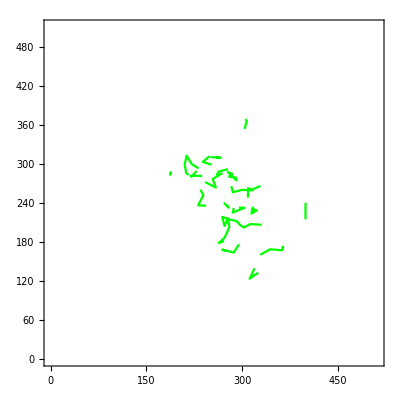

```mathematica
greenPlot=If[myGreenOnlyColorParameters≠{},Show[Table[{myGreenOnlyColorParameters[[myt,All,13;;14]],myGreenOnlyColorParameters[[myt,All,15;;16]],myGreenOnlyColorParameters[[myt,All,17;;18]]}//ListPlot[#,Joined->True,PlotStyle->{Green}]&,{myt,1,Length[myGreenOnlyColorParameters],1}],PlotRange->{{0,512},{0,512}},Frame->True,AxesOrigin->{0,0},AspectRatio->{1,1}],
{{0,0}}//ListPlot[#,Joined->True,PlotStyle->{Green}]&
]
```

```mathematica
greenPlot>>analysisFolder<>"_greenOnlyPlot.dat";
```

#### Blue Only File

Using red as a dummy variable here, so a little confusing:

```mathematica
redTracksWOff=myBlueAllParameters//Cases[#,x_/;x[[21]]==0&&x[[22]]==0&&x[[23]]==1]&//SplitBy[#,First]&;
```

```mathematica
redTracksW=redTracksWOff;
redTracksW⟦All,All,3;;4⟧=redTracksW⟦All,All,3;;4⟧;
```

```mathematica
Clear[minTR,minTG,minTB,maxTR,maxTG,maxTB,myTRange,startRed,endRed,curRed,curGreen,curBlue];
listHead={"TrackN_Red","TrackN_Green","TrackN_Blue","FrameN","I_Red","I_Green","I_Blue","Dist_RG", "Dist_RB","Dist_GB","Step","MSD","X_Red","Y_Red","X_Green","Y_Green","X_Blue","Y_Blue","(dx_Red^2+dy_Red^2)^1/2","(dx_Green^2+dy_Green^2)^1/2","(dx_Blue^2+dy_Blue^2)^1/2"};
(*i is the White Track Number iterator*)
(*j is the Frame Number iterator, i.e. time*)
(*This is the range of frames that all tracks have*)
myBlueOnlyColorParameters=Table[
minTR=Min[redTracksW⟦i,All,2⟧];
maxTR=Max[redTracksW⟦i,All,2⟧];
myTRange={Max[{minTR}],Min[{maxTR}]}; (*This is the range of frames that all tracks have*)
startRed=Cases[redTracksW⟦i⟧,x_/;x⟦2⟧==myTRange⟦1⟧];(*First frame*)
endRed=Cases[redTracksW⟦i⟧,x_/;x⟦2⟧==myTRange⟦2⟧]; (*Last frame*)
Table[
curRed=Cases[redTracksW⟦i⟧,x_/;j≤x⟦2⟧≤j+1]; (*current frame*)
(*Just in case red/green/blue couldn't be tracked or blinked in this frame*)
If[curRed≠{},  
(*OUTPUT COLUMNS FOR FILE*)
{"",
"",
curRed⟦1,1⟧,curRed⟦1,2⟧,0,0,curRed⟦1,5⟧,"","","",If[Length[curRed]==2, EuclideanDistance[curRed⟦1,3;;4⟧,curRed⟦2,3;;4⟧],""],EuclideanDistance[curRed⟦1,3;;4⟧,startRed⟦1,3;;4⟧]^2,"","","","",curRed⟦1,3⟧,curRed⟦1,4⟧,
"",
"",√((curRed⟦1,10⟧-curRed⟦1,9⟧)^2+(curRed⟦1,12⟧-curRed⟦1,11⟧)^2)//N
}],{j,myTRange⟦1⟧,myTRange⟦2⟧,1}]//DeleteCases[#,Null]&,{i,1,Length[redTracksW],1}];
```

```mathematica
myBlueOnlyColorParameters>>analysisFolder<>"_FixedSigmaBlueOnlyColorParameters.dat";
```

```mathematica
Export[analysisFolder<>"_FixedBlueOnlyColorParameters.xlsx",Prepend[myBlueOnlyColorParameters//Flatten[#,1]&,listHead]]
```

/Volumes/MINI/_long_timeframe_transient_mini/20171203_14h/Analysis/MAX_TA32_FixedBlueOnlyColorParameters.xlsx

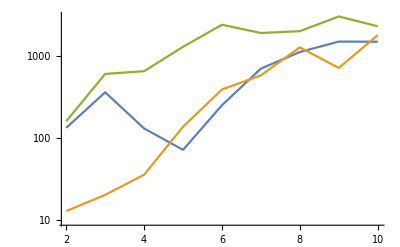

```mathematica
(DeleteCases[myBlueOnlyColorParameters,x_/;Length[x]<10])[[1;;All,1;;10,12]]//ListLogPlot[#,Joined->True,PlotRange->All]&
```

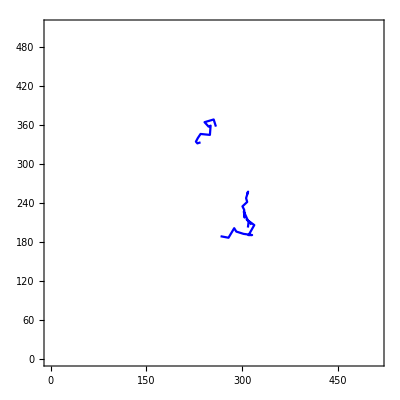

```mathematica
bluePlot=If[myBlueOnlyColorParameters≠{},Show[Table[{myBlueOnlyColorParameters[[myt,All,13;;14]],myBlueOnlyColorParameters[[myt,All,15;;16]],myBlueOnlyColorParameters[[myt,All,17;;18]]}//ListPlot[#,Joined->True,PlotStyle->{Blue}]&,{myt,1,Length[myBlueOnlyColorParameters],1}],PlotRange->{{0,512},{0,512}},Frame->True,AxesOrigin->{0,0},AspectRatio->{1,1}],
{{0,0}}//ListPlot[#,Joined->True,PlotStyle->{Blue}]&
]
```

86

```mathematica
bluePlot>>analysisFolder<>"_blueOnlyPlot.dat";
```

#### Summary

```mathematica
ImageMultiply[cytomask[[1]]-nucmask[[1]]];
```

ImageMultiply::imginv: Expecting an image or graphics instead of ….

```mathematica
myRainbowPlot=Show[{cytomask[[1]]-nucmask[[1]],greenPlot,bluePlot,redPlot,whitePlot,purplePlot,cyanPlot,yellowPlot},ImageSize->300]
```

Show::gcomb: Could not combine the graphics objects in ….

Show[{--Graphics-+-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},ImageSize→300]

```mathematica
Export[analysisFolder<>"_rainbowPlot.tif",myRainbowPlot];
```

```mathematica
myColorParametersList={myWhiteColorParameters,myRedOnlyColorParameters,myGreenOnlyColorParameters,myBlueOnlyColorParameters,myWhiteColorParameters,myYellowColorParameters,myPurpleColorParameters,myCyanColorParameters};
```

```mathematica
myColorsList={"White","Red","Green","Blue","LightGray","Darker[Yellow,0.2]","Purple","Cyan"};
```

```mathematica
myColorsListb={White,Red,Green,Blue,LightGray,Darker[Yellow,0.2],Purple,Cyan};
```

```mathematica
Table[MyMSDPlotter[Cases[myColorParametersList⟦i⟧,x_/;Length[x]>15],myColorsList⟦i⟧],{i,1,Length[myColorsList],1}]
```

{Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
Show[DeleteCases[Table[MyMSDPlotter[Cases[myColorParametersList⟦i⟧,x_/;Length[x]>15],myColorsList⟦i⟧][[1]],{i,1,Length[myColorsList],1}],Null[[1]]],PlotRange->{{0,10},{0, 70}},ImageSize->300]
```

Part::partd: Part specification Null⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Show::shx: No graphical objects to show.

Show[{},PlotRange→{{0,10},{0,70}},ImageSize→300]

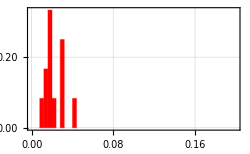
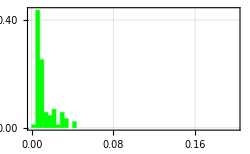
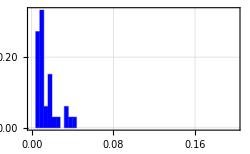
-Graphics- |  | 
 | -Graphics- | 
 |  | -Graphics-
 |  | 
 |  | 
 |  | 
 |  |

```mathematica
{Table[MyHistogramPlotter[myColorParametersList⟦i⟧,listHead,5,myColorsListb⟦i⟧,Table[i,{i,0,0.2,0.004}]],{i,2,Length[myColorsListb],1}],
Table[MyHistogramPlotter[myColorParametersList⟦i⟧,listHead,6,myColorsListb⟦i⟧,Table[i,{i,0,0.2,0.004}]],{i,2,Length[myColorsListb],1}],
Table[MyHistogramPlotter[myColorParametersList⟦i⟧,listHead,7,myColorsListb⟦i⟧,Table[i,{i,0,0.2,0.004}]],{i,2,Length[myColorsListb],1}]
}//Transpose//Grid
```

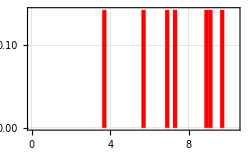
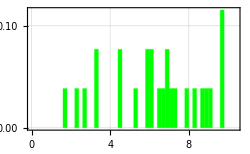
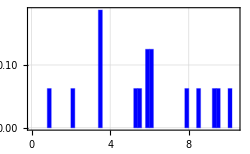
|  |  | -Graphics-
 |  |  | -Graphics-
 |  |  | -Graphics-
 |  |  | 
 |  |  | 
 |  |  | 
 |  |  |

```mathematica
{Table[MyHistogramPlotter[myColorParametersList⟦i⟧,listHead,8,myColorsListb⟦i⟧,Table[i,{i,0,5.5,0.2}]],{i,2,Length[myColorsListb],1}],
Table[MyHistogramPlotter[myColorParametersList⟦i⟧,listHead,9,myColorsListb⟦i⟧,Table[i,{i,0,10.5,0.2}]],{i,2,Length[myColorsListb],1}],
Table[MyHistogramPlotter[myColorParametersList⟦i⟧,listHead,10,myColorsListb⟦i⟧,Table[i,{i,0,5.5,0.2}]],{i,2,Length[myColorsListb],1}],
Table[MyHistogramPlotter[myColorParametersList⟦i⟧,listHead,11,myColorsListb⟦i⟧,Table[i,{i,0,10.5,0.2}]],{i,2,Length[myColorsListb],1}]
}//Transpose//Grid
```

```mathematica
out=Table[Table[Show[Table[MyCrossCorrelatePlotter[myColorParametersList⟦i⟧,listHead,j,k,myColorsList⟦i⟧],{i,1,Length[myColorsList],1}]],{k,j+1,11}],{j,5,9}]//TableForm;
```

### 3-Colored Mask Interaction Analysis (just requires longtracks)

#### Green (tracking green clusters and quantifying intn’s with red and blue)

```mathematica
myColMask=ColorCombine/@Thread@{redComponentMask,greenComponentMask,blueComponentMask};
```

```mathematica
totMask=ImageAdd@@@Thread@{redComponentMask,greenComponentMask,blueComponentMask};
```

```mathematica
myCM=ColorCombine/@Thread@myColMovieRunAv;
```

```mathematica
intMasked=ImageMultiply@@@Thread@{totMask,myCM};
```

```mathematica
Manipulate[intMasked[[i]]//ImageAdjust,{i,1,myMaxN,1}];
```

```mathematica
shortestTrackGreen=100;
```

```mathematica
mylonggreentracks=mygreentracks//DeleteCases[#,x_/;Length[x]<shortestTrackGreen]&;
StringForm["   `` green tracks are longer than ``, and the average length of the long tracks is ``",mylonggreentracks//Length,shortestTrackGreen,(Length/@mylonggreentracks)//Mean//N]
```

10 green tracks are longer than 100, and the average length of the long tracks is 214.4

```mathematica
myGreenSpots=mylonggreentracks//Flatten//Partition[#,4]&//SplitBy[#,First]&;
```

```mathematica
Manipulate[
pos=Cases[myGreenSpots[[myTrackN,1;;All,2;;4]],x_/;x[[1]]==frame];
Show[myColMask⟦frame⟧,Graphics[{Yellow,Circle[If[pos≠{},pos⟦1,2;;3⟧,{-10,-10}],10]}]],{frame,1,myMaxN,1},{myTrackN,1,Length[myGreenSpots],1}];
```

```mathematica
(*For generating a sample movie
myTrackN=1;
myts=myGreenSpots[[myTrackN]][[1;;All,2]];
mysample=Table[{myTrackN,myts⟦i⟧,ComponentMeasurements[myColMask⟦myts⟦i⟧⟧,{"MaskedImage","Mean","Total","Count","Area","Centroid","BoundingBox","Elongation","MaxCentroidDistance"},EuclideanDistance[#Centroid,myGreenSpots[[myTrackN,i,3;;4]]]<#MaxCentroidDistance&,CornerNeighbors->False]},{i,1,Length[myts],1}];*)
```

```mathematica
(*Export[analysisFolder<>"MaskExample2.gif",Table[
pos=Cases[myGreenSpots[[myTrackN,1;;All,2;;4]],x_/;x[[1]]==frame];
ImageTake[Show[myColMask⟦frame⟧,Graphics[{Yellow,Circle[If[pos≠{},pos⟦1,2;;3⟧,{-10,-10}],10]}]],{20,260},{90,430}],{frame,1,myMaxN,1}],"FrameRate"->20,"BitDepth"->8]*)
```

This is faster, but can yield a Null result if Intensity centroid is further than 5 pixels from centroid

```mathematica
myout=Table[
myts=myGreenSpots[[myTrackN]][[1;;All,2]];
Table[{myTrackN,myts⟦i⟧,ComponentMeasurements[myColMask⟦myts⟦i⟧⟧,{"Mean","Total","Count","Area","Centroid","BoundingBox","Elongation","MaxCentroidDistance"},EuclideanDistance[#Centroid,myGreenSpots[[myTrackN,i,3;;4]]]< #MaxCentroidDistance&,CornerNeighbors->False]},{i,1,Length[myts],1}],
{myTrackN,1,Length[myGreenSpots],1}]//Flatten[#,1]&;
```

```mathematica
(*This ensures, if two components are found, only the one closest to the target centroid is chosen*)
myNearestSpots=Table[
myt=Position[myGreenSpots⟦myout⟦i,1⟧⟧,myout⟦i,2⟧]⟦1,1⟧;
Position[myout⟦i⟧,Nearest[myout⟦i,3,1;;All,2,5⟧,myGreenSpots⟦myout⟦i,1⟧,myt,3;;4⟧]⟦1⟧]⟦1,2⟧,{i,1,Length[myout],1}];
```

```mathematica
myout2=Table[{myout⟦i,1⟧,myout⟦i,2⟧,{myout[[i,3,myNearestSpots⟦i⟧]]}},{i,1,Length[myout],1}];
```

```mathematica
greenComponentAnalysis=Prepend[Table[{myout2[[i,1;;2]],If[myout2[[i,3]]=={},Table["",{i,1,Length[listHead]-2,1}],myout2[[i,3,1,2]]]}//Flatten,{i,1,Length[myout2],1}],listHead];
```

```mathematica
greenComponentAnalysis>>analysisFolder<>"_greenComponentAnalysis.dat";
```

```mathematica
Export[analysisFolder<>"_greenComponentAnalysis.xlsx",greenComponentAnalysis];
```

```mathematica
greenComponentAnalysis=<<(analysisFolder<>"_greenComponentAnalysis.dat");
```

```mathematica
gca=greenComponentAnalysis//SplitBy[#,First]&;
```

```mathematica
myoutInt=Table[
myts=myGreenSpots[[myTrackN]][[1;;All,2]];
Table[{myTrackN,myts⟦i⟧,ComponentMeasurements[intMasked⟦myts⟦i⟧⟧,{"Mean","Total","Count","Area","Centroid","BoundingBox","Elongation","MaxCentroidDistance","MeanIntensity","MedianIntensity","TotalIntensity"},EuclideanDistance[#Centroid,myGreenSpots[[myTrackN,i,3;;4]]]< #MaxCentroidDistance&,CornerNeighbors->False]},{i,1,Length[myts],1}],
{myTrackN,1,Length[myGreenSpots],1}]//Flatten[#,1]&//DeleteCases[#,x_/;x[[3]]=={}]&;;
```

```mathematica
(*This ensures, if two components are found, only the one closest to the target centroid is chosen*)
myNearestSpotsInt=Table[
myt=Position[myGreenSpots⟦myoutInt⟦i,1⟧⟧,myoutInt⟦i,2⟧]⟦1,1⟧;
Position[myoutInt⟦i⟧,Nearest[myoutInt⟦i,3,1;;All,2,5⟧,myGreenSpots⟦myoutInt⟦i,1⟧,myt,3;;4⟧]⟦1⟧]⟦1,2⟧,{i,1,Length[myoutInt],1}];
```

```mathematica
myout2Int=Table[{myoutInt⟦i,1⟧,myoutInt⟦i,2⟧,{myoutInt[[i,3,myNearestSpotsInt⟦i⟧]]}},{i,1,Length[myoutInt],1}];
```

```mathematica
listHead={"TrackN_Green","FrameN","I_Red","I_Green","I_Blue","Count_Red","Count_Green","Count_Blue","TotCount","Area","X_Centroid","Y_Centroid","Box_X1","Box_Y1","Box_X2","BoxY2","Elongation","MaxCentroidDistance"};
```

```mathematica
greenComponentAnalysisInt=Prepend[Table[{myout2Int[[i,1;;2]],If[myout2Int[[i,3]]=={},Table["",{i,1,Length[listHead]-2,1}],myout2Int[[i,3,1,2]]]}//Flatten,{i,1,Length[myout2Int],1}],listHead];
```

```mathematica
greenComponentAnalysisInt>>analysisFolder<>"_greenComponentAnalysisInt.dat";
```

```mathematica
Export[analysisFolder<>"_greenComponentAnalysisInt.xlsx",greenComponentAnalysisInt];
```

```mathematica
greenComponentAnalysisInt=<<(analysisFolder<>"_greenComponentAnalysisInt.dat");
```

```mathematica
gcai=greenComponentAnalysisInt//SplitBy[#,First]&;
```

Here you can compare quantification using intensity fluctuations vs. size fluctuations:

```mathematica
Manipulate[{{gcai[[i,All,6]]//MyAutoCorrelate}//ListLogLinearPlot[#,Joined->True,PlotRange->{All,All}]&,

{gca[[i,All,6]]//MyAutoCorrelate}//ListLogLinearPlot[#,Joined->True,PlotRange->{All,All}]&},{{i,2},1,Length[gcai],1}];
```

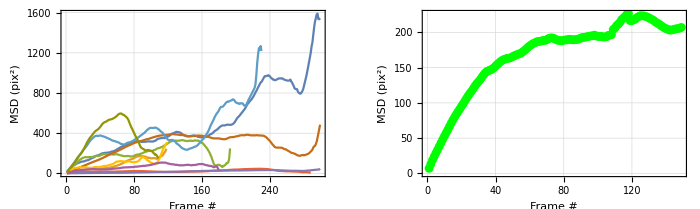

```mathematica
msds=Table[poz=gca[[j,1;;All,11;;12]];
Table[Mean[Total/@((Differences[#,1,i]&@poz)^2)],{i,1,Length[poz]-1}],{j,2,Length[gca],1}];
p1=msds[[1;;All]]//ListPlot[#,Joined->True,PlotTheme->"Detailed",PlotRange->All,FrameLabel->{"Frame #","MSD (pix^2)"},BaseStyle->{FontFamily->"Arial",FontSize->12}]&;
p2=Table[Mean[Cases[msds,x_/;Length[x]>i]⟦1;;All,i⟧],{i,1,Max@(Length/@msds)/2,1}]//ListPlot[#,Joined->True,PlotTheme->"Detailed",PlotRange->All,PlotMarkers->Automatic,FrameLabel->{"Frame #","MSD (pix^2)"},BaseStyle->{FontFamily->"Arial",FontSize->12},PlotStyle->Green]&;
GraphicsRow[{p1,p2},ImageSize->700]
```

```mathematica
Prepend[gca[[2,1;;2]],gca[[2,1]]]//TableForm
```

1 | 1 | 0.2 | 0.548148 | 0.637037 | 27 | 74 | 86 | 135 | 137.5 | 125.833 | 288.989 | 120. | 279. | 132. | 298. | 0.527249 | 9.77156
1 | 1 | 0.2 | 0.548148 | 0.637037 | 27 | 74 | 86 | 135 | 137.5 | 125.833 | 288.989 | 120. | 279. | 132. | 298. | 0.527249 | 9.77156
1 | 2 | 0.298013 | 0.503311 | 0.562914 | 45 | 76 | 85 | 151 | 154.375 | 124.685 | 288.414 | 116. | 279. | 132. | 298. | 0.560438 | 10.2829

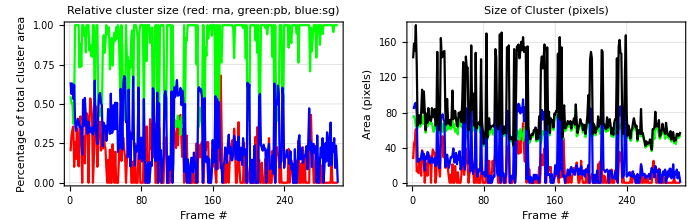

```mathematica
curN=1+1;
{{gca[[curN,All,3]],gca[[curN,All,4]],gca[[curN,All,5]]}//ListPlot[#,Joined->True,PlotStyle->{Red,Green,Blue},PlotTheme->"Detailed",PlotLabel->"Relative cluster size (red: rna, green:pb, blue:sg)",FrameLabel->{"Frame #","Percentage of total cluster area"}]&,
{gca[[curN,All,6]],gca[[curN,All,7]],gca[[curN,All,8]],1.05 gca[[curN,All,9]]}//ListPlot[#,Joined->True,PlotStyle->{Red,Green,Blue,Black},PlotTheme->"Detailed",PlotLabel->"Size of Cluster (pixels)",FrameLabel->{"Frame #","Area (pixels)"}]&
}//GraphicsRow[#,ImageSize->700,Spacings->-15]&
```

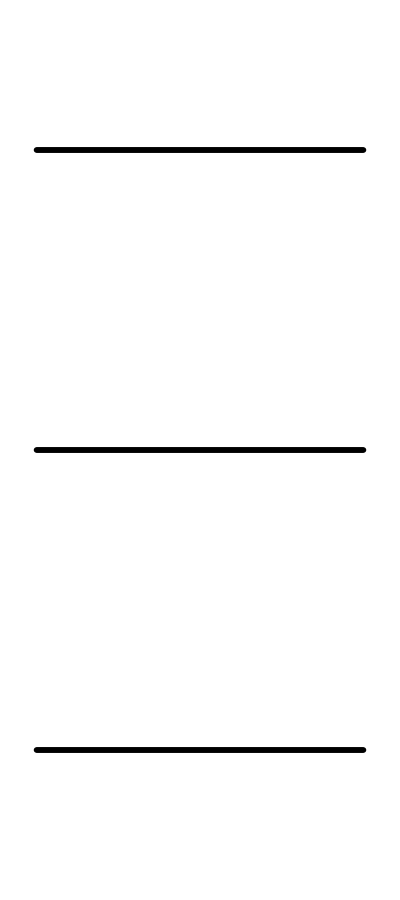

```mathematica
Column[{GraphicsRow[If[#>0,Red,White]&/@MovingAverage[gca[[curN,All,3]],2],ImageSize->700],GraphicsRow[If[#>0,Green,White]&/@MovingAverage[gca[[curN,All,4]],2],ImageSize->700],GraphicsRow[If[#>0,Blue,White]&/@MovingAverage[gca[[curN,All,5]],2],ImageSize->700]}]
```

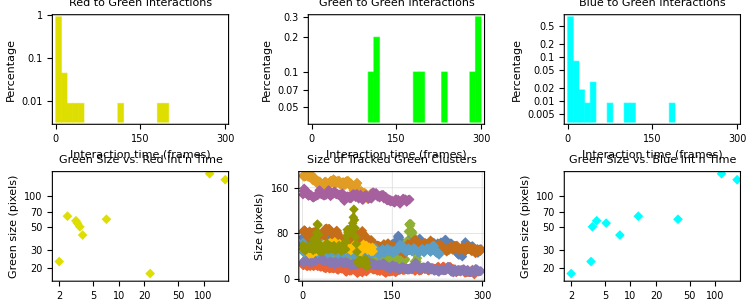

```mathematica
GraphicsGrid[InteractionAnalyzer[gca,4,3,10][[7;;All]]//Partition[#,3]&,ImageSize->750]
```

```mathematica
maxt=100;
txy0=gca[[2;;All,All,{2,11,12}]];
txy=Cases[#,x_/;x[[1]]≤maxt&&NumericQ[x[[2]]]&&NumericQ[x[[3]]]]&/@txy0;
```

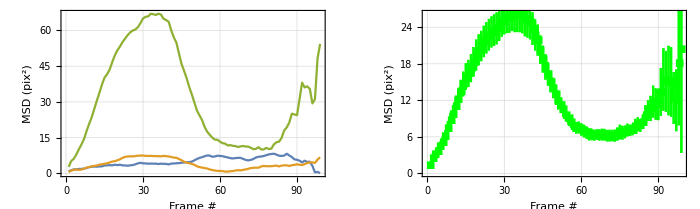

```mathematica
GraphicsRow[TXYDiffusionPlotter[txy[[4;;6]],maxt,Green,2,10],ImageSize->700]
```

#### Blue (tracking blue clusters and quantifying intn’s with red and green)

NOW putting green into here

```mathematica
myColMask=ColorCombine/@Thread@{redComponentMask,greenComponentMask,blueComponentMask};
```

```mathematica
totMask=ImageAdd@@@Thread@{redComponentMask,greenComponentMask,blueComponentMask};
```

```mathematica
holder=Table[0,{i,1,512,1},{j,1,512,1}]//Transpose//Image;
```

```mathematica
ImageTrim[Mean[Table[ColorCombine[{ImageAdjust[myColMovieRunAv[[1,i]],{0,0,1},{0.01,0.06}],holder,ImageAdjust[myColMovieRunAv[[3,i]],{0,0,1},{0.0,0.13}]}],{i,59,59,1}]],{{100,250},{430,460}}]
```

-Graphics-

```mathematica
-Graphics-//ImageDimensions
```

{332,212}

```mathematica
2.29/4.316
```

0.530584

```mathematica
332 .130
```

43.16

```mathematica
myCM=ColorCombine/@Thread@myColMovieRunAv;
```

```mathematica
intMasked=ImageMultiply@@@Thread@{totMask,myCM};
```

```mathematica
Manipulate[ImageTrim[ColorCombine[{redComponentMask[[i]],holder,blueComponentMask[[i]]}],{{100,250},{430,460}}]//ImageAdjust,{i,1,myMaxN,1}]
```

```mathematica
Export[analysisFolder<>"ColoredMask.gif",myColMask,"FrameRate"->20,"BitDepth"->8]
```

C:\Users\tim_s\Documents\_mirroredX\_Fixie\20170928_DCP1A_G3BP1_U2OS_SG\H2B\Plate 3\Analysis\MAX_Cell01ColoredMask.gif

```mathematica
shortestTrackBlue=100;
```

```mathematica
mylongbluetracks=mybluetracks//DeleteCases[#,x_/;Length[x]<shortestTrackBlue]&;
StringForm["   `` blue tracks are longer than ``, and the average length of the long tracks is ``",mylongbluetracks//Length,shortestTrackBlue,(Length/@mylongbluetracks)//Mean//N]
```

46 blue tracks are longer than 100, and the average length of the long tracks is 198.283

```mathematica
myBlueSpots=mylongbluetracks//Flatten//Partition[#,4]&//SplitBy[#,First]&;
```

```mathematica
Length/@mylongbluetracks
```

{113,300,300,300,181,153,222,153,300,258,170,300,153,198,300,212,300,300,250,300,300,300,103,183,285,149,263,113,261,254,110,125,113,205,118,159,157,140,150,148,135,126,125,119,114,103}

```mathematica
Manipulate[
pos=Cases[myBlueSpots[[myTrackN,1;;All,2;;4]],x_/;x[[1]]==frame];
Show[myColMask⟦frame⟧,Graphics[{Yellow,Circle[If[pos≠{},pos⟦1,2;;3⟧,{-10,-10}],5]}]],{frame,1,myMaxN,1},{myTrackN,1,Length[myBlueSpots],1}]
```

```mathematica
myTrackN=7;
myts=myBlueSpots[[myTrackN]][[1;;All,2]];
mysample=Table[{myTrackN,myts⟦i⟧,ComponentMeasurements[myColMask⟦myts⟦i⟧⟧,{"MaskedImage","Mean","Total","Count","Area","Centroid","BoundingBox","Elongation","MaxCentroidDistance"},EuclideanDistance[#Centroid,myBlueSpots[[myTrackN,i,3;;4]]]<#MaxCentroidDistance&,CornerNeighbors->False]},{i,1,Length[myts],1}];
```

```mathematica
yo=DeleteCases[mysample,x_/;x[[3]]=={}][[1;;All,3,1,2,1]];
```

```mathematica
outtie={Table[2 (i-50),{i,50,260,10}],Table[vals=(({13,13}-(yo[[i]]//ImageDimensions)));
temp=If[OddQ[#],{IntegerPart[#/2],Ceiling[#/2]},{#/2,#/2}]&/@vals;
ImagePad[yo[[i]],temp,1],{i,50,260,10}]}//Grid
```

0 | 20 | 40 | 60 | 80 | 100 | 120 | 140 | 160 | 180 | 200 | 220 | 240 | 260 | 280 | 300 | 320 | 340 | 360 | 380 | 400 | 420
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Export[analysisFolder<>"SampleCluster.gif",outtie]
```

C:\Users\tim_s\Documents\_mirroredX\_Fixie\20170430_U2OS_G3BP1-GFP_KDM5B_Stress_Experiment\Analysis\MAX_Cell01_stress_20-30minSampleCluster.gif

```mathematica
Export[analysisFolder<>"blueClusterMaskExample2.gif",Table[
pos=Cases[myBlueSpots[[myTrackN,1;;All,2;;4]],x_/;x[[1]]==frame];
ImageTake[Show[myColMask⟦frame⟧,Graphics[{Yellow,Circle[If[pos≠{},pos⟦1,2;;3⟧,{-10,-10}],10]}]],{20,260},{90,430}],{frame,1,myMaxN,1}],"FrameRate"->20,"BitDepth"->8]
```

C:\Users\tim_s\Documents\_mirroredX\_Fixie\20170928_DCP1A_G3BP1_U2OS_SG\H2B\Plate 3\Analysis\MAX_Cell01blueClusterMaskExample2.gif

This is faster, but can yield a Null result if Intensity centroid is further than 5 pixels from centroid

```mathematica
myout=Table[
myts=myBlueSpots[[myTrackN]][[1;;All,2]];
Table[{myTrackN,myts⟦i⟧,ComponentMeasurements[myColMask⟦myts⟦i⟧⟧,{"Mean","Total","Count","Area","Centroid","BoundingBox","Elongation","MaxCentroidDistance"},EuclideanDistance[#Centroid,myBlueSpots[[myTrackN,i,3;;4]]]<#MaxCentroidDistance&,CornerNeighbors->False]},{i,1,Length[myts],1}],
{myTrackN,1,Length[myBlueSpots],1}]//Flatten[#,1]&;
```

```mathematica
listHead={"TrackN_Blue","FrameN","I_Red","I_Green","I_Blue","Count_Red","Count_Green","Count_Blue","TotCount","Area","X_Centroid","Y_Centroid","Box_X1","Box_Y1","Box_X2","BoxY2","Elongation","MaxCentroidDistance"};
```

```mathematica
(*This ensures, if two components are found, only the one closest to the target centroid is chosen*)
myNearestSpots=Table[
myt=Position[myBlueSpots⟦myout⟦i,1⟧⟧,myout⟦i,2⟧]⟦1,1⟧;
Position[myout⟦i⟧,Nearest[myout⟦i,3,1;;All,2,5⟧,myBlueSpots⟦myout⟦i,1⟧,myt,3;;4⟧]⟦1⟧]⟦1,2⟧,{i,1,Length[myout],1}];
```

Nearest::near1: {} is neither a list of real points nor a valid list of rules.

Part::partw: Part 2 of {3} does not exist.

Nearest::near1: {} is neither a list of real points nor a valid list of rules.

Part::partw: Part 2 of {3} does not exist.

```mathematica
myout2=Table[{myout⟦i,1⟧,myout⟦i,2⟧,{myout[[i,3,myNearestSpots⟦i⟧]]}},{i,1,Length[myout],1}];
```

Part::pkspec1: The expression {{3}}⟦1,2⟧ cannot be used as a part specification.

```mathematica
listHead={"TrackN_Green","FrameN","I_Red","I_Green","I_Blue","Count_Red","Count_Green","Count_Blue","TotCount","Area","X_Centroid","Y_Centroid","Box_X1","Box_Y1","Box_X2","BoxY2","Elongation","MaxCentroidDistance"};
```

```mathematica
blueComponentAnalysis=Prepend[Table[{myout2[[i,1;;2]],If[myout2[[i,3]]=={},Table["",{i,1,Length[listHead]-2,1}],myout2[[i,3,1,2]]]}//Flatten,{i,1,Length[myout2],1}],listHead];
```

```mathematica
blueComponentAnalysis>>analysisFolder<>"_blueComponentAnalysis.dat";
```

```mathematica
Export[analysisFolder<>"_blueComponentAnalysis.xlsx",blueComponentAnalysis];
```

```mathematica
blueComponentAnalysis=<<(analysisFolder<>"_blueComponentAnalysis.dat");
```

```mathematica
bca=blueComponentAnalysis//SplitBy[#,First]&;
```

```mathematica
myoutInt=Table[
myts=myBlueSpots[[myTrackN]][[1;;All,2]];
Table[{myTrackN,myts⟦i⟧,ComponentMeasurements[intMasked⟦myts⟦i⟧⟧,{"Mean","Total","Count","Area","Centroid","BoundingBox","Elongation","MaxCentroidDistance","MeanIntensity","MedianIntensity","TotalIntensity"},EuclideanDistance[#Centroid,myBlueSpots[[myTrackN,i,3;;4]]]< #MaxCentroidDistance&,CornerNeighbors->False]},{i,1,Length[myts],1}],
{myTrackN,1,Length[myBlueSpots],1}]//Flatten[#,1]&//DeleteCases[#,x_/;x[[3]]=={}]&;
```

```mathematica
(*This ensures, if two components are found, only the one closest to the target centroid is chosen*)
myNearestSpotsInt=Table[
myt=Position[myBlueSpots⟦myoutInt⟦i,1⟧⟧,myoutInt⟦i,2⟧]⟦1,1⟧;
Position[myoutInt⟦i⟧,Nearest[myoutInt⟦i,3,1;;All,2,5⟧,myBlueSpots⟦myoutInt⟦i,1⟧,myt,3;;4⟧]⟦1⟧]⟦1,2⟧,{i,1,Length[myoutInt],1}];
```

```mathematica
myout2Int=Table[{myoutInt⟦i,1⟧,myoutInt⟦i,2⟧,{myoutInt[[i,3,myNearestSpotsInt⟦i⟧]]}},{i,1,Length[myoutInt],1}];
```

```mathematica
listHead={"TrackN_Green","FrameN","I_Red","I_Green","I_Blue","Count_Red","Count_Green","Count_Blue","TotCount","Area","X_Centroid","Y_Centroid","Box_X1","Box_Y1","Box_X2","BoxY2","Elongation","MaxCentroidDistance"};
```

```mathematica
blueComponentAnalysisInt=Prepend[Table[{myout2Int[[i,1;;2]],If[myout2Int[[i,3]]=={},Table["",{i,1,Length[listHead]-2,1}],myout2Int[[i,3,1,2]]]}//Flatten,{i,1,Length[myout2Int],1}],listHead];
```

```mathematica
blueComponentAnalysisInt>>analysisFolder<>"_blueComponentAnalysisInt.dat";
```

```mathematica
Export[analysisFolder<>"_blueComponentAnalysisInt.xlsx",blueComponentAnalysisInt];
```

```mathematica
blueComponentAnalysisInt=<<(analysisFolder<>"_blueComponentAnalysisInt.dat");
```

```mathematica
bcai=blueComponentAnalysisInt//SplitBy[#,First]&;
```

Here you can compare quantification using intensity fluctuations vs. size fluctuations:

```mathematica
Manipulate[{{bcai[[i,All,6]]//MyAutoCorrelate}//ListLogLinearPlot[#,Joined->True,PlotRange->{All,All}]&,

{bca[[i,All,6]]//MyAutoCorrelate}//ListLogLinearPlot[#,Joined->True,PlotRange->{All,All}]&},{{i,2},1,Length[bcai],1}];
```

```mathematica
Prepend[bca[[10,1;;5]],bca[[1,1]]]//TableForm
```

TrackN_Green | FrameN | I_Red | I_Green | I_Blue | Count_Red | Count_Green | Count_Blue | TotCount | Area | X_Centroid | Y_Centroid | Box_X1 | Box_Y1 | Box_X2 | BoxY2 | Elongation | MaxCentroidDistance
9 | 1 | 0. | 0. | 1. | 0 | 0 | 53 | 53 | 54.125 | 201.764 | 340.179 | 197. | 336. | 207. | 344. | 0.223112 | 4.85478
9 | 2 | 0.15 | 0. | 0.9 | 9 | 0 | 54 | 60 | 61.625 | 200.967 | 339.667 | 194. | 336. | 207. | 344. | 0.395791 | 6.57106
9 | 3 | 0. | 0. | 1. | 0 | 0 | 49 | 49 | 50.25 | 201.031 | 340.031 | 197. | 336. | 206. | 344. | 0.331877 | 4.72421
9 | 4 | 0. | 0. | 1. | 0 | 0 | 48 | 48 | 49.125 | 200.5 | 339.458 | 195. | 336. | 205. | 343. | 0.319055 | 5.10735
9 | 5 | 0. | 0. | 1. | 0 | 0 | 50 | 50 | 51. | 199.8 | 339.96 | 195. | 336. | 204. | 344. | 0.302449 | 4.99416

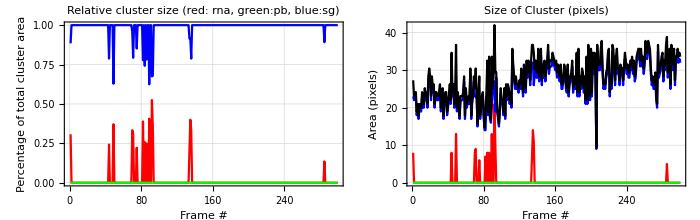

```mathematica
curN=2+1;
{{bca[[curN,All,3]],bca[[curN,All,4]],bca[[curN,All,5]]}//ListPlot[#,Joined->True,PlotStyle->{Red,Green,Blue},PlotTheme->"Detailed",PlotLabel->"Relative cluster size (red: rna, green:pb, blue:sg)",FrameLabel->{"Frame #","Percentage of total cluster area"}]&,
{bca[[curN,All,6]],bca[[curN,All,7]],bca[[curN,All,8]],1.05 bca[[curN,All,9]]}//ListPlot[#,Joined->True,PlotStyle->{Red,Green,Blue,Black},PlotTheme->"Detailed",PlotLabel->"Size of Cluster (pixels)",FrameLabel->{"Frame #","Area (pixels)"}]&
}//GraphicsRow[#,ImageSize->700,Spacings->-15]&
```

```mathematica
Column[{GraphicsRow[If[#>0,Red,White]&/@MovingAverage[bca[[curN,All,3]],2],ImageSize->700],GraphicsRow[If[#>0,Green,White]&/@MovingAverage[bca[[curN,All,4]],2],ImageSize->700],GraphicsRow[If[#>0,Blue,White]&/@MovingAverage[bca[[curN,All,5]],2],ImageSize->700]}]
```

-Graphics-

Part::partw: Part 5 of {23,101,5460} does not exist.

MovingAverage::vecmat: Argument {{{TrackN_Green,FrameN,I_Red,I_Green,I_Blue,Count_Red,Count_Green,Count_Blue,TotCount,Area,X_Centroid,Y_Centroid,Box_X1,Box_Y1,Box_X2,BoxY2,Elongation,MaxCentroidDistance}},«45»,{{46,198,0.76,0.,0.44,19,0,11,25,25.625,255.46,153.22,253.,150.,258.,156.,0.17063,3.00666},{46,199,0.529412,0.,0.617647,18,0,21,34,35.,253.765,153.088,250.,150.,258.,156.,0.226856,3.99318},«48»,«53»}}⟦24,All,5⟧ at position 1 is neither a non-empty vector nor a non-empty matrix.

Part::partw: Part 5 of {25,35,5669} does not exist.

MovingAverage::vecmat: Argument {{{TrackN_Green,FrameN,I_Red,I_Green,I_Blue,Count_Red,Count_Green,Count_Blue,TotCount,Area,X_Centroid,Y_Centroid,Box_X1,Box_Y1,Box_X2,BoxY2,Elongation,MaxCentroidDistance}},«45»,{{46,198,0.76,0.,0.44,19,0,11,25,25.625,255.46,153.22,253.,150.,258.,156.,0.17063,3.00666},{46,199,0.529412,0.,0.617647,18,0,21,34,35.,253.765,153.088,250.,150.,258.,156.,0.226856,3.99318},«48»,«53»}}⟦26,All,5⟧ at position 1 is neither a non-empty vector nor a non-empty matrix.

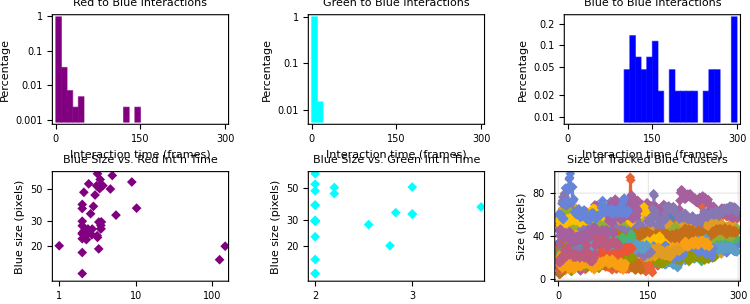

```mathematica
GraphicsGrid[InteractionAnalyzer[bca,5,3,10][[7;;All]]//Partition[#,3]&,ImageSize->750]
```

```mathematica
Dimensions/@bca
```

{{1,18},{113,18},{300,18},{300,18},{300,18},{181,18},{153,18},{222,18},{153,18},{300,18},{258,18},{170,18},{300,18},{153,18},{198,18},{300,18},{212,18},{300,18},{300,18},{250,18},{300,18},{300,18},{300,18},{103},{183,18},{285},{149,18},{263,18},{113,18},{261,18},{254,18},{110,18},{125,18},{113,18},{205,18},{118,18},{159,18},{157,18},{140,18},{150,18},{148,18},{135,18},{126,18},{125,18},{119,18},{114,18},{103,18}}

```mathematica
maxt=100;
txy0=bca[[2;;All,All,{2,11,12}]];
txy=Cases[#,x_/;x[[1]]≤maxt&&NumericQ[x[[2]]]&&NumericQ[x[[3]]]]&/@txy0;
```

Part::partw: Part {2,11,12} of {23,101,5460} does not exist.

Part::partw: Part 2 of {{TrackN_Green,FrameN,I_Red,I_Green,I_Blue,Count_Red,Count_Green,Count_Blue,TotCount,Area,X_Centroid,Y_Centroid,Box_X1,Box_Y1,Box_X2,BoxY2,Elongation,MaxCentroidDistance}} does not exist.

Part::partd: Part specification 2⟦1⟧ is longer than depth of object.

Part::partd: Part specification 2⟦2⟧ is longer than depth of object.

Part::partd: Part specification All⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
GraphicsRow[TXYDiffusionPlotter[txy,100,Blue,3,10],ImageSize->700]
```

-Graphics-

#### Red (tracking red clusters and quantifying intn’s with green and blue)

```mathematica
myredtracksColReg=myredtracks;
myredtracksColReg⟦All,All,2,2;;⟧=myTfFunc/@myredtracksColReg⟦All,All,2,2;;⟧;
```

```mathematica
Clear[myredtracksColRegf]
```

```mathematica
myredtracksColRegf=myredtracksColReg⟦All,All,2⟧//Flatten[#,1]&//Sort//SplitBy[#,First]&;
```

```mathematica
myColMask=Table[ColorCombine[{redComponentMask⟦i⟧,greenComponentMask⟦i⟧,blueComponentMask⟦i⟧}],{i,1,myMaxN,1}];
```

```mathematica
shortestTrackRed=100;
```

```mathematica
mylongredtracks=myredtracksColReg//DeleteCases[#,x_/;Length[x]<shortestTrackRed]&;
StringForm["   `` red tracks are longer than ``, and the average length of the long tracks is ``",mylongredtracks//Length,shortestTrackRed,(Length/@mylongredtracks)//Mean//N]
```

10 red tracks are longer than 100, and the average length of the long tracks is 170.

```mathematica
myRedSpots=mylongredtracks//Flatten//Partition[#,4]&//SplitBy[#,First]&;
```

```mathematica
Length/@mylongredtracks
```

{116,300,300,143,107,207,160,105,152,110}

```mathematica
Manipulate[
pos=Cases[myRedSpots[[myTrackN,1;;All,2;;4]],x_/;x[[1]]==frame];
Show[myColMask⟦frame⟧,Graphics[{Yellow,Circle[If[pos≠{},pos⟦1,2;;3⟧,{-10,-10}],5]}]],{frame,1,myMaxN,1},{myTrackN,1,Length[myRedSpots],1}];
```

```mathematica
myTrackN=1;
myts=myRedSpots[[myTrackN]][[1;;All,2]];
mysample=Table[{myTrackN,myts⟦i⟧,ComponentMeasurements[myColMask⟦myts⟦i⟧⟧,{"MaskedImage","Mean","Total","Count","Area","Centroid","BoundingBox","Elongation","MaxCentroidDistance"},EuclideanDistance[#Centroid,myRedSpots[[myTrackN,i,3;;4]]]<#MaxCentroidDistance&,CornerNeighbors->False]},{i,1,Length[myts],1}];
```

$Aborted

```mathematica
tester=DeleteCases[mysample,x_/;x[[3]]=={}][[1;;All,3,1,2,1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*Export[analysisFolder<>"redMaskExample2.gif",Table[
pos=Cases[myRedSpots[[myTrackN,1;;All,2;;4]],x_/;x[[1]]==frame];
ImageTake[Show[myColMask⟦frame⟧,Graphics[{Yellow,Circle[If[pos≠{},pos⟦1,2;;3⟧,{-10,-10}],10]}]],{20,260},{90,430}],{frame,1,myMaxN,1}],"FrameRate"->20,"BitDepth"->8]*)
```

This is faster, but can yield a Null result if Intensity centroid is further than 5 pixels from centroid

```mathematica
myout=Table[
myts=myRedSpots[[myTrackN]][[1;;All,2]];
Table[{myTrackN,myts⟦i⟧,ComponentMeasurements[myColMask⟦myts⟦i⟧⟧,{"Mean","Total","Count","Area","Centroid","BoundingBox","Elongation","MaxCentroidDistance"},EuclideanDistance[#Centroid,myRedSpots[[myTrackN,i,3;;4]]]< #MaxCentroidDistance&,CornerNeighbors->False]},{i,1,Length[myts],1}],
{myTrackN,1,Length[myRedSpots],1}]//Flatten[#,1]&;
```

$Aborted

```mathematica
listHead={"TrackN_Red","FrameN","I_Red","I_Green","I_Blue","Count_Red","Count_Green","Count_Blue","TotCount","Area","X_Centroid","Y_Centroid","Box_X1","Box_Y1","Box_X2","BoxY2","Elongation","MaxCentroidDistance"};
```

```mathematica
(*This ensures, if two components are found, only the one closest to the target centroid is chosen*)
myNearestSpots=Table[
myt=Position[myRedSpots⟦myout⟦i,1⟧⟧,myout⟦i,2⟧]⟦1,1⟧;
Position[myout⟦i⟧,Nearest[myout⟦i,3,1;;All,2,5⟧,myRedSpots⟦myout⟦i,1⟧,myt,3;;4⟧]⟦1⟧]⟦1,2⟧,{i,1,Length[myout],1}];
```

```mathematica
myout2=Table[{myout⟦i,1⟧,myout⟦i,2⟧,{myout[[i,3,myNearestSpots⟦i⟧]]}},{i,1,Length[myout],1}];
```

```mathematica
listHead={"TrackN_Green","FrameN","I_Red","I_Green","I_Blue","Count_Red","Count_Green","Count_Blue","TotCount","Area","X_Centroid","Y_Centroid","Box_X1","Box_Y1","Box_X2","BoxY2","Elongation","MaxCentroidDistance"};
```

```mathematica
redComponentAnalysis=Prepend[Table[{myout2[[i,1;;2]],If[myout2[[i,3]]=={},Table["",{i,1,Length[listHead]-2,1}],myout2[[i,3,1,2]]]}//Flatten,{i,1,Length[myout2],1}],listHead];
```

```mathematica
redComponentAnalysis>>analysisFolder<>"_redComponentAnalysis.dat";
```

```mathematica
Export[analysisFolder<>"_redComponentAnalysis.xlsx",redComponentAnalysis];
```

```mathematica
redComponentAnalysis=<<(analysisFolder<>"_redComponentAnalysis.dat");
```

```mathematica
rca=redComponentAnalysis//SplitBy[#,First]&;
```

```mathematica
redComponentAnalysis//Dimensions
```

{1420,18}

```mathematica
rca[[4]]//Dimensions
```

{165,18}

```mathematica
Prepend[rca[[2,1;;10]],rca[[2,1]]]//TableForm
```

1 | 1 | 0.179487 | 0. | 0.820513 | 21 | 0 | 96 | 117 | 119.625 | 113.235 | 180.449 | 107. | 172. | 120. | 188. | 0.300112 | 8.4936
1 | 1 | 0.179487 | 0. | 0.820513 | 21 | 0 | 96 | 117 | 119.625 | 113.235 | 180.449 | 107. | 172. | 120. | 188. | 0.300112 | 8.4936
1 | 2 | 0.261682 | 0. | 0.757009 | 28 | 0 | 81 | 107 | 109.625 | 107.509 | 185.687 | 97. | 180. | 118. | 191. | 0.741327 | 10.4866
1 | 3 | 0.21978 | 0. | 0.857143 | 20 | 0 | 78 | 91 | 93.25 | 105.643 | 186.797 | 97. | 180. | 114. | 193. | 0.707156 | 9.40357
1 | 4 | 0.247706 | 0. | 0.844037 | 27 | 0 | 92 | 109 | 111.375 | 105.261 | 187.408 | 97. | 181. | 115. | 195. | 0.672403 | 10.0312
1 | 5 | 0.212121 | 0. | 0.909091 | 21 | 0 | 90 | 99 | 101. | 103.965 | 187.591 | 97. | 181. | 112. | 194. | 0.629932 | 8.75837
1 | 6 | 0.196262 | 0. | 0.878505 | 21 | 0 | 94 | 107 | 109. | 106.192 | 187.276 | 99. | 181. | 115. | 195. | 0.614803 | 10.1187
1 | 7 | 0.293103 | 0. | 0.741379 | 34 | 0 | 86 | 116 | 118.625 | 105.138 | 184.836 | 97. | 175. | 112. | 192. | 0.468471 | 9.63038
1 | 8 | 0.25 | 0. | 0.807692 | 26 | 0 | 84 | 104 | 105.875 | 101.923 | 185.25 | 95. | 176. | 108. | 192. | 0.411304 | 9.12157
1 | 9 | 0.216981 | 0. | 0.849057 | 23 | 0 | 90 | 106 | 108.75 | 101.877 | 184.519 | 93. | 176. | 110. | 193. | 0.696653 | 10.3619
1 | 10 | 0.355932 | 0. | 0.79661 | 21 | 0 | 47 | 59 | 60. | 109.127 | 181.347 | 104. | 177. | 114. | 185. | 0.396934 | 5.21825

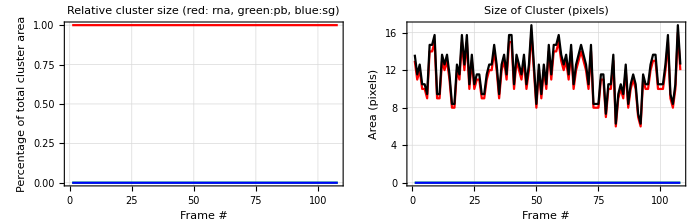

```mathematica
curN=1+1;
{{rca[[curN,All,3]],rca[[curN,All,4]],rca[[curN,All,5]]}//ListPlot[#,Joined->True,PlotStyle->{Red,Green,Blue},PlotTheme->"Detailed",PlotLabel->"Relative cluster size (red: rna, green:pb, blue:sg)",FrameLabel->{"Frame #","Percentage of total cluster area"}]&,
{rca[[curN,All,6]],rca[[curN,All,7]],rca[[curN,All,8]],1.05 rca[[curN,All,9]]}//ListPlot[#,Joined->True,PlotStyle->{Red,Green,Blue,Black},PlotTheme->"Detailed",PlotLabel->"Size of Cluster (pixels)",FrameLabel->{"Frame #","Area (pixels)"}]&
}//GraphicsRow[#,ImageSize->700,Spacings->-15]&
```

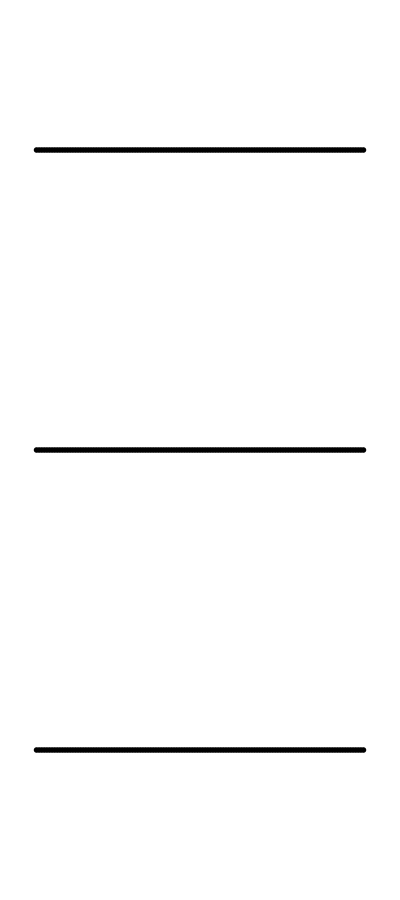

```mathematica
Column[{GraphicsRow[If[#>0,Red,White]&/@MovingAverage[rca[[curN,All,3]],2],ImageSize->700],GraphicsRow[If[#>0,Green,White]&/@MovingAverage[rca[[curN,All,4]],2],ImageSize->700],GraphicsRow[If[#>0,Blue,White]&/@MovingAverage[rca[[curN,All,5]],2],ImageSize->700]}]
```

```mathematica
rca[[goodi[[1]],All,6]]
```

{13,11,12,10,10,9,14,14,15,9,9,13,12,13,11,8,8,12,11,15,12,15,10,13,10,11,11,9,9,11,12,12,14,12,9,12,13,11,15,15,10,13,12,11,13,10,12,16,12,8,12,9,12,10,14,11,14,14,15,13,12,13,11,14,10,12,13,14,13,12,10,14,8,8,8,11,11,7,10,10,13,6,9,10,9,12,8,10,11,10,7,6,11,10,10,12,13,13,10,10,10,12,15,9,8,10,16,12}

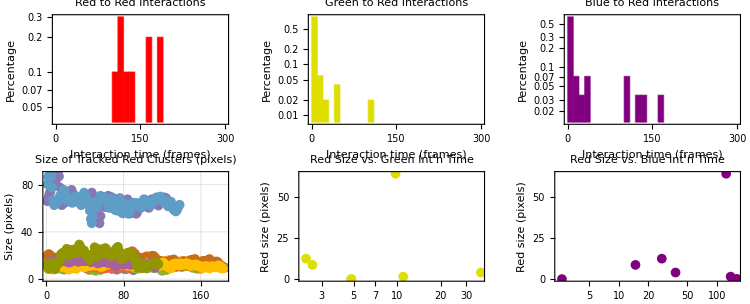

```mathematica
GraphicsGrid[InteractionAnalyzer[rca,3,1,10][[7;;All]]//Partition[#,3]&,ImageSize->750]
```

```mathematica
maxt=100;
txy0=rca[[2;;All,All,{2,11,12}]];
txy=Cases[#,x_/;x[[1]]≤maxt&&NumericQ[x[[2]]]&&NumericQ[x[[3]]]]&/@txy0;
```

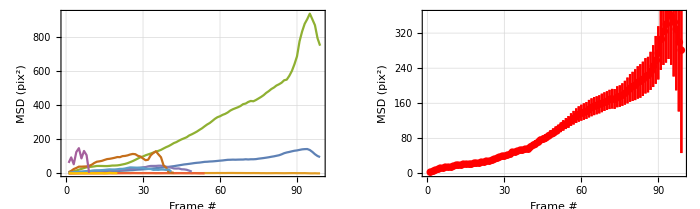

```mathematica
GraphicsRow[TXYDiffusionPlotter[txy,100,Red,1,10],ImageSize->700]
```

This yields exactly one component per coordinate, but is a bit slower

```mathematica
(*myTrackN=41;
myts=myGreenSpots[[myTrackN]][[1;;All,2]];
test=Table[{myts⟦i⟧,ComponentMeasurements[myColMask⟦myts⟦i⟧⟧,{"Mean","Total","Count","Area","Centroid","BoundingBox","Elongation"},RegionMember[ConvexHullMesh[#ConvexVertices],myGreenSpots⟦myTrackN,i,3;;4⟧]&,CornerNeighbors->False]},{i,1,Length[myts],50}]//TableForm*)
```

### Comparing Gaussian and Centroid Fitting

#### Comparing Gaussian fitting and Centroid fitting for Blue

```mathematica
gs=myBlueAllParameters;
```

```mathematica
cents=myHandCheckedTracksb//Flatten[#,1]&;
```

```mathematica
gspos=gs[[All,3;;4]];
```

```mathematica
centspos=cents[[All,2,2;;3]];
```

```mathematica
{gspos//Dimensions,centspos//Dimensions}
```

{{14565,2},{14565,2}}

This shows there is a very tight correlation between the centroids and the Gaussian fitting, although some small errors:

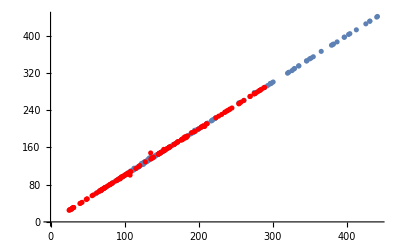

```mathematica
Show[{gspos[[1;;All;;100,1]],centspos[[1;;All;;100,1]]}//Transpose//ListPlot,{gspos[[1;;All;;100,2]],centspos[[1;;All;;100,2]]}//Transpose//ListPlot[#,PlotStyle->Red]&]
```

```mathematica
gts=gs//SplitBy[#,First]&;
```

```mathematica
cts=cents//SplitBy[#,First]&;
```

```mathematica
gts[[1,1;;2,3;;4]]
```

{{69.1346,151.185},{69.199,149.043}}

```mathematica
cts[[1,1;;2,2,2;;3]]
```

{{68.9149,151.23},{69.074,149.133}}

```mathematica
listHead={"TrackN_Red","TrackN_Green","TrackN_Blue","FrameN","I_Red","I_Green","I_Blue","Dist_RG", "Dist_RB","Dist_GB","Step","MSD","X_Red","Y_Red","X_Green","Y_Green","X_Blue","Y_Blue","(dx_Red^2+dy_Red^2)^1/2","(dx_Green^2+dy_Green^2)^1/2","(dx_Blue^2+dy_Blue^2)^1/2"};
```

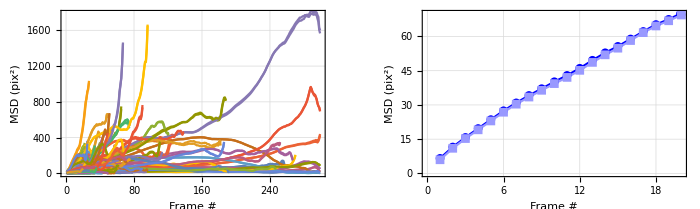

```mathematica
btns=myBlueOnlyColorParameters[[All,1,3]];
maxl=20;
btlong=DeleteCases[Table[If[Length[gts⟦btns⟦i⟧⟧]>maxl,btns⟦i⟧,0],{i,1,Length[btns],1}],0];
msds=Table[poz=gts[[btlong[[j]],1;;All,3;;4]];
Table[Mean[Total/@((Differences[#,1,i]&@poz)^2)],{i,1,Length[poz]-1}],{j,1,Length[btlong],1}];
msdsc=Table[poz=cts[[btlong[[j]],1;;All,2,2;;3]];
Table[Mean[Total/@((Differences[#,1,i]&@poz)^2)],{i,1,Length[poz]-1}],{j,1,Length[btlong],1}];
p1=msds[[1;;All]]//ListPlot[#,Joined->True,PlotTheme->"Detailed",PlotRange->All,FrameLabel->{"Frame #","MSD (pix^2)"},BaseStyle->{FontFamily->"Arial",FontSize->12}]&;
p1b=msdsc[[1;;All]]//ListPlot[#,Joined->True,PlotTheme->"Detailed",PlotRange->All,FrameLabel->{"Frame #","MSD (pix^2)"},BaseStyle->{FontFamily->"Arial",FontSize->12}]&;
p2={Table[Mean[Cases[msds,x_/;Length[x]>i]⟦1;;All,i⟧],{i,1,Max@(Length/@msds)/2,1}],Table[Mean[Cases[msdsc,x_/;Length[x]>i]⟦1;;All,i⟧],{i,1,Max@(Length/@msdsc)/2,1}]}//ListPlot[#,Joined->True,PlotTheme->"Detailed",PlotRange->{{0,maxl},{0,70}},PlotMarkers->Automatic,FrameLabel->{"Frame #","MSD (pix^2)"},BaseStyle->{FontFamily->"Arial",FontSize->12},PlotStyle->{Blue,Lighter[Blue,0.6]}]&;
pA=GraphicsRow[{Show[p1,p1b],p2},ImageSize->700]
```

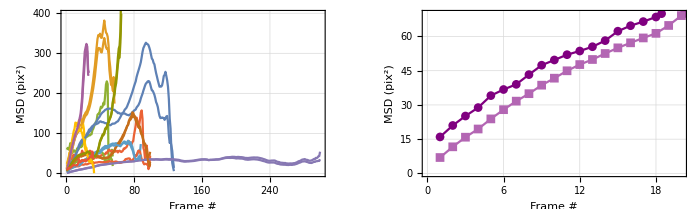

```mathematica
btns=myPurpleColorParameters[[All,1,3]];
maxl=20;
btlong=DeleteCases[Table[If[Length[gts⟦btns⟦i⟧⟧]>maxl,btns⟦i⟧,0],{i,1,Length[btns],1}],0];
msds=Table[poz=gts[[btlong[[j]],1;;All,3;;4]];
Table[Mean[Total/@((Differences[#,1,i]&@poz)^2)],{i,1,Length[poz]-1}],{j,1,Length[btlong],1}];
msdsc=Table[poz=cts[[btlong[[j]],1;;All,2,2;;3]];
Table[Mean[Total/@((Differences[#,1,i]&@poz)^2)],{i,1,Length[poz]-1}],{j,1,Length[btlong],1}];
p1=msds[[1;;All]]//ListPlot[#,Joined->True,PlotTheme->"Detailed",PlotRange->All,FrameLabel->{"Frame #","MSD (pix^2)"},BaseStyle->{FontFamily->"Arial",FontSize->12}]&;
p1b=msdsc[[1;;All]]//ListPlot[#,Joined->True,PlotTheme->"Detailed",PlotRange->All,FrameLabel->{"Frame #","MSD (pix^2)"},BaseStyle->{FontFamily->"Arial",FontSize->12}]&;
p2={Table[Mean[Cases[msds,x_/;Length[x]>i]⟦1;;All,i⟧],{i,1,Max@(Length/@msds)/2,1}],Table[Mean[Cases[msdsc,x_/;Length[x]>i]⟦1;;All,i⟧],{i,1,Max@(Length/@msdsc)/2,1}]}//ListPlot[#,Joined->True,PlotTheme->"Detailed",PlotRange->{{0,maxl},{0,70}},PlotMarkers->Automatic,FrameLabel->{"Frame #","MSD (pix^2)"},BaseStyle->{FontFamily->"Arial",FontSize->12},PlotStyle->{Purple,Lighter[Purple,0.4]}]&;
pB=GraphicsRow[{Show[p1,p1b],p2},ImageSize->700]
```

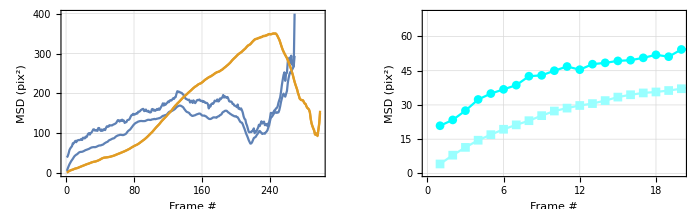

```mathematica
btns=myCyanColorParameters[[All,1,3]];
maxl=20;
btlong=DeleteCases[Table[If[Length[gts⟦btns⟦i⟧⟧]>maxl,btns⟦i⟧,0],{i,1,Length[btns],1}],0];
msds=Table[poz=gts[[btlong[[j]],1;;All,3;;4]];
Table[Mean[Total/@((Differences[#,1,i]&@poz)^2)],{i,1,Length[poz]-1}],{j,1,Length[btlong],1}];
msdsc=Table[poz=cts[[btlong[[j]],1;;All,2,2;;3]];
Table[Mean[Total/@((Differences[#,1,i]&@poz)^2)],{i,1,Length[poz]-1}],{j,1,Length[btlong],1}];
p1=msds[[1;;All]]//ListPlot[#,Joined->True,PlotTheme->"Detailed",PlotRange->All,FrameLabel->{"Frame #","MSD (pix^2)"},BaseStyle->{FontFamily->"Arial",FontSize->12}]&;
p1b=msdsc[[1;;All]]//ListPlot[#,Joined->True,PlotTheme->"Detailed",PlotRange->All,FrameLabel->{"Frame #","MSD (pix^2)"},BaseStyle->{FontFamily->"Arial",FontSize->12}]&;
p2={Table[Mean[Cases[msds,x_/;Length[x]>i]⟦1;;All,i⟧],{i,1,Max@(Length/@msds)/2,1}],Table[Mean[Cases[msdsc,x_/;Length[x]>i]⟦1;;All,i⟧],{i,1,Max@(Length/@msdsc)/2,1}]}//ListPlot[#,Joined->True,PlotTheme->"Detailed",PlotRange->{{0,maxl},{0,70}},PlotMarkers->Automatic,FrameLabel->{"Frame #","MSD (pix^2)"},BaseStyle->{FontFamily->"Arial",FontSize->12},PlotStyle->{Cyan,Lighter[Cyan,0.6]}]&;
pC=GraphicsRow[{Show[p1,p1b],p2},ImageSize->700]
```

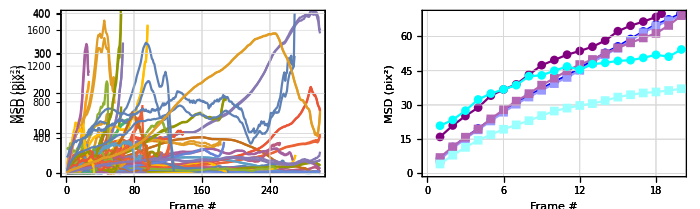

```mathematica
Show[pA,pB,pC]
```

#### Comparing Gaussian fitting and Centroid fitting for Green

```mathematica
gs=myGreenAllParameters;
```

```mathematica
cents=myHandCheckedTracksg//Flatten[#,1]&;
```

```mathematica
gspos=gs[[All,3;;4]];
```

```mathematica
centspos=cents[[All,2,2;;3]];
```

```mathematica
{gspos//Dimensions,centspos//Dimensions}
```

{{6714,2},{6714,2}}

This shows there is a very tight correlation between the centroids and the Gaussian fitting, although some small errors:

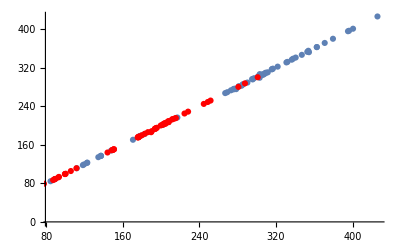

```mathematica
Show[{gspos[[1;;All;;100,1]],centspos[[1;;All;;100,1]]}//Transpose//ListPlot,{gspos[[1;;All;;100,2]],centspos[[1;;All;;100,2]]}//Transpose//ListPlot[#,PlotStyle->Red]&]
```

```mathematica
gts=gs//SplitBy[#,First]&;
```

```mathematica
cts=cents//SplitBy[#,First]&;
```

```mathematica
gts[[1,1;;2,3;;4]]
```

{{88.5334,143.848},{88.9882,144.31}}

```mathematica
cts[[1,1;;2,2,2;;3]]
```

{{88.3921,143.931},{88.9354,144.393}}

```mathematica
listHead={"TrackN_Red","TrackN_Green","TrackN_Blue","FrameN","I_Red","I_Green","I_Blue","Dist_RG", "Dist_RB","Dist_GB","Step","MSD","X_Red","Y_Red","X_Green","Y_Green","X_Blue","Y_Blue","(dx_Red^2+dy_Red^2)^1/2","(dx_Green^2+dy_Green^2)^1/2","(dx_Blue^2+dy_Blue^2)^1/2"};
```

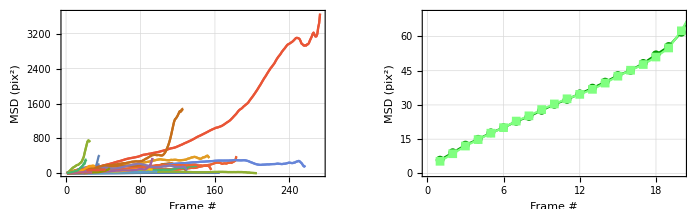

```mathematica
btns=myGreenOnlyColorParameters[[All,1,2]];
maxl=20;
btlong=DeleteCases[Table[If[Length[gts⟦btns⟦i⟧⟧]>maxl,btns⟦i⟧,0],{i,1,Length[btns],1}],0];
msds=Table[poz=gts[[btlong[[j]],1;;All,3;;4]];
Table[Mean[Total/@((Differences[#,1,i]&@poz)^2)],{i,1,Length[poz]-1}],{j,1,Length[btlong],1}];
msdsc=Table[poz=cts[[btlong[[j]],1;;All,2,2;;3]];
Table[Mean[Total/@((Differences[#,1,i]&@poz)^2)],{i,1,Length[poz]-1}],{j,1,Length[btlong],1}];
p1=msds[[1;;All]]//ListPlot[#,Joined->True,PlotTheme->"Detailed",PlotRange->All,FrameLabel->{"Frame #","MSD (pix^2)"},BaseStyle->{FontFamily->"Arial",FontSize->12}]&;
p1b=msdsc[[1;;All]]//ListPlot[#,Joined->True,PlotTheme->"Detailed",PlotRange->All,FrameLabel->{"Frame #","MSD (pix^2)"},BaseStyle->{FontFamily->"Arial",FontSize->12}]&;
p2={Table[Mean[Cases[msds,x_/;Length[x]>i]⟦1;;All,i⟧],{i,1,Max@(Length/@msds)/2,1}],Table[Mean[Cases[msdsc,x_/;Length[x]>i]⟦1;;All,i⟧],{i,1,Max@(Length/@msdsc)/2,1}]}//ListPlot[#,Joined->True,PlotTheme->"Detailed",PlotRange->{{0,maxl},{0,70}},PlotMarkers->Automatic,FrameLabel->{"Frame #","MSD (pix^2)"},BaseStyle->{FontFamily->"Arial",FontSize->12},PlotStyle->{Darker[Green,0.4],Lighter[Green,0.5]}]&;
pD=GraphicsRow[{Show[p1,p1b],p2},ImageSize->700]
```

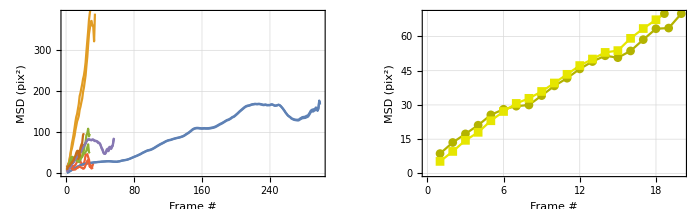

```mathematica
btns=myYellowColorParameters[[All,1,2]];
maxl=20;
btlong=DeleteCases[Table[If[Length[gts⟦btns⟦i⟧⟧]>maxl,btns⟦i⟧,0],{i,1,Length[btns],1}],0];
msds=Table[poz=gts[[btlong[[j]],1;;All,3;;4]];
Table[Mean[Total/@((Differences[#,1,i]&@poz)^2)],{i,1,Length[poz]-1}],{j,1,Length[btlong],1}];
msdsc=Table[poz=cts[[btlong[[j]],1;;All,2,2;;3]];
Table[Mean[Total/@((Differences[#,1,i]&@poz)^2)],{i,1,Length[poz]-1}],{j,1,Length[btlong],1}];
p1=msds[[1;;All]]//ListPlot[#,Joined->True,PlotTheme->"Detailed",PlotRange->All,FrameLabel->{"Frame #","MSD (pix^2)"},BaseStyle->{FontFamily->"Arial",FontSize->12}]&;
p1b=msdsc[[1;;All]]//ListPlot[#,Joined->True,PlotTheme->"Detailed",PlotRange->All,FrameLabel->{"Frame #","MSD (pix^2)"},BaseStyle->{FontFamily->"Arial",FontSize->12}]&;
p2={Table[Mean[Cases[msds,x_/;Length[x]>i]⟦1;;All,i⟧],{i,1,Max@(Length/@msds)/2,1}],Table[Mean[Cases[msdsc,x_/;Length[x]>i]⟦1;;All,i⟧],{i,1,Max@(Length/@msdsc)/2,1}]}//ListPlot[#,Joined->True,PlotTheme->"Detailed",PlotRange->{{0,maxl},{0,70}},PlotMarkers->Automatic,FrameLabel->{"Frame #","MSD (pix^2)"},BaseStyle->{FontFamily->"Arial",FontSize->12},PlotStyle->{Darker[Yellow,0.3],Darker[Yellow,0.1]}]&;
pE=GraphicsRow[{Show[p1,p1b],p2},ImageSize->700]
```

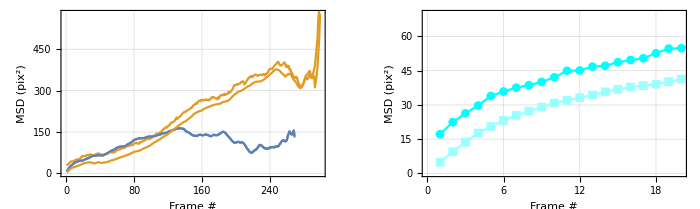

```mathematica
btns=myCyanColorParameters[[All,1,2]];
maxl=20;
btlong=DeleteCases[Table[If[Length[gts⟦btns⟦i⟧⟧]>maxl,btns⟦i⟧,0],{i,1,Length[btns],1}],0];
msds=Table[poz=gts[[btlong[[j]],1;;All,3;;4]];
Table[Mean[Total/@((Differences[#,1,i]&@poz)^2)],{i,1,Length[poz]-1}],{j,1,Length[btlong],1}];
msdsc=Table[poz=cts[[btlong[[j]],1;;All,2,2;;3]];
Table[Mean[Total/@((Differences[#,1,i]&@poz)^2)],{i,1,Length[poz]-1}],{j,1,Length[btlong],1}];
p1=msds[[1;;All]]//ListPlot[#,Joined->True,PlotTheme->"Detailed",PlotRange->All,FrameLabel->{"Frame #","MSD (pix^2)"},BaseStyle->{FontFamily->"Arial",FontSize->12}]&;
p1b=msdsc[[1;;All]]//ListPlot[#,Joined->True,PlotTheme->"Detailed",PlotRange->All,FrameLabel->{"Frame #","MSD (pix^2)"},BaseStyle->{FontFamily->"Arial",FontSize->12}]&;
p2={Table[Mean[Cases[msds,x_/;Length[x]>i]⟦1;;All,i⟧],{i,1,Max@(Length/@msds)/2,1}],Table[Mean[Cases[msdsc,x_/;Length[x]>i]⟦1;;All,i⟧],{i,1,Max@(Length/@msdsc)/2,1}]}//ListPlot[#,Joined->True,PlotTheme->"Detailed",PlotRange->{{0,maxl},{0,70}},PlotMarkers->Automatic,FrameLabel->{"Frame #","MSD (pix^2)"},BaseStyle->{FontFamily->"Arial",FontSize->12},PlotStyle->{Cyan,Lighter[Cyan,0.6]}]&;
pF=GraphicsRow[{Show[p1,p1b],p2},ImageSize->700]
```

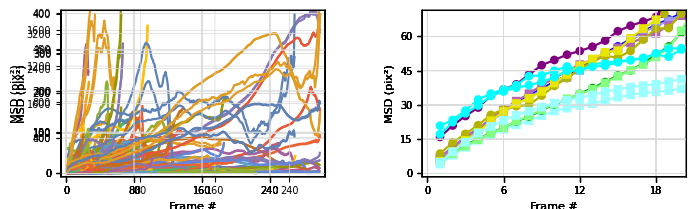

```mathematica
Show[pA,pB,pC,pD,pE,pF]
```

#### Comparing Gaussian fitting and Centroid fitting for Red

```mathematica
gs=myRedAllParameters;
```

```mathematica
cents=myHandCheckedTracksr//Flatten[#,1]&;
```

```mathematica
gspos=gs[[All,3;;4]];
```

```mathematica
centspos=cents[[All,2,2;;3]];
```

```mathematica
{gspos//Dimensions,centspos//Dimensions}
```

{{10796,2},{10796,2}}

This shows there is a very tight correlation between the centroids and the Gaussian fitting, although some small errors:

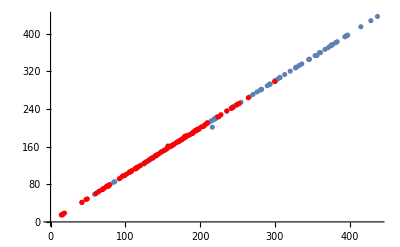

```mathematica
Show[{gspos[[1;;All;;100,1]],centspos[[1;;All;;100,1]]}//Transpose//ListPlot,{gspos[[1;;All;;100,2]],centspos[[1;;All;;100,2]]}//Transpose//ListPlot[#,PlotStyle->Red]&]
```

```mathematica
gts=gs//SplitBy[#,First]&;
```

```mathematica
cts=cents//SplitBy[#,First]&;
```

```mathematica
gts[[1,1;;2,3;;4]]
```

{{58.8933,142.71},{62.3925,152.003}}

```mathematica
cts[[1,1;;2,2,2;;3]]
```

{{58.6775,143.109},{62.4205,151.801}}

```mathematica
listHead={"TrackN_Red","TrackN_Green","TrackN_Blue","FrameN","I_Red","I_Green","I_Blue","Dist_RG", "Dist_RB","Dist_GB","Step","MSD","X_Red","Y_Red","X_Green","Y_Green","X_Blue","Y_Blue","(dx_Red^2+dy_Red^2)^1/2","(dx_Green^2+dy_Green^2)^1/2","(dx_Blue^2+dy_Blue^2)^1/2"};
```

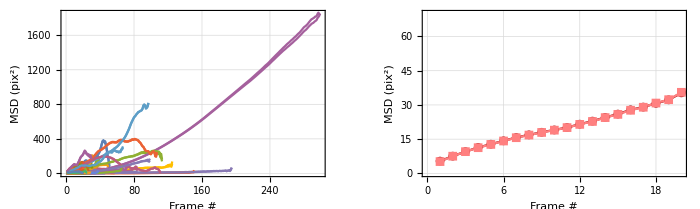

```mathematica
btns=myRedOnlyColorParameters[[All,1,1]];
maxl=20;
btlong=DeleteCases[Table[If[Length[gts⟦btns⟦i⟧⟧]>maxl,btns⟦i⟧,0],{i,1,Length[btns],1}],0];
msds=Table[poz=gts[[btlong[[j]],1;;All,3;;4]];
Table[Mean[Total/@((Differences[#,1,i]&@poz)^2)],{i,1,Length[poz]-1}],{j,1,Length[btlong],1}];
msdsc=Table[poz=cts[[btlong[[j]],1;;All,2,2;;3]];
Table[Mean[Total/@((Differences[#,1,i]&@poz)^2)],{i,1,Length[poz]-1}],{j,1,Length[btlong],1}];
p1=msds[[1;;All]]//ListPlot[#,Joined->True,PlotTheme->"Detailed",PlotRange->All,FrameLabel->{"Frame #","MSD (pix^2)"},BaseStyle->{FontFamily->"Arial",FontSize->12}]&;
p1b=msdsc[[1;;All]]//ListPlot[#,Joined->True,PlotTheme->"Detailed",PlotRange->All,FrameLabel->{"Frame #","MSD (pix^2)"},BaseStyle->{FontFamily->"Arial",FontSize->12}]&;
p2={Table[Mean[Cases[msds,x_/;Length[x]>i]⟦1;;All,i⟧],{i,1,Max@(Length/@msds)/2,1}],Table[Mean[Cases[msdsc,x_/;Length[x]>i]⟦1;;All,i⟧],{i,1,Max@(Length/@msdsc)/2,1}]}//ListPlot[#,Joined->True,PlotTheme->"Detailed",PlotRange->{{0,maxl},{0,70}},PlotMarkers->Automatic,FrameLabel->{"Frame #","MSD (pix^2)"},BaseStyle->{FontFamily->"Arial",FontSize->12},PlotStyle->{Darker[Red,0.4],Lighter[Red,0.5]}]&;
pG=GraphicsRow[{Show[p1,p1b],p2},ImageSize->700]
```

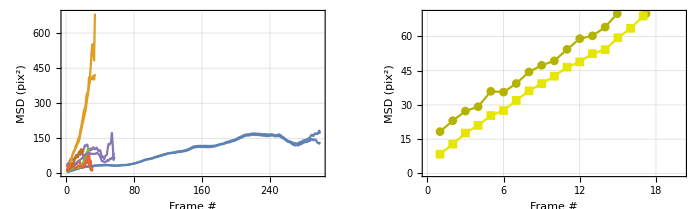

```mathematica
btns=myYellowColorParameters[[All,1,1]];
maxl=20;
btlong=DeleteCases[Table[If[Length[gts⟦btns⟦i⟧⟧]>maxl,btns⟦i⟧,0],{i,1,Length[btns],1}],0];
msds=Table[poz=gts[[btlong[[j]],1;;All,3;;4]];
Table[Mean[Total/@((Differences[#,1,i]&@poz)^2)],{i,1,Length[poz]-1}],{j,1,Length[btlong],1}];
msdsc=Table[poz=cts[[btlong[[j]],1;;All,2,2;;3]];
Table[Mean[Total/@((Differences[#,1,i]&@poz)^2)],{i,1,Length[poz]-1}],{j,1,Length[btlong],1}];
p1=msds[[1;;All]]//ListPlot[#,Joined->True,PlotTheme->"Detailed",PlotRange->All,FrameLabel->{"Frame #","MSD (pix^2)"},BaseStyle->{FontFamily->"Arial",FontSize->12}]&;
p1b=msdsc[[1;;All]]//ListPlot[#,Joined->True,PlotTheme->"Detailed",PlotRange->All,FrameLabel->{"Frame #","MSD (pix^2)"},BaseStyle->{FontFamily->"Arial",FontSize->12}]&;
p2={Table[Mean[Cases[msds,x_/;Length[x]>i]⟦1;;All,i⟧],{i,1,Max@(Length/@msds)/2,1}],Table[Mean[Cases[msdsc,x_/;Length[x]>i]⟦1;;All,i⟧],{i,1,Max@(Length/@msdsc)/2,1}]}//ListPlot[#,Joined->True,PlotTheme->"Detailed",PlotRange->{{0,maxl},{0,70}},PlotMarkers->Automatic,FrameLabel->{"Frame #","MSD (pix^2)"},BaseStyle->{FontFamily->"Arial",FontSize->12},PlotStyle->{Darker[Yellow,0.3],Darker[Yellow,0.1]}]&;
pH=GraphicsRow[{Show[p1,p1b],p2},ImageSize->700]
```

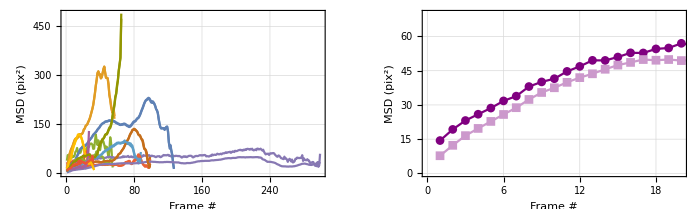

```mathematica
btns=myPurpleColorParameters[[All,1,1]];
maxl=20;
btlong=DeleteCases[Table[If[Length[gts⟦btns⟦i⟧⟧]>maxl,btns⟦i⟧,0],{i,1,Length[btns],1}],0];
msds=Table[poz=gts[[btlong[[j]],1;;All,3;;4]];
Table[Mean[Total/@((Differences[#,1,i]&@poz)^2)],{i,1,Length[poz]-1}],{j,1,Length[btlong],1}];
msdsc=Table[poz=cts[[btlong[[j]],1;;All,2,2;;3]];
Table[Mean[Total/@((Differences[#,1,i]&@poz)^2)],{i,1,Length[poz]-1}],{j,1,Length[btlong],1}];
p1=msds[[1;;All]]//ListPlot[#,Joined->True,PlotTheme->"Detailed",PlotRange->All,FrameLabel->{"Frame #","MSD (pix^2)"},BaseStyle->{FontFamily->"Arial",FontSize->12}]&;
p1b=msdsc[[1;;All]]//ListPlot[#,Joined->True,PlotTheme->"Detailed",PlotRange->All,FrameLabel->{"Frame #","MSD (pix^2)"},BaseStyle->{FontFamily->"Arial",FontSize->12}]&;
p2={Table[Mean[Cases[msds,x_/;Length[x]>i]⟦1;;All,i⟧],{i,1,Max@(Length/@msds)/2,1}],Table[Mean[Cases[msdsc,x_/;Length[x]>i]⟦1;;All,i⟧],{i,1,Max@(Length/@msdsc)/2,1}]}//ListPlot[#,Joined->True,PlotTheme->"Detailed",PlotRange->{{0,maxl},{0,70}},PlotMarkers->Automatic,FrameLabel->{"Frame #","MSD (pix^2)"},BaseStyle->{FontFamily->"Arial",FontSize->12},PlotStyle->{Purple,Lighter[Purple,0.6]}]&;
pI=GraphicsRow[{Show[p1,p1b],p2},ImageSize->700]
```

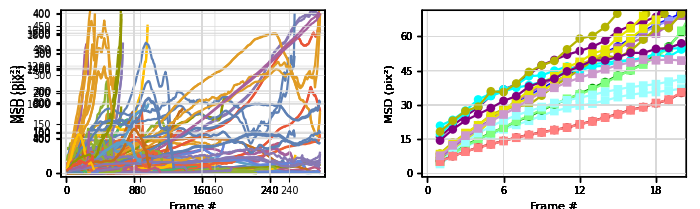

```mathematica
Show[pA,pB,pC,pD,pE,pF,pG,pH,pI]
```

### 3D purple tracks

```mathematica
tps=Table[myPurpleColorParameters[[i,1;;All,4]],{i,1,Length[myPurpleColorParameters],1}];
```

```mathematica
rps=Table[myPurpleColorParameters[[i,1;;All,13;;14]],{i,1,Length[myPurpleColorParameters],1}];
```

```mathematica
bps=Table[myPurpleColorParameters[[i,1;;All,17;;18]],{i,1,Length[myPurpleColorParameters],1}];;
```

```mathematica
Show[myNucImg,{rps,bps,rps}//Flatten[#,1]&//ListPlot[#,Joined->True,PlotStyle->{Lighter[Red,.5],Lighter[Blue,0.5]}]&,Graphics[Table[{LightPurple,Text[Style[ToString[i],20],rps⟦i⟧//Mean]},{i,1,Length[rps],1}]]]
```

-Graphics-

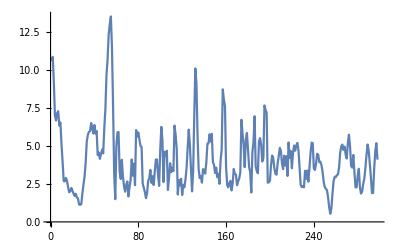

```mathematica
myPurpleColorParameters[[1,1;;All,9]]//MovingAverage[#,3]&//ListPlot[#,Joined->True]&
```

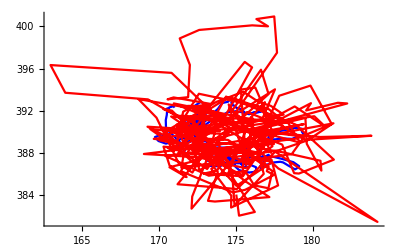
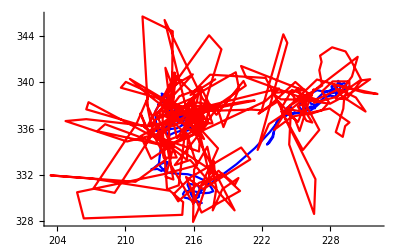
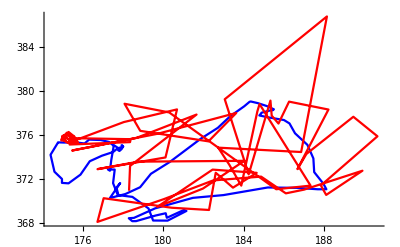
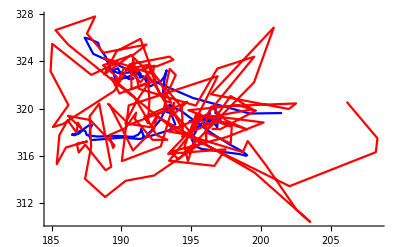
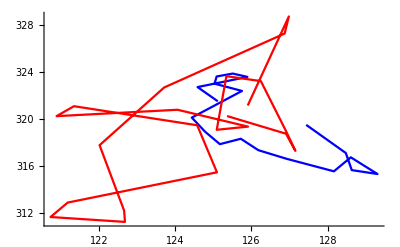
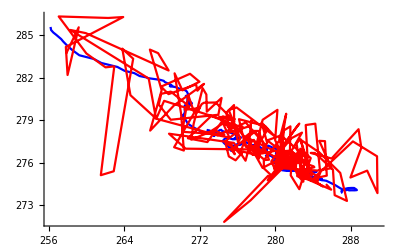
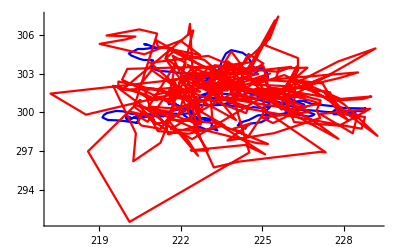
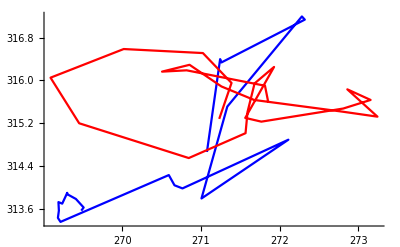

```mathematica
ra=5;
Table[{bps⟦k⟧//MovingAverage[#,ra]&,rps⟦k⟧//MovingAverage[#,2]&}//ListPlot[#,Joined->True,PlotStyle->{Blue,Red,Purple}]&,{k,1,Length[bps],1}]
```

```mathematica
dz=500; (*in nanometer*)
zrange={1,13};
dimxy=10;
dimz=zrange⟦2⟧+1-zrange⟦1⟧;
mytn=5;
skip=1;
myts=myPurpleColorParameters[[mytn,1;;All,4]];
myxs=rps⟦mytn,1;;All,1⟧;myys=rps⟦mytn,1;;All,2⟧;
```

```mathematica
myc=3;
{myts,myxs,myys}=newTracksp[[mytn,1;;All,2]]//Transpose;
my3DGridsB=Table[
My3DImager["C:\\Users\\tim_s_000\\Documents\\_mirroredX\\_Fixie\\StephanieMoonDate\\Cell03","Cell03",myts⟦i⟧,myxs⟦i⟧,myys⟦i⟧,myc,dimxy,dz,zrange]
,{i,1,Length[newTracksp⟦mytn⟧],skip}];
```

```mathematica
myc=1;
my3DGridsR=Table[
My3DImager["C:\\Users\\tim_s_000\\Documents\\_mirroredX\\_Fixie\\StephanieMoonDate\\Cell03","Cell03",myts⟦i⟧,myxs⟦i⟧,myys⟦i⟧,myc,dimxy,dz,zrange]
,{i,1,Length[newTracksp⟦mytn⟧],skip}];
```

```mathematica
my3DGridsP=Table[Grid[{
{ColorCombine[{my3DGridsR⟦i,1,1,1⟧,my3DGridsB⟦i,1,1,1⟧,my3DGridsB⟦i,1,1,1⟧}],
ColorCombine[{my3DGridsR⟦i,1,1,2⟧,my3DGridsB⟦i,1,1,2⟧,my3DGridsB⟦i,1,1,2⟧}]},
{,ColorCombine[{my3DGridsR⟦i,1,2,2⟧,my3DGridsB⟦i,1,2,2⟧,my3DGridsB⟦i,1,2,2⟧}]}
}],{i,1,Length[my3DGridsR],1}];
```

```mathematica
Manipulate[{my3DGridsR⟦i⟧,my3DGridsB⟦i⟧,my3DGridsP⟦i⟧},{i,1,Length[my3DGridsP],1}]
```

```mathematica
myTemp3D=my3DGridsB[[1;;All,1,1,1]];
myMaxN=myTemp3D//Length
```

14

```mathematica
Manipulate[
max=BandPass[myTemp3D⟦1⟧// ImageAdjust[#, {0, 0, 1}, thblue/0.05] &,{lowpass,hipass}]//ImageData//Max;
imgb=BandPass[myTemp3D⟦frame⟧ // ImageAdjust[#, {0, 0, 1}, thblue/.05] &,{lowpass,hipass}];
GraphicsRow[{myTemp3D⟦frame⟧// ImageAdjust[#, {0, 0, 1}, thblue/.05]&,
SelectComponents[Binarize[imgb,max threshold],{"Count","AdjacentBorderCount"},lo<#1<hi&&#2==0&]},ImageSize->700],
Button["Choose parameters and CLICK",{mymaxblue=max,bandpassblue={lowpass,hipass},thblue2=threshold,dotsizeblue={lo,hi}}],
{frame,1,myMaxN,1},{{threshold,0.27},0,0.4,0.01},{{lowpass,2},0,10,1},{{hipass,11},0,20,1},{{lo,5},0,100,1},{{hi,1000},100,1000,1}]
```

```mathematica
blueRunAvpXZ=Table[FindParticlesWeighted[myTemp3D⟦i⟧//ImageAdjust[#,{0,0,1},thblue]&,bandpassblue,mymaxblue,thblue2,mymask,dotsizeblue],{i,1,myMaxN,1}];
StringForm["`` blue particles were found.",blueRunAvpXZ//Flatten[#,1]&//Length]
```

Binarize::imginv: Expecting an image or graphics instead of Null.